```mathematica
s[k_, n_, x_] := 2^(k/2)*WaveletPhi[DaubechiesWavelet[3], 2^k x-n];
k=0;
n = 2;
Plot[s[k, n, x], {x, 0, 10}, PlotRange->Full]
```

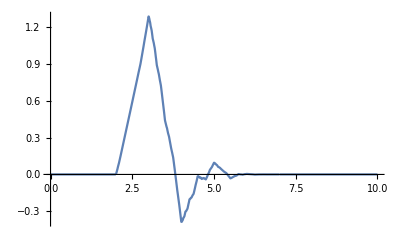
```mathematica
-Graphics-

H[m_, n_] :=0.5* NIntegrate[D[WaveletPhi[DaubechiesWavelet[3], x-m], x]*D[WaveletPhi[DaubechiesWavelet[3], x-n], x], {x, -100, 100}];
hmat = Table[H[m,n], {m, 0, 5}, {n, 0, 5}];
MatrixForm[hmat]
hmat == Transpose[hmat]
Eigensystem[hmat]
```

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.50383}. NIntegrate obtained 5.27174 and 0.0848392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.06902348017048}. NIntegrate obtained -3.37709 and 0.084863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.06902348017048}. NIntegrate obtained -3.37709 and 0.084863 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(2.63587 | -1.68854 | 0.436666 | -0.0569565 | -0.00266304 | 0.
-1.68854 | 2.63587 | -1.68854 | 0.436666 | -0.0569565 | -0.00266304
0.436666 | -1.68854 | 2.63587 | -1.68854 | 0.436666 | -0.0569565
-0.0569565 | 0.436666 | -1.68854 | 2.63587 | -1.68854 | 0.436666
-0.00266304 | -0.0569565 | 0.436666 | -1.68854 | 2.63587 | -1.68854
0. | -0.00266304 | -0.0569565 | 0.436666 | -1.68854 | 2.63587)

True

{{6.3232,4.66401,2.80017,1.36712,0.529748,0.130984},{{0.259071,-0.417827,0.508235,-0.508235,0.417827,-0.259071},{0.454798,-0.497361,0.213988,0.213988,-0.497361,0.454798},{0.540881,-0.175742,-0.420193,0.420193,0.175742,-0.540881},{0.504664,0.288156,-0.40284,-0.40284,0.288156,0.504664},{-0.374605,-0.542711,-0.255216,0.255216,0.542711,0.374605},{0.196144,0.411823,0.540304,0.540304,0.411823,0.196144}}}

```mathematica
N[π^2/200]
```

0.049348

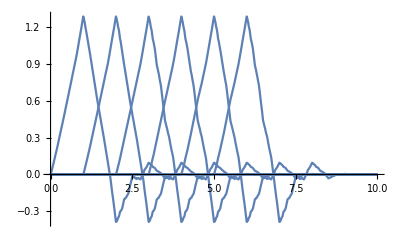

```mathematica
k = 0;
L = 2^k*10-5;
Show[Table[Plot[WaveletPhi[DaubechiesWavelet[3], 2^k x-n], {x, 0, 10}, PlotRange->All], {n, 0,L}]]
```

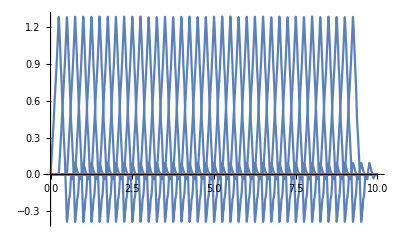

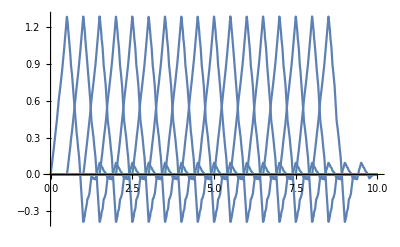

```mathematica
k = 2;
L = 2^k*10-4;
Show[ParallelTable[Plot[WaveletPhi[DaubechiesWavelet[3], 2^k x-n], {x, 0, 10}, PlotRange->All], {n, 0,L}]]
```

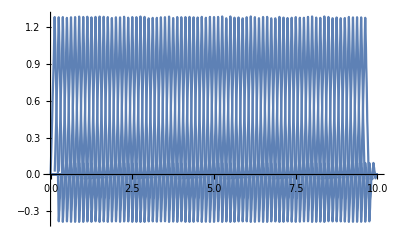

```mathematica
k = 3;
L = 2^k*10-4;
Show[ParallelTable[Plot[WaveletPhi[DaubechiesWavelet[3], 2^k x-n], {x, 0, 10}, PlotRange->All], {n, 0,L}]]
```

```mathematica
(*for k=0*)

H[m_, n_] :=0.5* NIntegrate[D[WaveletPhi[DaubechiesWavelet[3], x-m], x]*D[WaveletPhi[DaubechiesWavelet[3], x-n], x], {x, -100, 100}];
hmat = Table[H[m,n], {m, 0, 5}, {n, 0, 5}];
MatrixForm[hmat]
hmat == Transpose[hmat]
Eigensystem[hmat]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.50383}. NIntegrate obtained 5.27174 and 0.0848392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.06902348017048}. NIntegrate obtained -3.37709 and 0.084863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.06902348017048}. NIntegrate obtained -3.37709 and 0.084863 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(2.63587 | -1.68854 | 0.436666 | -0.0569565 | -0.00266304 | 0.
-1.68854 | 2.63587 | -1.68854 | 0.436666 | -0.0569565 | -0.00266304
0.436666 | -1.68854 | 2.63587 | -1.68854 | 0.436666 | -0.0569565
-0.0569565 | 0.436666 | -1.68854 | 2.63587 | -1.68854 | 0.436666
-0.00266304 | -0.0569565 | 0.436666 | -1.68854 | 2.63587 | -1.68854
0. | -0.00266304 | -0.0569565 | 0.436666 | -1.68854 | 2.63587)

True

```mathematica
{{6.32320398324481,4.66401060620794,2.8001652497752754,1.3671222374821392,0.5297475821835277,0.13098358784827757},{{0.25907149282651826,-0.41782703131644783,0.508234722845577,-0.5082347228455784,0.41782703131645116,-0.2590714928265216},{0.45479802607007175,-0.4973608436635688,0.2139881928355663,0.21398819283556092,-0.49736084366356637,0.4547980260700727},{0.5408814366980496,-0.17574179542138632,-0.42019292328348623,0.4201929232834878,0.17574179542138277,-0.5408814366980489},{0.5046643666013414,0.28815559678783614,-0.4028402029623086,-0.40284020296230777,0.2881555967878366,0.5046643666013402},{-0.3746054364796285,-0.5427111508374889,-0.25521632729227317,0.2552163272922712,0.5427111508374879,0.37460543647962763},{0.19614441762546653,0.41182343696068263,0.5403043810707585,0.5403043810707596,0.4118234369606847,0.19614441762546728}}}
```

```mathematica
(*The Eigensystem function returns two outputs:
The first output is a list of eigenvalues of the matrix hmat.The second output is a list of the corresponding eigenvectors.*)
(*lowest order eigenvalue is 0.13098358784827757*)

(*actual value below*)
```

```mathematica
N[π^2/50]
```

0.197392

```mathematica
(*for k=1*)
k = 1;
H[m_, n_] :=0.5* NIntegrate[D[2^(k/2)*WaveletPhi[DaubechiesWavelet[3], 2^k x-m], x]*D[2^(k/2)*WaveletPhi[DaubechiesWavelet[3], 2^k x-n], x], {x, -100, 100}];
hmat = Table[H[m,n], {m, 0, 10}, {n, 0, 10}];
MatrixForm[hmat]
hmat == Transpose[hmat]
Eigensystem[hmat]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.751914}. NIntegrate obtained 21.087 and 0.339357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.53451174008524}. NIntegrate obtained -13.5083 and 0.339452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.53451174008524}. NIntegrate obtained -13.5083 and 0.339452 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522 | 0. | 0. | 0. | 0. | 0. | 0.
-6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522 | 0. | 0. | 0. | 0. | 0.
1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522 | 0. | 0. | 0. | 0.
-0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522 | 0. | 0. | 0.
-0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522 | 0. | 0.
0. | -0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522 | 0.
0. | 0. | -0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826 | -0.0106522
0. | 0. | 0. | -0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666 | -0.227826
0. | 0. | 0. | 0. | -0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417 | 1.74666
0. | 0. | 0. | 0. | 0. | -0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435 | -6.75417
0. | 0. | 0. | 0. | 0. | 0. | -0.0106522 | -0.227826 | 1.74666 | -6.75417 | 10.5435)

True

{{26.993,24.2317,20.23,15.6995,11.3282,7.6116,4.77147,2.78227,1.47424,0.656392,0.19999},{{-0.122663,0.212258,-0.29098,0.351192,-0.388862,0.4017,-0.388862,0.351192,-0.29098,0.212258,-0.122663},{-0.234509,0.360358,-0.401037,0.341012,-0.195007,2.11822×10^-15,0.195007,-0.341012,0.401037,-0.360358,0.234509},{0.325637,-0.399544,0.261733,0.0200236,-0.291084,0.40172,-0.291084,0.0200236,0.261733,-0.399544,0.325637},{-0.388036,0.318268,0.040314,-0.360593,0.341293,-1.56641×10^-15,-0.341293,0.360593,-0.040314,-0.318268,0.388036},{0.416661,-0.141992,-0.317948,0.331107,0.119974,-0.402779,0.119974,0.331107,-0.317948,-0.141992,0.416661},{0.410533,0.0750432,-0.401414,-0.0379991,0.404047,-2.20208×10^-15,-0.404047,0.0379991,0.401414,-0.0750432,-0.410533},{0.373548,0.268609,-0.243736,-0.37199,0.0858557,0.407815,0.0858557,-0.37199,-0.243736,0.268609,0.373548},{0.314112,0.387467,0.056379,-0.336883,-0.366789,1.4677×10^-15,0.366789,0.336883,-0.056379,-0.387467,-0.314112},{0.242309,0.408777,0.324908,0.0313045,-0.283761,-0.417426,-0.283761,0.0313045,0.324908,0.408777,0.242309},{0.165014,0.336281,0.416212,0.372491,0.218411,1.49142×10^-15,-0.218411,-0.372491,-0.416212,-0.336281,-0.165014},{-0.0840044,-0.189471,-0.284189,-0.356756,-0.402208,-0.417696,-0.402208,-0.356756,-0.284189,-0.189471,-0.0840044}}}

```mathematica
{{25.29281593297924,18.65604242483176,11.200660999101101,5.468488949928557,2.1189903287341108,0.5239343513931103},{{0.25907149282651826,-0.41782703131644783,0.508234722845577,-0.5082347228455784,0.41782703131645116,-0.2590714928265216},{0.45479802607007175,-0.4973608436635688,0.2139881928355663,0.21398819283556092,-0.49736084366356637,0.4547980260700727},{0.5408814366980496,-0.17574179542138632,-0.42019292328348623,0.4201929232834878,0.17574179542138277,-0.5408814366980489},{0.5046643666013414,0.28815559678783614,-0.4028402029623086,-0.40284020296230777,0.2881555967878366,0.5046643666013402},{-0.3746054364796285,-0.5427111508374889,-0.25521632729227317,0.2552163272922712,0.5427111508374879,0.37460543647962763},{0.19614441762546653,0.41182343696068263,0.5403043810707585,0.5403043810707596,0.4118234369606847,0.19614441762546728}}}
```

```mathematica
(*lowest order eigenvalue = 0.5239343513931103*)

(*for k=0*)

H[m_, n_] :=0.5* NIntegrate[D[WaveletPhi[DaubechiesWavelet[3], x-m], x]*D[WaveletPhi[DaubechiesWavelet[3], x-n], x], {x, -100, 100}];
hmat = Table[H[m,n], {m, 0, 0}, {n, 0, 0}];
MatrixForm[hmat]
hmat == Transpose[hmat]
Eigensystem[hmat]
```

{{25.2928,18.656,11.2007,5.46849,2.11899,0.523934},{{0.259071,-0.417827,0.508235,-0.508235,0.417827,-0.259071},{0.454798,-0.497361,0.213988,0.213988,-0.497361,0.454798},{0.540881,-0.175742,-0.420193,0.420193,0.175742,-0.540881},{0.504664,0.288156,-0.40284,-0.40284,0.288156,0.504664},{-0.374605,-0.542711,-0.255216,0.255216,0.542711,0.374605},{0.196144,0.411823,0.540304,0.540304,0.411823,0.196144}}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.50383}. NIntegrate obtained 5.27174 and 0.0848392 for the integral and error estimates.

(2.63587)

True

```mathematica
{{2.63587220779033},{{1.}}}
```

```mathematica
(*for k=1*)
k = 2;
H[m_, n_] :=0.5* NIntegrate[D[2^(k/2)*WaveletPhi[DaubechiesWavelet[3], 2^k x-m], x]*D[2^(k/2)*WaveletPhi[DaubechiesWavelet[3], 2^k x-n], x], {x, -100, 100}];
hmat = Table[H[m,n], {m, 0, 5}, {n, 0, 5}];
MatrixForm[hmat]
hmat == Transpose[hmat]
Eigensystem[hmat]
```

```mathematica
(*Define the new Hamiltonian matrix*)H={{295/56,-356/105},{-356/105,295/56}};

(*Diagonalize the Hamiltonian matrix*)
{eigenvalues,eigenvectors}=Eigensystem[H];

(*Print the diagonalized matrix (eigenvalues)*)
Print["Eigenvalues: ",eigenvalues];

(*Generate the x-axis values (space in the box)*)
x=Range[0,5,0.05];

(*Construct the first 2 wavefunctions using the eigenvectors*)
wavefunction1=Total[Table[eigenvectors[[1,i]] Sin[i π x/5],{i,1,2}]];
wavefunction2=Total[Table[eigenvectors[[2,i]] Sin[i π x/5],{i,1,2}]];

(*Plot the wavefunctions*)
wave1Plot=ListLinePlot[Transpose[{x,wavefunction1}],PlotStyle->Orange,PlotLabel->"Wavefunction 1"];

wave2Plot=ListLinePlot[Transpose[{x,wavefunction2}],PlotStyle->Red,PlotLabel->"Wavefunction 2"];

(*Display both wavefunctions on the same plot*)
Show[wave1Plot,wave2Plot,PlotLabel->"First 2 Wavefunctions for Particle in a Box with New Hamiltonian Matrix",Frame->True,FrameLabel->{"x","Wavefunction"},PlotRange->All]
```

Eigenvalues: {1039/120,1577/840}

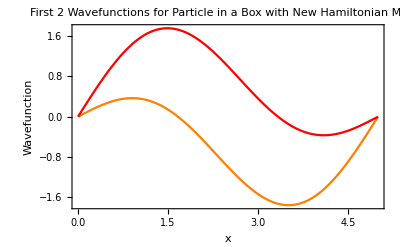
```mathematica
-Graphics-

k=1; (*Resolution index*)
nMax=15; (*Number of scaling functions*)
coefficients={0.05388901,0.12328756,0.18970608,0.24765034,0.29503746,0.33026428,0.3519887,0.35933111,0.3519887,0.33026428,0.29503746,0.24765034,0.18970608,0.12328756,0.05388901};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction*)
Plot[eigenfunction,{x,0,10},PlotLabel->"Eigenfunction"]
```

-Graphics-

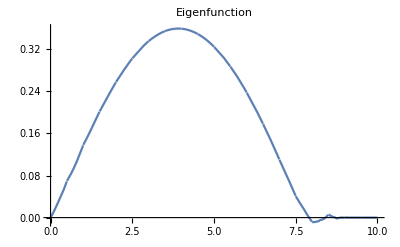

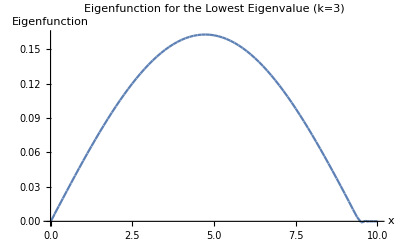

```mathematica
k=3; (*Resolution index*)
nMax=75; (*Number of scaling functions*)
coefficients={0.005044562876055658,0.011735208884293238,0.018593243860403195,0.025349166135936192,0.03202014713129138,0.038626615792177355,0.04516636410416874,0.05162876558407795,0.05800212041900192,0.06427515536924347,0.07043697054130703,0.07647690841496682,0.08238452384988544,0.08814959703487525,0.09376215334538737,0.0992124818199786,0.1044911522240447,0.10958903135969678,0.11449729884393375,0.11920746236147564,0.12371137235723581,0.12800123613706077,0.1320696313509026,0.13590951883506328,0.13951425479140075,0.1428776022824665,0.14599374202269502,0.14885728244696897,0.15146326903914012,0.1538071929043645,0.15588499857042323,0.15769309100452544,0.1592283418334577,0.16048809475631345,0.16147017014044437,0.16217286879267312,0.1625949748992499,0.16273575812946084,0.16259497489925148,0.16217286879267723,0.16147017014045115,0.1604880947563236,0.159228341833471,0.1576930910045415,0.15588499857044125,0.1538071929043844,0.15146326903916274,0.14885728244699506,0.14599374202272486,0.14287760228250077,0.1395142547914393,0.1359095188351044,0.13206963135094407,0.12800123613710165,0.12371137235727594,0.11920746236151519,0.11449729884397301,0.10958903135973644,0.10449115222408491,0.09921248182001968,0.09376215334542931,0.08814959703491838,0.08238452384992875,0.07647690841500962,0.07043697054134837,0.06427515536928224,0.058002120419037406,0.05162876558410956,0.04516636410419668,0.038626615792201106,0.03202014713131081,0.025349166135951774,0.018593243860414624,0.011735208884300245,0.00504456287605841};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,10},PlotLabel->"Eigenfunction for the Lowest Eigenvalue (k=3)",AxesLabel->{"x","Eigenfunction"},PlotRange->All, PlotPoints->100]
```

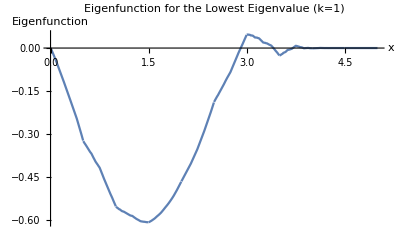

```mathematica
k=1; (*Resolution index*)
nMax=5; (*Number of scaling functions*)
coefficients={-0.25134407243985873,-0.5043293090198548,-0.6041160572487743,-0.5043293090198556,-0.2513440724398592};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,5},PlotLabel->"Eigenfunction for the Lowest Eigenvalue (k=1)",AxesLabel->{"x","Eigenfunction"},PlotRange->All]
```

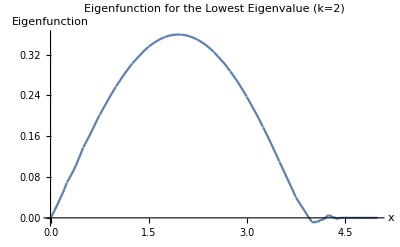

```mathematica
k=2; (*Resolution index*)
nMax=15; (*Number of scaling functions*)
coefficients={0.05388900496093259,0.12328755726085464,0.1897060805379534,0.24765033978862355,0.29503745599503844,0.33026428261248386,0.3519887006572378,0.35933111019935865,0.3519887006572356,0.3302642826124796,0.2950374559950335,0.24765033978861872,0.18970608053794863,0.1232875572608511,0.05388900496093085};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,5},PlotLabel->"Eigenfunction for the Lowest Eigenvalue (k=2)",AxesLabel->{"x","Eigenfunction"},PlotRange->All]
```

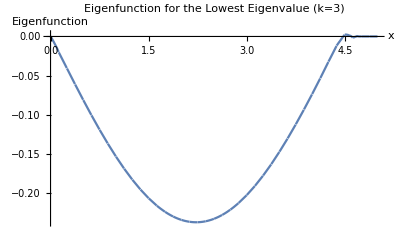

```mathematica
k=3; (*Resolution index*)
nMax=35; (*Number of scaling functions*)
coefficients={-0.01562439794447787,-0.036253739341118266,-0.05718354867237093,-0.07745098717392918,-0.09698598421067672,-0.11573451763181072,-0.13357856583741703,-0.1503807953839857,-0.16600826142011724,-0.18033803400972662,-0.19325794339625801,-0.2046669963426956,-0.21447601606894154,-0.22260832334410513,-0.22900034255806578,-0.23360210248252816,-0.23637762774327448,-0.23730522004810864,-0.2363776277432786,-0.23360210248253663,-0.22900034255807888,-0.22260832334412356,-0.21447601606896582,-0.20466699634272417,-0.19325794339628935,-0.1803380340097596,-0.16600826142015007,-0.15038079538401633,-0.13357856583744307,-0.11573451763183182,-0.09698598421069361,-0.07745098717394305,-0.057183548672381686,-0.03625373934112509,-0.015624397944480678};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,5},PlotLabel->"Eigenfunction for the Lowest Eigenvalue (k=3)",AxesLabel->{"x","Eigenfunction"},PlotRange->All]
```

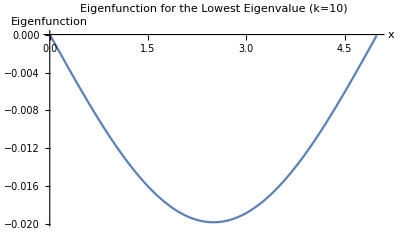

```mathematica
k=10; (*Resolution index*)
nMax=5115; (*Number of scaling functions*)
coefficients={-9.051444601529819e-06,-2.107182734549574e-05,-3.342855746799236e-05,-4.565956210237811e-05,-5.781678862702789e-05,-6.995765182351292e-05,-8.209869754993016e-05,-9.4241151297959e-05,-0.00010638407542784063,-0.0001185270234143053,-0.00013066990776884672,-0.0001428127306198674,-0.0001549554967425641,-0.00016709820440005186,-0.00017924084926629233,-0.00019138342661676356,-0.0002035259317979906,-0.00021566836021559387,-0.00022781070729078177,-0.00023995296844552628,-0.00025209513910079884,-0.00026423721467717053,-0.0002763791905951744,-0.00028852106227539206,-0.0003006628251384525,-0.00031280447460502983,-0.00032494600609583976,-0.0003370874150316423,-0.00034922869683324425,-0.00036136984692150195,-0.00037351086071732176,-0.0003856517336416611,-0.00039779246111552906,-0.00040993303855998894,-0.00042207346139616045,-0.0004342137250452221,-0.0004463538249284116,-0.00045849375646703076,-0.0004706335150824406,-0.0004827730961960738,-0.0004949124952294253,-0.0005070517076040627,-0.0005191907287416205,-0.0005313295540638069,-0.0005434681789924053,-0.0005556065989492747,-0.0005677448093563473,-0.0005798828056356341,-0.0005920205832092298,-0.0006041581374993097,-0.0006162954639281353,-0.0006284325579180511,-0.0006405694148914939,-0.000652706030270985,-0.0006648423994791402,-0.0006769785179386717,-0.0006891143810723763,-0.0007012499843031555,-0.0007133853230540078,-0.0007255203927480344,-0.0007376551888084337,-0.0007497897066585076,-0.0007619239417216565,-0.0007740578894213907,-0.0007861915451813348,-0.000798324904425218,-0.0008104579625768833,-0.0008225907150602877,-0.0008347231572995063,-0.0008468552847187289,-0.0008589870927422598,-0.000871118576794527,-0.0008832497323000797,-0.0008953805546835936,-0.0009075110393698684,-0.0009196411817838311,-0.0009317709773505383,-0.0009439004214951758,-0.0009560295096430623,-0.0009681582372196575,-0.0009802865996505466,-0.0009924145923614546,-0.0010045422107782481,-0.0010166694503269387,-0.0010287963064336768,-0.001040922774524759,-0.001053048850026625,-0.0010651745283658627,-0.0010772998049692075,-0.0010894246752635552,-0.001101549134675959,-0.0011136731786336167,-0.001125796802563889,-0.0011379200018942909,-0.001150042772052497,-0.0011621651084663437,-0.0011742870065638345,-0.0011864084617731353,-0.0011985294695225684,-0.0012106500252406388,-0.001222770124356016,-0.0012348897622975518,-0.0012470089344942628,-0.0012591276363753425,-0.0012712458633701543,-0.0012833636109082444,-0.001295480874419344,-0.0013075976493333783,-0.0013197139310804455,-0.0013318297150908302,-0.0013439449967950002,-0.0013560597716236113,-0.0013681740350075231,-0.001380287782377776,-0.0013924010091656111,-0.0014045137108024686,-0.0014166258827199819,-0.0014287375203499732,-0.001440848619124494,-0.0014529591744757789,-0.0014650691818362714,-0.0014771786366386127,-0.001489287534315658,-0.0015013958703004714,-0.0015135036400263486,-0.0015256108389267765,-0.0015377174624354624,-0.001549823505986334,-0.0015619289650135454,-0.0015740338349514566,-0.0015861381112346595,-0.0015982417892979792,-0.0016103448645764583,-0.001622447332505377,-0.0016345491885202184,-0.0016466504280566966,-0.0016587510465507676,-0.0016708510394386072,-0.0016829504021566482,-0.0016950491301415572,-0.001707147218830236,-0.0017192446636598313,-0.0017313414600677263,-0.001743437603491553,-0.001755533089369186,-0.0017676279131387447,-0.0017797220702386208,-0.001791815556107436,-0.0018039083661840537,-0.0018160004959076094,-0.0018280919407175171,-0.0018401826960534212,-0.0018522727573552608,-0.0018643621200632034,-0.0018764507796176831,-0.0018885387314594114,-0.0019006259710293548,-0.0019127124937687527,-0.0019247982951191007,-0.0019368833705221747,-0.0019489677154200299,-0.0019610513252549975,-0.001973134195469676,-0.0019852163215069527,-0.0019972976988100084,-0.0020093783228222945,-0.00202145818898753,-0.002033537292749724,-0.00204561562955317,-0.0020576931948424596,-0.002069769984062482,-0.0020818459926584096,-0.002093921216075743,-0.0021059956497602784,-0.002118069289158081,-0.0021301421297155194,-0.0021422141668792373,-0.002154285396096196,-0.0021663558128136723,-0.0021784254124792555,-0.002190494190540854,-0.0022025621424466724,-0.0022146292636452216,-0.0022266955495853225,-0.0022387609957160966,-0.0022508255974870092,-0.0022628893503478416,-0.0022749522497486903,-0.00228701429113997,-0.002299075469972417,-0.002311135781697109,-0.0023231952217654464,-0.0023352537856291375,-0.002347311468740231,-0.0023593682665511177,-0.002371424174514522,-0.0023834791880834954,-0.0023955333027114198,-0.0024075865138520162,-0.002419638816959344,-0.0024316902074878275,-0.0024437406808922187,-0.0024557902326276266,-0.0024678388581494907,-0.0024798865529136204,-0.0024919333123761566,-0.0025039791319936334,-0.002516024007222923,-0.002528067933521256,-0.002540110906346174,-0.002552152921155592,-0.002564193973407791,-0.0025762340585614384,-0.002588273172075554,-0.0026003113094095337,-0.0026123484660231294,-0.002624384637376481,-0.0026364198189300883,-0.0026484540061448183,-0.0026604871944819163,-0.0026725193794030124,-0.0026845505563701097,-0.002696580720845576,-0.0027086098682921763,-0.002720637994173055,-0.0027326650939517735,-0.0027446911630922507,-0.0027567161970587914,-0.002768740191316066,-0.0027807631413291596,-0.0027927850425635502,-0.0028048058904851228,-0.0028168256805601523,-0.0028288444082553137,-0.0028408620690376874,-0.002852878658374772,-0.002864894171734457,-0.0028769086045850327,-0.0028889219523952027,-0.002900934210634064,-0.00291294537477114,-0.0029249554402763583,-0.00293696440262007,-0.0029489722572730187,-0.0029609789997063927,-0.002972984625391797,-0.0029849891298012526,-0.002996992508407194,-0.0030089947566824937,-0.003020995870100427,-0.0030329958441347167,-0.0030449946742595138,-0.0030569923559493955,-0.0030689888846793687,-0.003080984255924882,-0.003092978465161827,-0.003104971507866543,-0.0031169633795157642,-0.003128954075586703,-0.0031409435915570197,-0.0031529319229047963,-0.0031649190651085713,-0.0031769050136473648,-0.0031888897640006252,-0.0032008733116482514,-0.0032128556520705735,-0.0032248367807483696,-0.003236816693162893,-0.003248795384795851,-0.0032607728511294285,-0.003272749087646263,-0.0032847240898294535,-0.003296697853162547,-0.0033086703731295746,-0.0033206416452150373,-0.0033326116649039267,-0.0033445804276817184,-0.003356547929034341,-0.003368514164448149,-0.0033804791294100305,-0.003392442819407354,-0.003404405229927956,-0.0034163663564601306,-0.0034283261944926596,-0.003440284739514801,-0.0034522419870163315,-0.0034641979324875343,-0.003476152571419208,-0.0034881058993025903,-0.003500057911629418,-0.0035120086038919456,-0.0035239579715829134,-0.003535906010195548,-0.0035478527152236093,-0.0035597980821613397,-0.0035717421065034993,-0.003583684783745342,-0.003595626109382659,-0.0036075660789116966,-0.0036195046878292427,-0.003631441931632603,-0.003643377805819541,-0.0036553123058883715,-0.003667245427337959,-0.0036791771656676706,-0.0036911075163773934,-0.00370303647496752,-0.003714964036938973,-0.003726890197793234,-0.003738814953032303,-0.003750738298158694,-0.0037626602286754598,-0.0037745807400861885,-0.0037864998278949935,-0.0037984174876065286,-0.003810333714725979,-0.003822248504759049,-0.00383416185321204,-0.003846073755591784,-0.0038579842074056275,-0.0038698932041614674,-0.0038818007413677696,-0.003893706814533534,-0.003905611419168345,-0.003917514550782301,-0.003929416204886048,-0.003941316376990824,-0.003953215062608478,-0.003965112257251357,-0.0039770079564323815,-0.003988902155665013,-0.004000794850463333,-0.004012686036341918,-0.004024575708815964,-0.0040364638634012235,-0.004048350495614044,-0.004060235600971298,-0.004072119174990448,-0.004084001213189538,-0.0040958817110872065,-0.004107760664202675,-0.0041196380680557304,-0.004131513918166755,-0.004143388210056679,-0.004155260939247048,-0.004167132101260005,-0.004179001691618316,-0.0041908697058453,-0.004202736139464909,-0.004214600988001632,-0.004226464246980605,-0.004238325911927523,-0.004250185978368717,-0.0042620444418311355,-0.004273901297842289,-0.004285756541930265,-0.004297610169623805,-0.004309462176452261,-0.004321312557945613,-0.0043331613096344096,-0.004345008427049819,-0.004356853905723634,-0.00436869774118827,-0.004380539928976771,-0.0043923804646228,-0.004404219343660684,-0.004416056561625306,-0.004427892114052196,-0.004439725996477512,-0.004451558204438001,-0.004463388733471077,-0.004475217579114794,-0.00448704473690784,-0.004498870202389566,-0.0045106939710999475,-0.004522516038579588,-0.004534336400369763,-0.004546155052012376,-0.00455797198904998,-0.004569787207025774,-0.00458160070148356,-0.004593412467967814,-0.004605222502023686,-0.004617030799196916,-0.0046288373550339365,-0.004640642165081873,-0.004652445224888489,-0.004664246530002238,-0.00467604607597222,-0.004687843858348146,-0.004699639872680459,-0.004711434114520198,-0.004723226579419105,-0.0047350172629295785,-0.004746806160604754,-0.004758593267998383,-0.004770378580664919,-0.004782162094159365,-0.004793943804037477,-0.004805723705855717,-0.004817501795171258,-0.0048292780675419835,-0.0048410525185264165,-0.00485282514368378,-0.004864595938573978,-0.004876364898757616,-0.004888132019795935,-0.004899897297250898,-0.004911660726685186,-0.004923422303662142,-0.004935182023745833,-0.004946939882501036,-0.004958695875493206,-0.004970449998288546,-0.004982202246453953,-0.004993952615556962,-0.0050057011011658764,-0.005017447698849682,-0.0050291924041780635,-0.0050409352127214445,-0.005052676120050972,-0.0050644151217385525,-0.005076152213356744,-0.00508788739047885,-0.005099620648678859,-0.0051113519835314924,-0.005123081390612236,-0.005134808865497252,-0.00514653440376349,-0.005158258000988611,-0.0051699796527510285,-0.005181699354629827,-0.005193417102204872,-0.005205132891056721,-0.005216846716766739,-0.005228558574916987,-0.005240268461090277,-0.00525197637087018,-0.005263682299841026,-0.005275386243587873,-0.0052870881976964925,-0.005298788157753473,-0.005310486119346085,-0.005322182078062384,-0.005333876029491174,-0.0053455679692220055,-0.005357257892845248,-0.00536894579595193,-0.005380631674133898,-0.005392315522983752,-0.0054039973380948375,-0.0054156771150613596,-0.005427354849478248,-0.005439030536941217,-0.005450704173046705,-0.005462375753391889,-0.005474045273574789,-0.005485712729194198,-0.005497378115849675,-0.005509041429141545,-0.005520702664670932,-0.0055323618180397735,-0.005544018884850764,-0.005555673860707393,-0.0055673267412139045,-0.005578977521975311,-0.005590626198597455,-0.005602272766687003,-0.005613917221851403,-0.0056255595596989205,-0.005637199775838601,-0.005648837865880272,-0.005660473825434535,-0.0056721076501128655,-0.005683739335527547,-0.005695368877291657,-0.005706996271019038,-0.005718621512324311,-0.005730244596822913,-0.005741865520131119,-0.005753484277866021,-0.005765100865645641,-0.005776715279088747,-0.005788327513814949,-0.0057999375654446015,-0.005811545429598925,-0.005823151101899982,-0.005834754577970602,-0.005846355853434485,-0.0058579549239161765,-0.005869551785041073,-0.005881146432435356,-0.005892738861726044,-0.005904329068540932,-0.005915917048508735,-0.0059275027972589605,-0.0059390863104219534,-0.005950667583628948,-0.005962246612511994,-0.005973823392704024,-0.0059853979198387815,-0.005996970189550912,-0.006008540197475911,-0.0060201079392501015,-0.006031673410510644,-0.006043236606895546,-0.006054797524043714,-0.006066356157594859,-0.00607791250318958,-0.006089466556469309,-0.006101018313076411,-0.0061125677686540885,-0.0061241149188463835,-0.006135659759298177,-0.0061472022856552755,-0.006158742493564399,-0.006170280378673117,-0.006181815936629878,-0.006193349163083981,-0.006204880053685609,-0.006216408604085776,-0.006227934809936456,-0.006239458666890499,-0.006250980170601664,-0.006262499316724518,-0.006274016100914556,-0.006285530518828171,-0.006297042566122617,-0.006308552238456078,-0.0063200595314876215,-0.006331564440877221,-0.006343066962285705,-0.0063545670913748645,-0.006366064823807387,-0.0063775601552468275,-0.006389053081357659,-0.006400543597805256,-0.006412031700255961,-0.006423517384377025,-0.006435000645836515,-0.006446481480303476,-0.006457959883447832,-0.006469435850940427,-0.006480909378452977,-0.006492380461658213,-0.006503849096229756,-0.0065153152778421874,-0.00652677900217096,-0.006538240264892487,-0.006549699061684129,-0.006561155388224143,-0.006572609240191704,-0.006584060613266961,-0.006595509503130974,-0.006606955905465706,-0.006618399815954107,-0.006629841230280056,-0.006641280144128391,-0.00665271655318491,-0.006664150453136298,-0.006675581839670216,-0.006687010708475273,-0.0066984370552409635,-0.0067098608756577215,-0.006721282165417044,-0.006732700920211397,-0.006744117135734115,-0.006755530807679522,-0.006766941931742862,-0.0067783505036203215,-0.006789756519009132,-0.0068011599736074735,-0.006812560863114474,-0.00682395918323022,-0.006835354929655747,-0.006846748098093114,-0.006858138684245335,-0.006869526683816433,-0.006880912092511458,-0.0068922949060362905,-0.006903675120097776,-0.00691505273040379,-0.006926427732663201,-0.0069378001225858755,-0.006949169895882608,-0.006960537048265187,-0.006971901575446472,-0.0069832634731403125,-0.006994622737061555,-0.0070059793629259435,-0.00701733334645029,-0.007028684683352393,-0.007040033369351121,-0.00705137940016619,-0.007062722771518456,-0.007074063479129705,-0.007085401518722725,-0.0070967368860212834,-0.0071080695767502,-0.007119399586635268,-0.007130726911403272,-0.007142051546782051,-0.007153373488500453,-0.007164692732288379,-0.0071760092738767265,-0.007187323108997456,-0.007198634233383445,-0.007209942642768655,-0.007221248332888058,-0.007232551299477648,-0.007243851538274428,-0.007255149045016479,-0.007266443815442883,-0.007277735845293757,-0.007289025130310221,-0.007300311666234469,-0.007311595448809786,-0.007322876473780483,-0.007334154736891866,-0.007345430233890272,-0.007356702960523093,-0.007367972912538718,-0.00737924008568659,-0.007390504475717232,-0.007401766078382227,-0.007413024889434222,-0.007424280904626901,-0.007435534119714973,-0.007446784530454217,-0.007458032132601485,-0.0074692769219147255,-0.007480518894152983,-0.007491758045076343,-0.007502994370445837,-0.007514227866023599,-0.007525458527572797,-0.007536686350857719,-0.007547911331643761,-0.007559133465697343,-0.007570352748785959,-0.007581569176678239,-0.007592782745143915,-0.007603993449953737,-0.007615201286879513,-0.007626406251694067,-0.007637608340171444,-0.0076488075480868,-0.0076600038712162965,-0.0076711973053371655,-0.007682387846227727,-0.0076935754896674214,-0.007704760231436825,-0.007715942067317506,-0.00772712099309215,-0.007738297004544521,-0.007749470097459527,-0.00776064026762324,-0.007771807510822835,-0.007782971822846515,-0.007794133199483621,-0.007805291636524551,-0.007816447129760783,-0.007827599674984986,-0.007838749267990917,-0.007849895904573492,-0.007861039580528686,-0.007872180291653557,-0.007883318033746355,-0.007894452802606384,-0.00790558459403413,-0.007916713403831174,-0.007927839227800241,-0.007938962061745242,-0.007950081901471142,-0.007961198742784073,-0.007972312581491212,-0.007983423413400905,-0.007994531234322637,-0.00800563604006712,-0.008016737826446076,-0.00802783658927237,-0.008038932324360057,-0.008050025027524324,-0.008061114694581468,-0.00807220132134902,-0.00808328490364556,-0.008094365437290944,-0.008105442918106102,-0.008116517341913102,-0.0081275887045351,-0.008138657001796454,-0.008149722229522668,-0.008160784383540403,-0.008171843459677624,-0.008182899453763352,-0.008193952361627775,-0.008205002179102175,-0.00821604890201905,-0.008227092526212098,-0.008238133047516152,-0.008249170461767217,-0.008260204764802484,-0.00827123595246039,-0.008282264020580446,-0.008293288965003334,-0.008304310781570913,-0.00831532946612621,-0.008326345014513504,-0.00833735742257825,-0.008348366686167015,-0.008359372801127586,-0.008370375763308907,-0.00838137556856117,-0.008392372212735736,-0.008403365691685217,-0.008414356001263409,-0.008425343137325327,-0.008436327095727133,-0.00844730787232616,-0.00845828546298096,-0.008469259863551263,-0.008480231069898049,-0.008491199077883486,-0.00850216388337095,-0.008513125482224942,-0.008524083870311233,-0.008535039043496718,-0.00854599099764968,-0.00855693972863955,-0.008567885232336984,-0.008578827504613803,-0.008589766541343054,-0.008600702338399057,-0.008611634891657236,-0.008622564196994429,-0.008633490250288629,-0.008644413047419055,-0.008655332584266064,-0.008666248856711264,-0.00867716186063753,-0.008688071591928987,-0.008698978046470933,-0.008709881220149982,-0.008720781108853966,-0.008731677708471924,-0.008742571014894096,-0.008753461024012057,-0.008764347731718547,-0.008775231133907659,-0.00878611122647465,-0.008796988005316095,-0.008807861466329718,-0.008818731605414493,-0.008829598418470705,-0.00884046190139986,-0.008851322050104783,-0.008862178860489551,-0.008873032328459467,-0.00888388244992107,-0.00889472922078217,-0.008905572636951827,-0.008916412694340427,-0.008927249388859559,-0.008938082716422035,-0.008948912672941971,-0.008959739254334772,-0.008970562456517157,-0.008981382275407117,-0.008992198706923908,-0.009003011746988107,-0.009013821391521572,-0.009024627636447421,-0.009035430477690034,-0.009046229911175124,-0.0090570259328296,-0.009067818538581655,-0.009078607724360758,-0.009089393486097698,-0.009100175819724577,-0.00911095472117481,-0.009121730186383046,-0.009132502211285278,-0.009143270791818725,-0.009154035923922025,-0.009164797603535035,-0.00917555582659899,-0.009186310589056439,-0.0091970618868512,-0.00920780971592836,-0.009218554072234243,-0.009229294951716557,-0.0092400323503244,-0.009250766264008049,-0.009261496688719157,-0.009272223620410623,-0.00928294705503671,-0.00929366698855308,-0.009304383416916593,-0.00931509633608549,-0.009325805742019347,-0.009336511630679022,-0.009347213998026769,-0.009357912840026161,-0.009368608152642144,-0.009379299931840928,-0.009389988173590042,-0.009400672873858358,-0.009411354028616058,-0.009422031633834711,-0.00943270568548724,-0.009443376179547821,-0.009454043111992036,-0.009464706478796754,-0.009475366275940277,-0.00948602249940218,-0.009496675145163481,-0.009507324209206454,-0.009517969687514762,-0.009528611576073357,-0.009539249870868611,-0.009549884567888287,-0.009560515663121454,-0.009571143152558602,-0.009581767032191461,-0.009592387298013205,-0.009603003946018315,-0.00961361697220268,-0.009624226372563402,-0.009634832143099181,-0.00964543427980999,-0.009656032778697239,-0.009666627635763588,-0.009677218847013155,-0.009687806408451386,-0.009698390316085152,-0.009708970565922629,-0.0097195471539735,-0.009730120076248797,-0.009740689328760845,-0.00975125490752333,-0.009761816808551455,-0.009772375027861737,-0.009782929561472191,-0.009793480405402111,-0.00980402755567209,-0.009814571008304216,-0.009825110759321952,-0.009835646804750183,-0.009846179140615276,-0.00985670776294487,-0.009867232667768034,-0.009877753851115159,-0.009888271309018181,-0.00989878503751039,-0.009909295032626551,-0.009919801290402772,-0.009930303806876586,-0.009940802578086768,-0.009951297600073654,-0.009961788868878958,-0.009972276380545852,-0.009982760131119026,-0.009993240116644523,-0.010003716333169769,-0.010014188776743534,-0.010024657443416117,-0.010035122329239208,-0.010045583430265886,-0.010056040742550766,-0.010066494262149776,-0.010076943985120343,-0.010087389907521309,-0.010097832025412855,-0.010108270334856602,-0.010118704831915687,-0.010129135512654729,-0.010139562373139772,-0.010149985409438273,-0.010160404617618995,-0.010170819993752307,-0.010181231533910054,-0.010191639234165606,-0.01020204309059369,-0.010212443099270501,-0.010222839256273576,-0.010233231557681861,-0.01024361999957583,-0.010254004578037485,-0.010264385289150241,-0.01027476212899895,-0.010285135093669923,-0.010295504179250965,-0.010305869381831307,-0.01031623069750172,-0.010326588122354298,-0.010336941652482775,-0.010347291283982282,-0.010357637012949417,-0.010367978835482258,-0.010378316747680232,-0.01038865074564441,-0.01039898082547724,-0.010409306983282678,-0.010419629215166192,-0.010429947517234668,-0.010440261885596443,-0.010450572316361406,-0.01046087880564096,-0.010471181349547894,-0.010481479944196617,-0.01049177458570302,-0.010502065270184418,-0.010512351993759581,-0.010522634752548879,-0.010532913542674077,-0.01054318836025856,-0.010553459201427067,-0.010563726062305911,-0.010573988939022887,-0.010584247827707255,-0.010594502724489847,-0.010604753625502913,-0.010615000526880226,-0.010625243424757062,-0.010635482315270218,-0.010645717194558023,-0.010655948058760379,-0.010666174904018798,-0.010676397726476217,-0.01068661652227701,-0.010696831287567158,-0.010707042018494121,-0.01071724871120686,-0.010727451361855902,-0.01073764996659318,-0.010747844521572273,-0.01075803502294824,-0.010768221466877654,-0.010778403849518729,-0.010788582167031146,-0.010798756415576184,-0.010808926591316534,-0.010819092690416364,-0.01082925470904133,-0.01083941264335883,-0.010849566489537818,-0.010859716243748813,-0.010869861902163814,-0.010880003460956383,-0.010890140916301517,-0.010900274264375705,-0.01091040350135713,-0.010920528623425458,-0.010930649626761992,-0.010940766507549491,-0.010950879261972316,-0.010960987886216364,-0.010971092376469097,-0.010981192728919585,-0.01099128893975847,-0.011001381005177944,-0.011011468921371668,-0.011021552684535023,-0.011031632290864868,-0.011041707736559601,-0.011051779017819176,-0.01106184613084515,-0.01107190907184064,-0.011081967837010398,-0.01109202242256068,-0.011102072824699388,-0.011112119039636012,-0.011122161063581569,-0.011132198892748628,-0.011142232523351375,-0.011152261951605631,-0.011162287173728722,-0.011172308185939598,-0.011182324984458772,-0.011192337565508347,-0.011202345925311956,-0.011212350060095045,-0.011222349966084481,-0.011232345639508768,-0.01124233707659797,-0.011252324273583792,-0.011262307226699403,-0.011272285932179708,-0.011282260386261142,-0.011292230585181825,-0.011302196525181414,-0.011312158202501267,-0.011322115613384228,-0.011332068754074798,-0.011342017620819116,-0.011351962209864924,-0.011361902517461627,-0.011371838539860131,-0.011381770273313087,-0.011391697714074727,-0.011401620858400872,-0.011411539702548839,-0.011421454242777624,-0.011431364475347913,-0.011441270396522043,-0.01145117200256402,-0.011461069289739558,-0.011470962254315868,-0.011480850892561826,-0.011490735200747747,-0.011500615175145676,-0.011510490812029341,-0.011520362107674112,-0.01153022905835695,-0.011540091660356506,-0.011549949909952988,-0.011559803803428347,-0.011569653337066221,-0.011579498507151896,-0.011589339309972184,-0.011599175741815456,-0.011609007798971826,-0.01161883547773308,-0.011628658774392661,-0.01163847768524567,-0.011648292206588879,-0.011658102334720656,-0.011667908065941056,-0.011677709396551848,-0.011687506322856384,-0.0116972988411596,-0.011707086947768121,-0.01171687063899031,-0.011726649911136306,-0.011736424760517805,-0.011746195183448108,-0.011755961176242292,-0.011765722735217048,-0.011775479856690736,-0.011785232536983437,-0.011794980772416837,-0.011804724559314451,-0.011814463894001393,-0.011824198772804382,-0.011833929192051796,-0.011843655148073746,-0.011853376637202066,-0.011863093655770254,-0.011872806200113597,-0.011882514266568901,-0.011892217851474566,-0.011901916951170745,-0.011911611561999444,-0.011921301680304353,-0.011930987302430852,-0.011940668424725966,-0.011950345043538393,-0.011960017155218522,-0.01196968475611852,-0.01197934784259224,-0.011989006410995269,-0.011998660457684822,-0.012008309979019841,-0.012017954971360899,-0.012027595431070265,-0.012037231354511962,-0.012046862738051839,-0.01205648957805737,-0.012066111870897863,-0.012075729612944102,-0.012085342800568616,-0.012094951430145768,-0.012104555498051544,-0.012114155000663727,-0.012123749934361832,-0.012133340295527038,-0.012142926080542347,-0.012152507285792551,-0.01216208390766407,-0.012171655942544954,-0.01218122338682507,-0.01219078623689605,-0.012200344489151228,-0.012209898139985683,-0.012219447185796222,-0.012228991622981439,-0.012238531447941597,-0.012248066657078584,-0.012257597246796082,-0.012267123213499619,-0.012276644553596432,-0.012286161263495474,-0.012295673339607417,-0.012305180778344655,-0.012314683576121607,-0.012324181729354258,-0.012333675234460353,-0.012343164087859343,-0.01235264828597249,-0.012362127825222781,-0.012371602702035068,-0.012381072912835828,-0.012390538454053412,-0.012399999322117822,-0.012409455513460807,-0.012418907024515882,-0.012428353851718242,-0.012437795991505069,-0.012447233440315116,-0.012456666194589077,-0.012466094250769328,-0.012475517605300126,-0.012484936254627379,-0.012494350195198702,-0.012503759423463481,-0.012513163935873033,-0.012522563728880439,-0.012531958798940628,-0.012541349142510184,-0.012550734756047451,-0.012560115636012502,-0.012569491778867216,-0.012578863181075338,-0.01258822983910247,-0.012597591749415849,-0.012606948908484544,-0.012616301312779634,-0.01262564895877374,-0.01263499184294134,-0.012644329961758653,-0.012653663311703773,-0.012662991889256632,-0.012672315690898911,-0.012681634713114058,-0.012690948952387331,-0.012700258405205877,-0.012709563068058708,-0.012718862937436511,-0.012728158009831757,-0.012737448281738785,-0.012746733749653783,-0.012756014410074677,-0.012765290259501232,-0.012774561294434893,-0.012783827511379079,-0.012793088906838978,-0.01280234547732166,-0.012811597219335957,-0.0128208441293925,-0.012830086204003726,-0.012839323439683964,-0.012848555832949353,-0.012857783380317879,-0.012867006078309397,-0.012876223923445534,-0.012885436912249798,-0.012894645041247441,-0.012903848306965462,-0.012913046705932745,-0.012922240234680114,-0.012931428889740075,-0.012940612667647114,-0.012949791564937536,-0.012958965578149522,-0.012968134703823056,-0.01297729893849991,-0.012986458278723707,-0.012995612721039997,-0.013004762261996126,-0.013013906898141235,-0.01302304662602639,-0.01303218144220438,-0.013041311343229991,-0.013050436325659928,-0.013059556386052662,-0.013068671520968404,-0.01307778172696947,-0.013086887000619912,-0.013095987338485755,-0.013105082737134892,-0.0131141731931369,-0.013123258703063273,-0.01313233926348733,-0.013141414870984226,-0.013150485522131057,-0.013159551213506803,-0.013168611941692398,-0.013177667703270614,-0.013186718494825934,-0.01319576431294476,-0.01320480515421539,-0.013213841015227958,-0.013222871892574473,-0.013231897782848855,-0.01324091868264708,-0.013249934588566855,-0.013258945497207691,-0.013267951405171107,-0.01327695230906052,-0.013285948205481117,-0.013294939091039949,-0.013303924962345963,-0.013312905816010221,-0.013321881648645607,-0.013330852456866835,-0.013339818237290626,-0.013348778986535593,-0.013357734701222139,-0.01336668537797254,-0.01337563101341092,-0.01338457160416339,-0.013393507146857995,-0.013402437638124678,-0.013411363074595185,-0.013420283452903374,-0.013429198769684857,-0.013438109021577167,-0.013447014205219739,-0.0134559143172538,-0.01346480935432265,-0.01347369931307142,-0.013482584190147294,-0.013491463982199373,-0.01350033868587856,-0.013509208297837739,-0.01351807281473167,-0.0135269322332171,-0.013535786549952659,-0.013544635761598818,-0.01355347986481804,-0.013562318856274697,-0.013571152732635174,-0.013579981490567751,-0.013588805126742586,-0.01359762363783181,-0.013606437020509513,-0.013615245271451621,-0.013624048387336097,-0.013632846364842603,-0.013641639200653023,-0.01365042689145117,-0.013659209433922752,-0.013667986824755542,-0.013676759060639074,-0.01368552613826482,-0.013694288054326282,-0.013703044805518854,-0.013711796388539815,-0.013720542800088494,-0.013729284036866173,-0.01373802009557615,-0.013746750972923459,-0.013755476665615184,-0.013764197170360343,-0.013772912483870033,-0.013781622602857315,-0.013790327524037029,-0.013799027244125996,-0.013807721759843098,-0.013816411067909201,-0.013825095165047055,-0.013833774047981228,-0.01384244771343857,-0.01385111615814781,-0.013859779378839582,-0.01386843737224659,-0.013877090135103425,-0.01388573766414651,-0.013894379956114283,-0.013903017007747334,-0.01391164881578814,-0.013920275376981199,-0.013928896688073003,-0.013937512745811986,-0.013946123546948604,-0.013954729088235208,-0.013963329366426105,-0.01397192437827765,-0.013980514120548066,-0.013989098589997782,-0.013997677783389114,-0.01400625169748637,-0.014014820329055887,-0.014023383674866097,-0.014031941731687281,-0.01404049449629182,-0.014049041965453913,-0.014057584135949782,-0.014066121004557728,-0.014074652568058028,-0.014083178823233011,-0.014091699766867022,-0.01410021539574633,-0.014108725706659263,-0.01411723069639595,-0.014125730361748698,-0.014134224699511904,-0.01414271370648202,-0.014151197379457272,-0.014159675715237997,-0.014168148710626577,-0.014176616362427293,-0.014185078667446624,-0.01419353562249294,-0.014201987224376635,-0.014210433469910081,-0.01421887435590762,-0.014227309879185848,-0.014235740036563303,-0.01424416482486052,-0.014252584240899997,-0.01426099828150642,-0.014269406943506436,-0.01427781022372858,-0.014286208119003383,-0.014294600626163497,-0.014302987742043641,-0.014311369463480637,-0.014319745787313366,-0.014328116710382685,-0.01433648222953137,-0.014344842341604363,-0.014353197043448666,-0.01436154633191322,-0.014369890203849043,-0.014378228656109132,-0.014386561685548496,-0.014394889289024363,-0.014403211463395934,-0.01441152820552444,-0.014419839512273285,-0.014428145380507953,-0.01443644580709582,-0.014444740788906238,-0.014453030322810732,-0.014461314405682888,-0.014469593034398171,-0.01447786620583433,-0.014486133916871237,-0.014494396164390817,-0.014502652945276844,-0.014510904256415252,-0.014519150094693952,-0.014527390457002864,-0.014535625340234054,-0.01454385474128168,-0.014552078657041992,-0.014560297084413296,-0.014568510020296145,-0.014576717461592868,-0.01458491940520791,-0.014593115848047764,-0.014601306787021146,-0.014609492219038844,-0.014617672141013617,-0.01462584654986038,-0.014634015442496073,-0.014642178815839707,-0.014650336666812357,-0.014658488992337359,-0.014666635789340118,-0.014674777054748171,-0.01468291278549084,-0.014691042978499767,-0.01469916763070869,-0.014707286739053393,-0.014715400300471701,-0.014723508311903393,-0.014731610770290409,-0.014739707672576726,-0.014747799015708747,-0.014755884796634821,-0.014763965012305319,-0.014772039659672857,-0.014780108735692118,-0.014788172237319746,-0.014796230161514547,-0.014804282505237373,-0.014812329265451243,-0.014820370439121218,-0.014828406023214603,-0.014836436014700683,-0.014844460410550991,-0.014852479207739088,-0.01486049240324069,-0.014868499994033618,-0.014876501977097728,-0.014884498349414806,-0.01489248910796918,-0.014900474249746977,-0.01490845377173678,-0.01491642767092905,-0.014924395944316413,-0.01493235858889364,-0.014940315601657556,-0.01494826697960712,-0.014956212719743234,-0.014964152819069172,-0.014972087274590332,-0.014980016083314165,-0.014987939242250245,-0.014995856748410462,-0.015003768598808608,-0.015011674790460781,-0.015019575320384995,-0.015027470185601523,-0.015035359383132767,-0.015043242910003357,-0.015051120763240044,-0.015058992939871514,-0.015066859436928712,-0.015074720251444752,-0.015082575380454901,-0.015090424820996597,-0.015098268570109341,-0.015106106624834715,-0.015113938982216628,-0.015121765639300995,-0.015129586593136058,-0.015137401840772054,-0.015145211379261489,-0.015153015205659027,-0.015160813317021614,-0.015168605710408137,-0.015176392382879616,-0.01518417333149915,-0.015191948553332106,-0.015199718045445924,-0.015207481804910444,-0.015215239828797624,-0.015222992114181292,-0.015230738658137812,-0.015238479457745436,-0.015246214510084627,-0.015253943812238076,-0.015261667361290534,-0.015269385154329029,-0.015277097188442841,-0.015284803460723265,-0.015292503968263947,-0.01530019870816055,-0.015307887677511013,-0.015315570873415433,-0.015323248292975917,-0.015330919933296955,-0.01533858579148521,-0.01534624586464943,-0.015353900149900585,-0.015361548644351731,-0.015369191345118183,-0.015376828249317563,-0.015384459354069594,-0.015392084656496231,-0.015399704153721508,-0.015407317842871707,-0.015414925721075112,-0.015422527785462442,-0.015430124033166483,-0.015437714461322288,-0.01544529906706722,-0.015452877847540658,-0.015460450799884097,-0.015468017921241384,-0.015475579208758654,-0.015483134659584142,-0.015490684270868213,-0.015498228039763398,-0.015505765963424524,-0.015513298039008817,-0.01552082426367543,-0.01552834463458598,-0.015535859148904098,-0.015543367803795576,-0.015550870596428448,-0.015558367523973033,-0.015565858583601967,-0.015573343772489905,-0.015580823087813764,-0.015588296526752728,-0.015595764086488125,-0.015603225764203445,-0.015610681557084382,-0.015618131462319043,-0.015625575477097614,-0.015633013598612543,-0.015640445824058626,-0.015647872150632694,-0.015655292575533854,-0.015662707095963353,-0.015670115709124775,-0.015677518412223975,-0.01568491520246895,-0.015692306077069864,-0.01569969103323915,-0.015707070068191692,-0.015714443179144597,-0.015721810363316973,-0.015729171617930283,-0.01573652694020801,-0.015743876327376144,-0.015751219776662793,-0.015758557285298354,-0.015765888850515407,-0.015773214469548952,-0.01578053413963617,-0.01578784785801645,-0.015795155621931407,-0.015802457428624888,-0.015809753275342966,-0.01581704315933391,-0.01582432707784831,-0.015831605028138948,-0.0158388770074609,-0.01584614301307147,-0.01585340304223021,-0.015860657092198988,-0.015867905160241905,-0.015875147243625175,-0.015882383339617362,-0.015889613445489382,-0.015896837558514343,-0.01590405567596769,-0.015911267795127075,-0.01591847391327247,-0.015925674027686014,-0.015932868135652235,-0.015940056234457916,-0.01594723832139199,-0.015954414393745644,-0.015961584448812374,-0.015968748483887997,-0.015975906496270554,-0.015983058483260357,-0.015990204442159886,-0.015997344370273957,-0.016004478264909822,-0.016011606123376983,-0.01601872794298719,-0.01602584372105447,-0.016032953454894982,-0.016040057141827137,-0.016047154779171666,-0.01605424636425158,-0.016061331894392298,-0.01606841136692155,-0.01607548477916928,-0.016082552128467657,-0.016089613412151368,-0.016096668627557178,-0.016103717772024222,-0.016110760842893878,-0.016117797837509832,-0.01612482875321809,-0.016131853587366757,-0.01613887233730624,-0.01614588500038941,-0.01615289157397145,-0.016159892055409925,-0.01616688644206452,-0.016173874731297333,-0.01618085692047267,-0.016187833006957038,-0.01619480298811955,-0.016201766861331332,-0.016208724623965998,-0.01621567627339941,-0.01622262180700976,-0.016229561222177443,-0.016236494516285106,-0.01624342168671791,-0.016250342730863246,-0.01625725764611097,-0.016264166429852952,-0.016271069079483405,-0.01627796559239895,-0.016284855965998726,-0.016291740197684066,-0.0162986182848585,-0.016305490224927804,-0.016312356015300317,-0.016319215653386523,-0.01632606913659945,-0.01633291646235418,-0.016339757628068025,-0.01634659263116081,-0.01635342146905446,-0.01636024413917357,-0.016367060638945004,-0.016373870965797944,-0.016380675117163786,-0.01638747309047647,-0.016394264883172086,-0.01640105049268888,-0.016407829916467602,-0.016414603151951264,-0.016421370196585468,-0.016428131047818127,-0.01643488570309947,-0.016441634159881938,-0.01644837641562019,-0.016455112467771375,-0.016461842313794914,-0.01646856595115268,-0.016475283377308796,-0.016481994589729806,-0.01648869958588448,-0.016495398363244027,-0.016502090919282043,-0.01650877725147427,-0.016515457357299,-0.01652213123423667,-0.016528798879770285,-0.016535460291385043,-0.016542115466568582,-0.016548764402810803,-0.01655540709760415,-0.016562043548443334,-0.01656867375282524,-0.016575297708249524,-0.016581915412217714,-0.01658852686223389,-0.01659513205580454,-0.016601730990438435,-0.016608323663646847,-0.01661491007294326,-0.016621490215843634,-0.016628064089866255,-0.016634631692531706,-0.016641193021362945,-0.01664774807388533,-0.01665429684762659,-0.016660839340116956,-0.01666737554888875,-0.01667390547147678,-0.016680429105418195,-0.016686946448252606,-0.016693457497521904,-0.016699962250770316,-0.016706460705544553,-0.016712952859393754,-0.016719438709869357,-0.01672591825452537,-0.016732391490918045,-0.016738858416605842,-0.01674531902914971,-0.01675177332611287,-0.016758221305061025,-0.016764662963562417,-0.01677109829918768,-0.016777527309509772,-0.016783949992104013,-0.016790366344547947,-0.01679677636442169,-0.01680318004930774,-0.01680957739679084,-0.0168159684044582,-0.0168223530698993,-0.016828731390706203,-0.016835103364473254,-0.016841468988797122,-0.016847828261277023,-0.01685418117951456,-0.016860527741113525,-0.01686686794368018,-0.01687320178482326,-0.01687952926215411,-0.016885850373286396,-0.016892165115836005,-0.016898473487421187,-0.016904775485662854,-0.016911071108184246,-0.01691736035261087,-0.016923643216570777,-0.016929919697694397,-0.016936189793614564,-0.01694245350196632,-0.01694871082038717,-0.016954961746517134,-0.01696120627799859,-0.01696744441247636,-0.01697367614759782,-0.016979901481012586,-0.01698612041037284,-0.016992332933333097,-0.01699853904755009,-0.01700473875068325,-0.017010932040394267,-0.017017118914347394,-0.01702329937020925,-0.017029473405648896,-0.017035641018337808,-0.01704180220594991,-0.017047956966161612,-0.017054105296651568,-0.017060247195101044,-0.0170663826591935,-0.017072511686614972,-0.01707863427505375,-0.017084750422200607,-0.017090860125748678,-0.017096963383393633,-0.017103060192833558,-0.017109150551768915,-0.01711523445790271,-0.0171213119089403,-0.01712738290258967,-0.01713344743656126,-0.01713950550856765,-0.017145557116324102,-0.017151602257548228,-0.017157640929959896,-0.017163673131281622,-0.017169698859238455,-0.017175718111557953,-0.01718173088596992,-0.01718773718020644,-0.017193736992002134,-0.017199730319094237,-0.017205717159222353,-0.017211697510128438,-0.01721767136955694,-0.017223638735254884,-0.01722959960497176,-0.017235553976459334,-0.017241501847471783,-0.01724744321576575,-0.01725337807910049,-0.017259306435237612,-0.01726522828194126,-0.017271143616978048,-0.017277052438116964,-0.017282954743129332,-0.017288850529789193,-0.01729473979587281,-0.017300622539159156,-0.017306498757429574,-0.017312368448467876,-0.017318231610060287,-0.017324088239995563,-0.017329938336064672,-0.017335781896061296,-0.017341618917781482,-0.01734744939902371,-0.017353273337588963,-0.017359090731280537,-0.017364901577904386,-0.017370705875268948,-0.01737650362118514,-0.017382294813466374,-0.017388079449928488,-0.01739385752838967,-0.01739962904667081,-0.01740539400259517,-0.01741115239398855,-0.017416904218679086,-0.01742264947449745,-0.017428388159276716,-0.01743412027085242,-0.01743984580706269,-0.017445564765748253,-0.017451277144752215,-0.017456982941920014,-0.017462682155099635,-0.017468374782141666,-0.01747406082089911,-0.017479740269227318,-0.01748541312498427,-0.017491079386030513,-0.017496739050229,-0.017502392115445194,-0.01750803857954701,-0.017513678440404738,-0.017519311695891472,-0.01752493834388251,-0.0175305583822556,-0.017536171808891124,-0.017541778621671954,-0.017547378818483624,-0.017552972397213904,-0.017558559355753112,-0.01756413969199403,-0.017569713403831982,-0.017575280489164735,-0.017580840945892802,-0.01758639477191907,-0.017591941965148822,-0.017597482523489933,-0.017603016444852838,-0.017608543727150438,-0.017614064368298193,-0.01761957836621376,-0.017625085718817518,-0.017630586424032316,-0.017636080479783378,-0.01764156788399856,-0.01764704863460831,-0.017652522729545626,-0.01765799016674599,-0.01766345094414732,-0.017668905059690033,-0.01767435251131696,-0.01767979329697364,-0.017685227414608182,-0.01769065486217123,-0.01769607563761588,-0.017701489738897517,-0.017706897163974104,-0.01771229791080611,-0.017717691977356585,-0.01772307936159111,-0.017728460061477803,-0.017733834074987433,-0.01773920140009321,-0.01774456203477088,-0.0177499159769985,-0.017755263224756925,-0.0177606037760293,-0.01776593762880149,-0.01777126478106179,-0.017776585230801202,-0.017781898976013087,-0.017787206014693274,-0.01779250634484011,-0.017797799964454478,-0.01780308687153975,-0.01780836706410206,-0.01781364054015001,-0.017818907297694687,-0.017824167334749674,-0.017829420649331067,-0.01783466723945756,-0.017839907103150476,-0.017845140238433616,-0.017850366643333157,-0.017855586315877928,-0.017860799254099287,-0.017866005456031238,-0.017871204919710285,-0.017876397643175477,-0.01788158362446838,-0.01788676286163295,-0.017891935352715743,-0.017897101095766015,-0.017902260088835387,-0.017907412329978032,-0.017912557817250752,-0.017917696548712815,-0.01792282852242626,-0.017927953736455553,-0.017933072188867593,-0.01793818387773216,-0.017943288801121327,-0.01794838695710972,-0.01795347834377452,-0.017958562959195467,-0.017963640801455082,-0.017968711868638257,-0.017973776158832395,-0.017978833670127373,-0.017983884400615557,-0.017988928348392146,-0.017993965511554754,-0.017998995888203598,-0.018004019476441566,-0.018009036274373936,-0.01801404628010874,-0.01801904949175634,-0.01802404590742967,-0.018029035525244232,-0.018034018343318192,-0.018038994359772274,-0.018043963572729825,-0.018048925980316745,-0.018053881580661395,-0.018058830371894596,-0.018063772352149923,-0.018068707519563413,-0.01807363587227376,-0.018078557408422204,-0.018083472126152533,-0.018088380023610937,-0.01809328109894639,-0.018098175350310563,-0.018103062775857715,-0.018107943373744738,-0.01811281714213088,-0.018117684079177857,-0.0181225441830499,-0.01812739745191404,-0.018132243883939837,-0.018137083477299625,-0.01814191623016806,-0.018146742140722472,-0.01815156120714271,-0.018156373427611186,-0.01816117880031304,-0.018165977323435955,-0.018170768995170186,-0.018175553813708542,-0.018180331777246206,-0.018185102883981074,-0.018189867132113735,-0.018194624519847304,-0.01819937504538754,-0.01820411870694279,-0.018208855502724032,-0.01821358543094462,-0.018218308489820628,-0.01822302467757062,-0.018227733992415878,-0.018232436432580428,-0.01823713199629064,-0.018241820681775597,-0.018246502487266877,-0.018251177410998843,-0.018255845451208372,-0.018260506606134874,-0.018265160874020536,-0.018269808253109757,-0.01827444874164965,-0.0182790823378902,-0.018283709040083578,-0.0182883288464849,-0.018292941755351615,-0.018297547764944005,-0.01830214687352508,-0.0183067390793604,-0.018311324380717947,-0.018315902775868316,-0.018320474263084682,-0.018325038840642734,-0.01832959650682102,-0.018334147259900537,-0.01833869109816502,-0.018343228019900713,-0.018347758023396655,-0.01835228110694431,-0.018356797268837797,-0.018361306507373852,-0.018365808820851686,-0.01837030420757308,-0.018374792665842552,-0.018379274193967298,-0.018383748790257098,-0.01838821645302429,-0.01839267718058392,-0.018397130971253662,-0.018401577823353804,-0.018406017735207253,-0.01841045070513951,-0.018414876731478624,-0.018419295812555386,-0.018423707946703033,-0.018428113132257635,-0.01843251136755755,-0.018436902650943988,-0.018441286980760713,-0.01844566435535399,-0.018450034773072752,-0.018454398232268694,-0.018458754731296247,-0.018463104268512432,-0.018467446842276757,-0.018471782450951654,-0.018476111092901815,-0.018480432766494654,-0.018484747470100052,-0.01848905520209078,-0.018493355960842034,-0.018497649744731896,-0.018501936552140913,-0.01850621638145254,-0.01851048923105259,-0.01851475509932968,-0.01851901398467476,-0.01852326588548147,-0.018527510800146158,-0.01853174872706781,-0.018535979664648004,-0.01854020361129107,-0.018544420565403973,-0.018548630525396407,-0.018552833489680575,-0.01855702945667123,-0.018561218424785777,-0.018565400392444267,-0.018569575358069468,-0.01857374332008688,-0.018577904276924493,-0.018582058227012924,-0.018586205168785452,-0.01859034510067812,-0.01859447802112969,-0.018598603928581346,-0.018602722821476972,-0.018606834698262967,-0.018610939557388472,-0.01861503739730531,-0.018619128216468033,-0.018623212013333796,-0.018627288786362356,-0.01863135853401618,-0.01863542125476031,-0.018639476947062417,-0.018643525609392655,-0.01864756724022419,-0.0186516018380328,-0.01865562940129685,-0.018659649928497276,-0.018663663418117787,-0.018667669868644488,-0.0186716692785663,-0.018675661646375005,-0.01867964697056491,-0.01868362524963316,-0.01868759648207923,-0.018691560666405274,-0.018695517801116102,-0.018699467884719177,-0.018703410915724698,-0.01870734689264557,-0.018711275813997324,-0.018715197678298125,-0.018719112484068736,-0.018723020229832684,-0.018726920914116017,-0.018730814535447664,-0.018734701092359144,-0.01873858058338476,-0.018742453007061427,-0.018746318361928638,-0.018750176646528508,-0.018754027859405872,-0.018757871999108264,-0.018761709064185794,-0.018765539053191282,-0.018769361964680265,-0.01877317779721083,-0.018776986549343795,-0.01878078821964268,-0.018784582806673545,-0.018788370309005386,-0.01879215072520973,-0.018795924053860793,-0.01879969029353544,-0.018803449442813015,-0.01880720150027593,-0.018810946464509135,-0.018814684334100128,-0.018818415107639288,-0.018822138783719224,-0.018825855360935728,-0.018829564837886986,-0.01883326721317398,-0.0188369624854005,-0.01884065065317286,-0.01884433171510019,-0.018848005669794086,-0.01885167251586868,-0.018855332251941078,-0.018858984876631096,-0.018862630388561015,-0.018866268786355958,-0.01886990006864359,-0.018873524234054327,-0.018877141281221407,-0.01888075120878062,-0.018884354015370492,-0.018887949699632263,-0.0188915382602095,-0.018895119695748856,-0.018898694004899727,-0.018902261186313968,-0.01890582123864632,-0.018909374160553875,-0.0189129199506966,-0.01891645860773731,-0.01891999013034145,-0.018923514517177067,-0.01892703176691495,-0.018930541878228686,-0.018934044849794378,-0.01893754068029064,-0.018941029368399018,-0.018944510912803712,-0.018947985312191724,-0.01895145256525276,-0.01895491267067911,-0.018958365627165852,-0.01896181143341061,-0.018965250088113807,-0.01896868158997857,-0.018972105937710617,-0.018975523130018265,-0.018978933165612773,-0.018982336043208058,-0.018985731761520713,-0.018989120319270143,-0.018992501715178335,-0.018995875947969962,-0.018999243016372284,-0.019002602919115357,-0.01900595565493186,-0.019009301222557354,-0.019012639620730153,-0.0190159708481912,-0.019019294903684095,-0.019022611785954935,-0.019025921493753054,-0.019029224025830148,-0.019032519380940582,-0.019035807557841337,-0.01903908855529235,-0.019042362372056112,-0.019045629006898008,-0.01904888845858606,-0.019052140725890874,-0.01905538580758576,-0.019058623702447004,-0.01906185440925342,-0.01906507792678661,-0.01906829425383069,-0.01907150338917248,-0.019074705331601622,-0.01907790007991069,-0.01908108763289481,-0.01908426798935193,-0.01908744114808238,-0.019090607107889273,-0.019093765867578487,-0.019096917425958718,-0.019100061781841402,-0.01910319893404057,-0.019106328881373116,-0.019109451622658445,-0.01911256715671874,-0.01911567548237905,-0.01911877659846702,-0.019121870503813046,-0.019124957197250356,-0.019128036677614847,-0.019131108943745017,-0.0191341739944821,-0.019137231828670116,-0.019140282445155792,-0.01914332584278875,-0.019146362020421137,-0.01914939097690791,-0.019152412711106594,-0.019155427221877436,-0.019158434508083428,-0.01916143456859022,-0.019164427402266468,-0.019167413007983445,-0.019170391384615088,-0.01917336253103825,-0.019176326446132153,-0.019179283128779,-0.019182232577863712,-0.019185174792274003,-0.01918810977090015,-0.019191037512635057,-0.01919395801637443,-0.019196871281016714,-0.019199777305463323,-0.01920267608861832,-0.019205567629388402,-0.01920845192668288,-0.019211328979414025,-0.019214198786496762,-0.019217061346848734,-0.01921991665939022,-0.01922276472304424,-0.019225605536736596,-0.01922843909939589,-0.019231265409953444,-0.01923408446734349,-0.019236896270502752,-0.019239700818370772,-0.019242498109889625,-0.019245288144004377,-0.01924807091966281,-0.019250846435815382,-0.01925361469141526,-0.019256375685418554,-0.019259129416783937,-0.01926187588447283,-0.019264615087449293,-0.019267347024680127,-0.019270071695135057,-0.019272789097786493,-0.019275499231609514,-0.019278202095581964,-0.019280897688684486,-0.01928358600990033,-0.01928626705821556,-0.019288940832619204,-0.01929160733210278,-0.019294266555660817,-0.019296918502290088,-0.019299563170990523,-0.01930220056076462,-0.01930483067061776,-0.019307453499557887,-0.01931006904659565,-0.01931267731074471,-0.01931527829102124,-0.019317871986444187,-0.01932045839603543,-0.019323037518819423,-0.019325609353823624,-0.019328173900078155,-0.019330731156615634,-0.019333281122471492,-0.019335823796684033,-0.019338359178294497,-0.019340887266346595,-0.019343408059886717,-0.01934592155796397,-0.019348427759630416,-0.019350926663940813,-0.01935341826995292,-0.019355902576727067,-0.01935837958332628,-0.01936084928881599,-0.019363311692264816,-0.019365766792744193,-0.019368214589328164,-0.01937065508109356,-0.019373088267119837,-0.01937551414648951,-0.019377932718287486,-0.019380343981601572,-0.019382747935522252,-0.019385144579142945,-0.01938753391155981,-0.019389915931871712,-0.01939229063918028,-0.0193946580325898,-0.019397018111207427,-0.019399370874142938,-0.019401716320509108,-0.019404054449421285,-0.019406385259997654,-0.019408708751359145,-0.019411024922629264,-0.01941333377293438,-0.019415635301403715,-0.019417929507169376,-0.019420216389366116,-0.01942249594713145,-0.01942476817960562,-0.019427033085931716,-0.019429290665255495,-0.019431540916725432,-0.019433783839492843,-0.01943601943271185,-0.01943824769553934,-0.019440468627134957,-0.019442682226661057,-0.019444888493282624,-0.01944708742616756,-0.019449279024486524,-0.019451463287412867,-0.019453640214123005,-0.01945580980379597,-0.019457972055613518,-0.01946012696876019,-0.019462274542423098,-0.019464414775792072,-0.019466547668060028,-0.019468673218422546,-0.019470791426077997,-0.019472902290227447,-0.019475005810074848,-0.019477101984826762,-0.019479190813692555,-0.01948127229588443,-0.01948334643061736,-0.019485413217108977,-0.01948747265457994,-0.01948952474225362,-0.01949156947935596,-0.01949360686511571,-0.019495636898764296,-0.01949765957953623,-0.01949967490666863,-0.019501682879401357,-0.019503683496977075,-0.019505676758641382,-0.019507662663642435,-0.019509641211231357,-0.01951161240066181,-0.01951357623119027,-0.01951553270207612,-0.01951748181258164,-0.019519423561971727,-0.019521357949514203,-0.019523284974479298,-0.019525204636140242,-0.019527116933773105,-0.01952902186665661,-0.019530919434072366,-0.019532809635304592,-0.019534692469640326,-0.019536567936369386,-0.019538436034784404,-0.019540296764180773,-0.01954215012385676,-0.0195439961131134,-0.019545834731254475,-0.019547665977586698,-0.01954948985141953,-0.01955130635206486,-0.01955311547883745,-0.01955491723105512,-0.019556711608038357,-0.019558498609110277,-0.019560278233596802,-0.019562050480826806,-0.019563815350131943,-0.019565572840846687,-0.019567322952308182,-0.019569065683856367,-0.01957080103483406,-0.01957252900458682,-0.019574249592462834,-0.019575962797813266,-0.01957766861999203,-0.019579367058355775,-0.019581058112263905,-0.01958274178107834,-0.019584418064164114,-0.019586086960888906,-0.019587748470623317,-0.019589402592740786,-0.01959104932661734,-0.01959268867163195,-0.01959432062716649,-0.019595945192605345,-0.01959756236733589,-0.01959917215074812,-0.019600774542234908,-0.019602369541191888,-0.019603957147017438,-0.019605537359112777,-0.019607110176882027,-0.019608675599731833,-0.019610233627071746,-0.019611784258314276,-0.019613327492874682,-0.0196148633301708,-0.019616391769623428,-0.01961791281065608,-0.01961942645269503,-0.019620932695169475,-0.0196224315375112,-0.019623922979155137,-0.01962540701953892,-0.01962688365810275,-0.01962835289428966,-0.019629814727545387,-0.01963126915731851,-0.01963271618306072,-0.01963415580422611,-0.019635588020271738,-0.019637012830657465,-0.01963843023484585,-0.019639840232302207,-0.019641242822494763,-0.019642638004894637,-0.019644025778975404,-0.019645406144213607,-0.019646779100088822,-0.019648144646083342,-0.01964950278168231,-0.01965085350637343,-0.019652196819647173,-0.019653532720996937,-0.01965486120991888,-0.01965618228591196,-0.019657495948478012,-0.019658802197121614,-0.01966010103135009,-0.01966139245067345,-0.019662676454604563,-0.019663953042659343,-0.019665222214356296,-0.01966648396921666,-0.019667738306764524,-0.01966898522652675,-0.01967022472803324,-0.019671456810816532,-0.019672681474411906,-0.019673898718357317,-0.019675108542193762,-0.019676310945465108,-0.019677505927717772,-0.019678693488500865,-0.019679873627366458,-0.01968104634386944,-0.019682211637567597,-0.01968336950802151,-0.019684519954794557,-0.01968566297745281,-0.019686798575565136,-0.019687926748703267,-0.01968904749644167,-0.01969016081835773,-0.01969126671403166,-0.019692365183046505,-0.019693456224987648,-0.019694539839443637,-0.019695616026005752,-0.019696684784268115,-0.019697746113827515,-0.019698800014283854,-0.019699846485239574,-0.019700885526299977,-0.01970191713707311,-0.019702941317169872,-0.019703958066203904,-0.01970496738379192,-0.01970596926955318,-0.019706963723109854,-0.019707950744087013,-0.019708930332112285,-0.019709902486816235,-0.01971086720783214,-0.019711824494796283,-0.01971277434734751,-0.019713716765127464,-0.01971465174778081,-0.019715579294955037,-0.0197164994063003,-0.019717412081469394,-0.019718317320118247,-0.019719215121905522,-0.019720105486492598,-0.019720988413543507,-0.019721863902725303,-0.019722731953707804,-0.019723592566163566,-0.019724445739767834,-0.019725291474198877,-0.01972612976913787,-0.01972696062426882,-0.019727784039278645,-0.019728600013856568,-0.019729408547694952,-0.01973020964048868,-0.0197310032919356,-0.019731789501736346,-0.019732568269594537,-0.019733339595216427,-0.01973410347831099,-0.01973485991859017,-0.01973560891576861,-0.01973635046956391,-0.019737084579696314,-0.019737811245888966,-0.019738530467867634,-0.01973924224536108,-0.019739946578100874,-0.019740643465821474,-0.019741332908260086,-0.019742014905156664,-0.019742689456254056,-0.019743356561297765,-0.019744016220036114,-0.019744668432220367,-0.01974531319760459,-0.019745950515945597,-0.01974658038700301,-0.019747202810539204,-0.019747817786319427,-0.01974842531411175,-0.01974902539368703,-0.019749618024819036,-0.019750203207284208,-0.019750780940861853,-0.01975135122533401,-0.019751914060485626,-0.01975246944610435,-0.019753017381980705,-0.019753557867907917,-0.01975409090368217,-0.01975461648910236,-0.019755134623970456,-0.019755645308090968,-0.019756148541271487,-0.01975664432332216,-0.019757132654055952,-0.019757613533288525,-0.019758086960838656,-0.019758552936527764,-0.019759011460180113,-0.019759462531622703,-0.019759906150685458,-0.01976034231720098,-0.019760771031004758,-0.01976119229193504,-0.019761606099833184,-0.01976201245454321,-0.01976241135591201,-0.019762802803789024,-0.019763186798026626,-0.019763563338480002,-0.019763932425007052,-0.01976429405746851,-0.019764648235727874,-0.019764994959651713,-0.019765334229109286,-0.019765666043972542,-0.019765990404116262,-0.019766307309418165,-0.019766616759758698,-0.019766918755021127,-0.019767213295091512,-0.019767500379858857,-0.019767780009214742,-0.019768052183053834,-0.01976831690127351,-0.019768574163773776,-0.01976882397045783,-0.01976906632123144,-0.019769301216003312,-0.019769528654684666,-0.019769748637189832,-0.01976996116343582,-0.01977016623334259,-0.01977036384683274,-0.019770554003831726,-0.019770736704267877,-0.019770911948072165,-0.01977107973517847,-0.019771240065523613,-0.019771392939047203,-0.019771538355691492,-0.01977167631540172,-0.019771806818125823,-0.01977192986381443,-0.01977204545242103,-0.01977215358390206,-0.01977225425821681,-0.019772347475327166,-0.019772433235198148,-0.019772511537797424,-0.01977258238309531,-0.019772645771065262,-0.019772701701683316,-0.019772750174928595,-0.019772791190782835,-0.01977282474923045,-0.01977285085025879,-0.019772869493857974,-0.01977288068002079,-0.01977288440874303,-0.019772880680023124,-0.019772869493862616,-0.019772850850265748,-0.019772824749239495,-0.019772791190793764,-0.019772750174941307,-0.019772701701697565,-0.019772645771080857,-0.019772582383112365,-0.01977251153781584,-0.019772433235217983,-0.019772347475348437,-0.01977225425823963,-0.019772153583926592,-0.01977204545244742,-0.019771929863842897,-0.019771806818156573,-0.019771676315434798,-0.01977153835572682,-0.019771392939084673,-0.019771240065563255,-0.019771079735220003,-0.019770911948115526,-0.019770736704313074,-0.019770554003878536,-0.019770363846880797,-0.01977016623339158,-0.01976996116348561,-0.019769748637240205,-0.019769528654735583,-0.019769301216054653,-0.01976906632128313,-0.019768823970509747,-0.01976857416382612,-0.019768316901326383,-0.019768052183107516,-0.019767780009269254,-0.019767500379914073,-0.01976721329514748,-0.019766918755077727,-0.01976661675981589,-0.01976630730947593,-0.01976599040417478,-0.01976566604403168,-0.019765334229168995,-0.01976499495971191,-0.019764648235788496,-0.01976429405752948,-0.019763932425068503,-0.01976356333854196,-0.01976318679808903,-0.019762802803851672,-0.019762411355974754,-0.019762012454606105,-0.019761606099896186,-0.019761192291998003,-0.019760771031067808,-0.019760342317264482,-0.019759906150749663,-0.019759462531687696,-0.01975901146024593,-0.01975855293659456,-0.0197580869609067,-0.019757613533357966,-0.01975713265412688,-0.01975664432339494,-0.01975614854134625,-0.01975564530816781,-0.019755134624049462,-0.0197546164891838,-0.019754090903766057,-0.01975355786799429,-0.019753017382069797,-0.019752469446196172,-0.019751914060580262,-0.01975135122543153,-0.019750780940962224,-0.01975020320738755,-0.019749618024925353,-0.019749025393796325,-0.019748425314223862,-0.01974781778643418,-0.01974720281065646,-0.01974658038712267,-0.019745950516067676,-0.019745313197729014,-0.019744668432347196,-0.019744016220165344,-0.019743356561429184,-0.01974268945638769,-0.019742014905292586,-0.019741332908398412,-0.01974064346596234,-0.01973994657824435,-0.019739242245507153,-0.019738530468016467,-0.019737811246040668,-0.01973708457985106,-0.019736350469721914,-0.019735608915929948,-0.01973485991875473,-0.019734103478478815,-0.01973333959538741,-0.01973256826976872,-0.01973178950191368,-0.01973100329211594,-0.019730209640671972,-0.01972940854788109,-0.01972860001404541,-0.019727784039469884,-0.019726960624462254,-0.019726129769333176,-0.019725291474395865,-0.019724445739966505,-0.019723592566364048,-0.019722731953910264,-0.019721863902929748,-0.01972098841374994,-0.01972010548670113,-0.01971921512211635,-0.019718317320331327,-0.019717412081684507,-0.01971649940651739,-0.019715579295174247,-0.01971465174800211,-0.019713716765350737,-0.019712774347572622,-0.019711824495023393,-0.01971086720806141,-0.01970990248704768,-0.019708930332345997,-0.019707950744323088,-0.01970696372334825,-0.01970596926979391,-0.019704967384035137,-0.019703958066449832,-0.019702941317418517,-0.019701917137324543,-0.01970088552655431,-0.019699846485496907,-0.01969880001454408,-0.019697746114090645,-0.01969668478453397,-0.0196956160262746,-0.01969453983971544,-0.019693456225262404,-0.019692365183324286,-0.019691266714312584,-0.01969016081864162,-0.019689047496728323,-0.019687926748992533,-0.019686798575856895,-0.01968566297774712,-0.019684519955091385,-0.019683369508320666,-0.019682211637868933,-0.019681046344173038,-0.01967987362767252,-0.019678693488809476,-0.01967750592802891,-0.01967631094577885,-0.019675108542510054,-0.019673898718676083,-0.019672681474733063,-0.01967145681114009,-0.019670224728359127,-0.019668985226855024,-0.019667738307095235,-0.01966648396955008,-0.019665222214692652,-0.019663953042998717,-0.019662676454946744,-0.019661392451018254,-0.019660101031697644,-0.019658802197472108,-0.019657495948831493,-0.019656182286268444,-0.019654861210278343,-0.01965353272135936,-0.01965219682001262,-0.019650853506741974,-0.019649502782054035,-0.019648144646458292,-0.019646779100466978,-0.019645406144595177,-0.019644025779360606,-0.019642638005283618,-0.019641242822887737,-0.01963984023269919,-0.019638430235246983,-0.019637012831062926,-0.019635588020681594,-0.01963415580464032,-0.019632716183479115,-0.019631269157741077,-0.019629814727971998,-0.019628352894720452,-0.01962688365853783,-0.019625407019978242,-0.019623922979598623,-0.01962243153795865,-0.019620932695620832,-0.01961942645315066,-0.019617912811116373,-0.019616391770088788,-0.01961486333064164,-0.019613327493351155,-0.01961178425879644,-0.019610233627559537,-0.0196086756002253,-0.019607110177381443,-0.019605537359618425,-0.01960395714752944,-0.019602369541710282,-0.019600774542759953,-0.01959917215128006,-0.019597562367874993,-0.01959594519315172,-0.019594320627720273,-0.019592688672193128,-0.01959104932718573,-0.019589402593316593,-0.0195877484712066,-0.019586086961479596,-0.019584418064762334,-0.019582741781684263,-0.019581058112877615,-0.019579367058977483,-0.019577668620621484,-0.01957596279845022,-0.019574249593107117,-0.019572529005238225,-0.01957080103549252,-0.019569065684521696,-0.019567322952980283,-0.019565572841525537,-0.0195638153508174,-0.019562050481518718,-0.01956027823429513,-0.019558498609815095,-0.019556711608749718,-0.019554917231772943,-0.01955311547956172,-0.01955130635279553,-0.019549489852156654,-0.019547665978330284,-0.019545834732004417,-0.019543996113869574,-0.019542150124619028,-0.01954029676494916,-0.01953843603555888,-0.019536567937150192,-0.019534692470427665,-0.01953280963609859,-0.019530919434873093,-0.01952902186746385,-0.019527116934586603,-0.01952520463695978,-0.01952328497530475,-0.019521357950345535,-0.019519423562809054,-0.019517481813424626,-0.019515532702924405,-0.01951357623204358,-0.019511612401520127,-0.019509641212094808,-0.019507662664511188,-0.01950567675951546,-0.019503683497856462,-0.019501682880285868,-0.019499674907558377,-0.01949765958043135,-0.019495636899664926,-0.019493606866021813,-0.019491569480267708,-0.019489524743171026,-0.019487472655502987,-0.019485413218037692,-0.019483346431551765,-0.01948127229682462,-0.01947919081463865,-0.01947710198577895,-0.0194750058110333,-0.019472902291192175,-0.019470791427048783,-0.019468673219399244,-0.01946654766904255,-0.019464414776780504,-0.019462274543417507,-0.019460126969760662,-0.01945797205661986,-0.01945580980480789,-0.01945364021514037,-0.019451463288435538,-0.01944927902551461,-0.0194470874272013,-0.019444888494322084,-0.019442682227706322,-0.019440468628186085,-0.019438247696596335,-0.01943601943377468,-0.019433783840561505,-0.01943154091779994,-0.019429290666336113,-0.01942703308701869,-0.019424768180698854,-0.019422495948230867,-0.01942021639047191,-0.019417929508281546,-0.01941563530252235,-0.019413333774059516,-0.019411024923761126,-0.01940870875249804,-0.019406385261143886,-0.019404054450575102,-0.019401716321670516,-0.019399370875312013,-0.019397018112384083,-0.01939465803377406,-0.019392290640371877,-0.01938991593307069,-0.019387533912766135,-0.01938514458035656,-0.019382747936743064,-0.01938034398282949,-0.01937793271952264,-0.019375514147731848,-0.019373088268369244,-0.01937065508234993,-0.01936821459059162,-0.01936576679401473,-0.019363311693542405,-0.01936084929010063,-0.019358379584618307,-0.01935590257802668,-0.019353418271259967,-0.01935092666525502,-0.019348427760951616,-0.019345921559292257,-0.01934340806122207,-0.019340887267689098,-0.019338359179644077,-0.019335823798040414,-0.019333281123834298,-0.019330731157984834,-0.01932817390145375,-0.019325609355205598,-0.019323037520207496,-0.019320458397429442,-0.019317871987844158,-0.019315278292427355,-0.01931267731215707,-0.019310069048014366,-0.019307453500982997,-0.01930483067204947,-0.019302200562202856,-0.019299563172435055,-0.01929691850374069,-0.019294266557117228,-0.019291607333565053,-0.019288940834087064,-0.01928626705968876,-0.019283586011378636,-0.01928089769016779,-0.01927820209707008,-0.019275499233102504,-0.019272789099284367,-0.019270071696637612,-0.0192673470261873,-0.019264615088960883,-0.019261875885988808,-0.01925912941830429,-0.019256375686943075,-0.01925361469294383,-0.01925084643734778,-0.019248070921199064,-0.01924528814554451,-0.019242498111433585,-0.019239700819918562,-0.019236896272054486,-0.019234084468898988,-0.019231265411512655,-0.019228439100958786,-0.019225605538303287,-0.01922276472461481,-0.019219916660964682,-0.019217061348427027,-0.019214198788078965,-0.01921132898100007,-0.019208451928272634,-0.019205567630981697,-0.01920267609021523,-0.019199777307063733,-0.01919687128262038,-0.019193958017981252,-0.019191037514245307,-0.01918810977251399,-0.01918517479389154,-0.01918223257948492,-0.01917928313040373,-0.019176326447760298,-0.01917336253266968,-0.01917039138624978,-0.01916741300962111,-0.019164427403907038,-0.01916143457023362,-0.019158434509729556,-0.019155427223526426,-0.019152412712758343,-0.01914939097856228,-0.019146362022077864,-0.019143325844447657,-0.019140282446816616,-0.019137231830332876,-0.019134173996146815,-0.01913110894541173,-0.01912803667928366,-0.019124957198921277,-0.01912187050548602,-0.019118776600141933,-0.019115675484056013,-0.01911256715839778,-0.019109451624339507,-0.019106328883056474,-0.019103198935726255,-0.019100061783529285,-0.019096917427648935,-0.01909376586927107,-0.01909060710958446,-0.019087441149780147,-0.019084267991052232,-0.019081087634597486,-0.019077900081615435,-0.019074705333308253,-0.01907150339088094,-0.019068294255541067,-0.019065077928499086,-0.01906185441096788,-0.019058623704163297,-0.01905538580930391,-0.019052140727610696,-0.019048888460307518,-0.01904562900862102,-0.019042362373780725,-0.01903908855701869,-0.0190358075595696,-0.019032519382670938,-0.019029224027562793,-0.019025921495487937,-0.019022611787691875,-0.01901929490542285,-0.01901597084993187,-0.019012639622472762,-0.019009301224302055,-0.019005955656678588,-0.01900260292086402,-0.01899924301812297,-0.018995875949722723,-0.0189925017169332,-0.018989120321026832,-0.018985731763279057,-0.018982336044967917,-0.018978933167374156,-0.018975523131781146,-0.018972105939475136,-0.018968681591744897,-0.01896525008988197,-0.01896181143518044,-0.01895836562893737,-0.01895491267245235,-0.018951452567027557,-0.01894798531396786,-0.01894451091458102,-0.018941029370177446,-0.018937540682070226,-0.018934044851575155,-0.01893054188001077,-0.018927031768698168,-0.01892351451896134,-0.018919990132126897,-0.018916458609524026,-0.018912919952484626,-0.018909374162343187,-0.018905821240437038,-0.018902261188106267,-0.018898694006693424,-0.01889511969754378,-0.018891538262005576,-0.018887949701429676,-0.018884354017169584,-0.018880751210581203,-0.018877141283023285,-0.018873524235857485,-0.018869900070447875,-0.018866268788161417,-0.01886263039036759,-0.01885898487843856,-0.018855332253749458,-0.018851672517677946,-0.018848005671604304,-0.018844331716911487,-0.018840650654985115,-0.018836962487213484,-0.018833267214987657,-0.0188295648397012,-0.01882585536275046,-0.01882213878553445,-0.018818415109455026,-0.0188146843359166,-0.01881094646632631,-0.018807201502094067,-0.01880344944463208,-0.018799690295355418,-0.018795924055682006,-0.018792150727032175,-0.01878837031082903,-0.01878458280849841,-0.018780788221468805,-0.0187769865511714,-0.018773177799040013,-0.018769361966511123,-0.018765539055023813,-0.018761709066019948,-0.018757872000943934,-0.018754027861243184,-0.01875017664836735,-0.018746318363769054,-0.018742453008903502,-0.018738580585228405,-0.01873470109420429,-0.018730814537294374,-0.018726920915964344,-0.018723020231682777,-0.018719112485920657,-0.01871519768015187,-0.018711275815853058,-0.018707346894503356,-0.018703410917584574,-0.01869946788658115,-0.018695517802980306,-0.018691560668271937,-0.018687596483948316,-0.01868362525150452,-0.01867964697243845,-0.018675661648250526,-0.01867166928044383,-0.018667669870524047,-0.018663663419999477,-0.018659649930381054,-0.018655629403182578,-0.01865160183992052,-0.018647567242113975,-0.018643525611284642,-0.018639476948956766,-0.018635421256657257,-0.018631358535915625,-0.018627288788264192,-0.01862321201523791,-0.018619128218374595,-0.01861503739921435,-0.018610939559300065,-0.018606834700177148,-0.018602722823393772,-0.018598603930500803,-0.018594478023051735,-0.018590345102602608,-0.018586205170712227,-0.01858205822894198,-0.018577904278855865,-0.018573743322020515,-0.018569575360005346,-0.0185654003943822,-0.01856121842672571,-0.018557029458613202,-0.018552833491624603,-0.01854863052734245,-0.01854442056735197,-0.018540203613240967,-0.018535979666599808,-0.018531748729021576,-0.018527510802101896,-0.0185232658874391,-0.018519013986634303,-0.018514755101291164,-0.018510489233016018,-0.01850621638341765,-0.01850193655410754,-0.018497649746699853,-0.018493355962811223,-0.018489055204061095,-0.01848474747207165,-0.01848043276846755,-0.01847611109487619,-0.018471782452927608,-0.01846744684425418,-0.018463104270491092,-0.018458754733276208,-0.018454398234249863,-0.018450034775055173,-0.018445664357337882,-0.01844128698274631,-0.0184369026529314,-0.01843251136954684,-0.018428113134248778,-0.018423707948695925,-0.018419295814549683,-0.01841487673347414,-0.018410450707135997,-0.01840601773720456,-0.018401577825351935,-0.018397130973252664,-0.018392677182583764,-0.0183882164550248,-0.018383748792258243,-0.01837927419596917,-0.01837479266784545,-0.01837030420957714,-0.01836580882285698,-0.01836130650938051,-0.01835679727084587,-0.01835228110895373,-0.01834775802540732,-0.018343228021912426,-0.018338691100177603,-0.01833414726191407,-0.01832959650883548,-0.018325038842658327,-0.01832047426510141,-0.018315902777886167,-0.018311324382736832,-0.018306739081380165,-0.018302146875545686,-0.01829754776696536,-0.018292941757373643,-0.018288328848507743,-0.01828370904210756,-0.018279082339915494,-0.018274448743676317,-0.018269808255137816,-0.01826516087605015,-0.018260506608166194,-0.018255845453241066,-0.018251177413032803,-0.018246502489302048,-0.01824182068381202,-0.018237131998328483,-0.01823243643461972,-0.01822773399445686,-0.018223024679613377,-0.018218308491865346,-0.01821358543299153,-0.018208855504773167,-0.018204118708994275,-0.01819937504744117,-0.01819462452190298,-0.018189867134171287,-0.018185102886040357,-0.018180331779307335,-0.018175553815771624,-0.01817076899723535,-0.01816597732550292,-0.01816117880238161,-0.01815637342968114,-0.018151561209213983,-0.018146742142794957,-0.018141916232241703,-0.018137083479374243,-0.0181322438860153,-0.01812739745398992,-0.018122544185126224,-0.01811768408125473,-0.0181128171442084,-0.018107943375822784,-0.018103062777936146,-0.018098175352389275,-0.018093281101025482,-0.018088380025690402,-0.01808347212823273,-0.018078557410503498,-0.018073635874356106,-0.018068707521646753,-0.018063772354234075,-0.01805883037397946,-0.01805388158274696,-0.018048925982402965,-0.018043963574816614,-0.018038994361859333,-0.018034018345405578,-0.018029035527332066,-0.018024045909518074,-0.01801904949384537,-0.018014046282198302,-0.018009036276463972,-0.0180040194785317,-0.01799899589029357,-0.017993965513644246,-0.017988928350481055,-0.017983884402703865,-0.017978833672215103,-0.017973776160919535,-0.01796871187072466,-0.01796364080354063,-0.01795856296127991,-0.017953478345857598,-0.017948386959191355,-0.017943288803201604,-0.01793818387981101,-0.01793307219094507,-0.01792795373853158,-0.017922828524500993,-0.0179176965507862,-0.017912557819322897,-0.01790741233204929,-0.017902260090905866,-0.01789710109783565,-0.017891935354784585,-0.017886762863701094,-0.017881583626535934,-0.017876397645242494,-0.01787120492177645,-0.017866005458096315,-0.017860799256163105,-0.017855586317940434,-0.017850366645394473,-0.017845140240493707,-0.01783990710520958,-0.017834667241515615,-0.01782942065138799,-0.017824167336805613,-0.017818907299749817,-0.017813640542204356,-0.017808367066155417,-0.01780308687359202,-0.017797799966505667,-0.0177925063468904,-0.0177872060167426,-0.0177818989780615,-0.017776585232848585,-0.017771264783108042,-0.0177659376308464,-0.017760603778072863,-0.01775526322679904,-0.017749915979039115,-0.0177445620368098,-0.01773920140213041,-0.01773383407702274,-0.01772846006351101,-0.017723079363622173,-0.017717691979385636,-0.01771229791283331,-0.017706897165999436,-0.017701489740920975,-0.017696075639637376,-0.01769065486419064,-0.017685227416625145,-0.017679793298988,-0.01767435251332877,-0.01766890506169955,-0.0176634509461548,-0.01765799016875143,-0.01765252273154907,-0.017647048636609833,-0.017641567885998206,-0.017636080481781332,-0.0176305864260289,-0.017625085720813023,-0.01761957836820835,-0.017614064370291914,-0.017608543729143507,-0.017603016446845136,-0.017597482525481503,-0.017591941967139865,-0.01758639477390972,-0.017580840947883033,-0.01757528049115442,-0.017569713405821114,-0.017564139693982624,-0.017558559357741442,-0.017552972399202123,-0.017547378820471693,-0.01754177862365976,-0.017536171810878513,-0.017530558384242587,-0.01752493834586926,-0.017519311697878102,-0.017513678442391444,-0.017508038581533672,-0.017502392117431938,-0.017496739052215732,-0.017491079388017104,-0.017485413126970516,-0.017479740271213122,-0.017474060822884524,-0.01746837478412671,-0.017462682157084172,-0.017456982943903982,-0.017451277146735715,-0.017445564767731268,-0.017439845809045233,-0.017434120272834586,-0.017428388161258627,-0.017422649476479115,-0.01741690422066055,-0.01741115239596986,-0.0174053940045763,-0.01739962904865177,-0.017393857530370427,-0.017388079451909056,-0.01738229481544692,-0.017376503623165594,-0.01737070587724941,-0.017364901579885055,-0.01735909073326164,-0.01735327333957052,-0.017347449401005813,-0.017341618919764247,-0.017335781898044765,-0.017329938338048828,-0.01732408824198023,-0.01731823161204546,-0.017312368450453246,-0.017306498759414986,-0.01730062254114459,-0.01729473979785821,-0.017288850531774404,-0.017282954745114296,-0.01727705244010162,-0.017271143618962582,-0.01726522828392587,-0.017259306437222507,-0.017253378081085482,-0.017247443217750815,-0.017241501849456952,-0.01723555397844475,-0.017229599606957476,-0.01722363873724108,-0.017217671371543602,-0.0172116975121156,-0.017205717161210117,-0.017199730321082556,-0.017193736993990974,-0.017187737182195836,-0.017181730887960066,-0.017175718113548833,-0.017169698861229894,-0.017163673133273567,-0.01715764093195242,-0.01715160225954142,-0.017145557118318156,-0.017139505510562546,-0.01713344743855704,-0.017127382904586364,-0.017121311910937898,-0.01711523445990126,-0.017109150553768604,-0.017103060194834572,-0.01709696338539606,-0.01709086012775262,-0.01708475042420618,-0.017078634277060842,-0.017072511688623438,-0.017066382661203135,-0.017060247197111453,-0.017054105298662407,-0.01704795696817249,-0.01704180220796048,-0.017035641020347842,-0.01702947340765825,-0.01702329937221786,-0.017017118916355347,-0.017010932042401564,-0.01700473875269001,-0.016998539049556408,-0.016992332935339118,-0.016986120412378746,-0.016979901483018502,-0.01697367614960383,-0.016967444414482453,-0.016961206280004745,-0.016954961748523584,-0.016948710822394082,-0.01694245350397382,-0.016936189795622753,-0.016929919699703387,-0.01692364321858041,-0.01691736035462106,-0.016911071110195037,-0.01690477548767425,-0.016898473489433356,-0.016892165117848922,-0.016885850375300274,-0.016879529264169066,-0.016873201786839286,-0.016866867945697424,-0.01686052774313229,-0.016854181181535137,-0.016847828263299457,-0.016841468990821375,-0.01683510336649951,-0.016828731392734563,-0.016822353071929738,-0.016815968406490463,-0.016809577398824865,-0.016803180051343184,-0.01679677636645844,-0.016790366346585737,-0.01678394999414261,-0.016777527311549068,-0.016771098301227517,-0.01676466296560269,-0.016758221307101768,-0.01675177332815414,-0.016745319031191728,-0.016738858418648726,-0.01673239149296191,-0.016725918256570084,-0.0167194387119149,-0.016712952861440224,-0.01670646070759197,-0.01669996225281876,-0.016693457499571556,-0.01668694645030369,-0.016680429107470807,-0.01667390547353092,-0.016667375550944427,-0.01666083934217421,-0.016654296849685377,-0.0166477480759455,-0.016641193023424664,-0.016634631694595156,-0.01662806409193165,-0.01662149021791086,-0.016614910075012212,-0.016608323665717677,-0.016601730992511308,-0.016595132057879495,-0.016588526864310938,-0.016581915414296804,-0.016575297710330655,-0.016568673754908402,-0.016562043550528305,-0.01655540709969099,-0.01654876440489922,-0.016542115468658525,-0.01653546029347642,-0.016528798881863035,-0.016522131236330714,-0.01651545735939437,-0.016508777253570858,-0.016502090921379813,-0.016495398365343056,-0.016488699587984518,-0.01648199459183085,-0.016475283379410826,-0.016468565953255576,-0.016461842315898666,-0.01645511246987592,-0.01644837641772555,-0.01644163416198809,-0.01643488570520647,-0.016428131049925684,-0.0164213701986935,-0.016414603154059675,-0.016407829918576478,-0.016401050494798376,-0.016394264885282443,-0.016387473092587784,-0.016380675119276083,-0.016373870967911156,-0.016367060641059205,-0.01636024414128864,-0.016353421471170488,-0.016346592633277934,-0.016339757630186368,-0.016332916464473914,-0.01632606913872057,-0.016319215655508996,-0.01631235601742398,-0.016305490227052688,-0.016298618286984482,-0.016291740199811347,-0.016284855968127048,-0.016277965594528192,-0.016271069081613392,-0.016264166431983862,-0.016257257648242915,-0.016250342732996217,-0.01624342168885183,-0.016236494518420012,-0.016229561224313387,-0.016222621809146943,-0.01621567627553771,-0.016208724626105536,-0.0162017668634722,-0.01619480299026173,-0.016187833009100573,-0.01618085692261741,-0.016173874733443505,-0.016166886444212113,-0.016159892057558876,-0.016152891576121774,-0.01614588500254103,-0.016138872339459306,-0.016131853589521464,-0.01612482875537488,-0.01611779783966877,-0.016110760845054826,-0.016103717774187138,-0.016096668629721915,-0.01608961341431788,-0.01608255213063597,-0.016075484781339338,-0.016068411369093483,-0.016061331896566142,-0.016054246366427504,-0.01604715478134998,-0.016040057144008017,-0.016032953457078645,-0.016025843723240868,-0.016018727945176246,-0.016011606125568595,-0.016004478267103786,-0.015997344372470162,-0.015990204444358478,-0.01598305848546151,-0.01597590649847438,-0.015968748486094378,-0.015961584451021565,-0.015954414395957774,-0.015947238323607043,-0.01594005623667598,-0.015932868137873146,-0.015925674029909742,-0.01591847391549906,-0.01591126779735662,-0.015904055678200076,-0.015896837560749652,-0.01588961344772781,-0.015882383341858965,-0.01587514724587012,-0.015867905162490304,-0.015860657094451128,-0.015853403044486212,-0.01584614301533136,-0.015838877009724698,-0.015831605030406676,-0.015824327080119896,-0.01581704316160939,-0.015809753277622223,-0.015802457430907753,-0.015795155624217686,-0.015787847860306046,-0.015780534141929016,-0.015773214471844786,-0.01576588885281401,-0.01575855728759974,-0.015751219778967162,-0.015743876329683475,-0.015736526942518356,-0.015729171620243725,-0.015721810365633644,-0.015714443181464473,-0.01570707007051475,-0.0156996910355651,-0.015692306079398755,-0.015684915204800916,-0.015677518414559066,-0.01567011571146301,-0.01566270709830454,-0.01565529257787799,-0.01564787215297986,-0.015640445826408642,-0.01563301360096521,-0.015625575479452772,-0.015618131464676704,-0.015610681559444454,-0.015603225766565797,-0.015595764088852668,-0.015588296529119246,-0.015580823090181955,-0.015573343774859593,-0.015565858585973024,-0.015558367526345115,-0.015550870598801373,-0.015543367806169224,-0.015535859151278471,-0.015528344636960976,-0.01552082426605087,-0.015513298041384392,-0.01550576596580028,-0.015498228042139057,-0.015490684273244059,-0.015483134661960234,-0.015475579211135113,-0.015468017923618186,-0.015460450802261293,-0.015452877849918301,-0.015445299069445419,-0.015437714463701062,-0.01543012403554582,-0.015422527787842404,-0.015414925723455939,-0.015407317845253395,-0.01539970415610416,-0.015392084658879769,-0.015384459356453998,-0.015376828251702678,-0.015369191347504009,-0.015361548646738343,-0.015353900152287958,-0.015346245867037743,-0.015338585793874449,-0.015330919935687099,-0.015323248295366838,-0.01531557087580705,-0.015307887679903197,-0.015300198710553084,-0.01529250397065682,-0.015284803463116524,-0.015277097190836243,-0.015269385156722612,-0.0152616673636842,-0.015253943814631922,-0.015246214512478784,-0.015238479460139918,-0.015230738660532586,-0.01522299211657628,-0.01521523983119274,-0.015207481807305715,-0.015199718047841156,-0.015191948555727326,-0.015184173333894324,-0.01517639238527468,-0.015168605712802924,-0.015160813319415933,-0.015153015208052774,-0.015145211381654446,-0.015137401843164198,-0.015129586595527506,-0.01512176564169171,-0.015113938984606593,-0.015106106627223965,-0.015098268572497795,-0.015090424823384347,-0.015082575382841957,-0.01507472025383093,-0.015066859439314165,-0.015058992942256258,-0.015051120765624105,-0.015043242912386727,-0.015035359385515252,-0.015027470187983191,-0.015019575322765748,-0.015011674792840532,-0.015003768601187314,-0.01499585675078795,-0.01498793924462648,-0.01498001608568904,-0.014972087276963902,-0.014964152821441335,-0.014956212722113981,-0.01494826698197645,-0.014940315604025487,-0.014932358591259907,-0.014924395946680729,-0.014916427673291124,-0.014908453774096624,-0.014900474252104468,-0.014892489110324293,-0.014884498351767642,-0.014876501979448337,-0.014868499996382106,-0.014860492405587051,-0.01485247921008347,-0.014844460412893378,-0.014836436017041004,-0.014828406025552793,-0.014820370441457292,-0.014812329267785142,-0.014804282507569152,-0.014796230163844192,-0.014788172239647396,-0.01478010873801773,-0.014772039661996196,-0.014763965014626299,-0.01475588479895339,-0.014747799018025089,-0.014739707674890905,-0.014731610772602433,-0.014723508314213643,-0.014715400302780254,-0.0147072867413603,-0.014699167633013868,-0.014691042980803223,-0.014682912787792591,-0.014674777057048205,-0.014666635791638438,-0.01465848899463369,-0.014650336669106841,-0.014642178818132515,-0.014634015444787358,-0.01462584655215047,-0.014617672143302805,-0.014609492221327281,-0.014601306789308927,-0.014593115850334841,-0.014584919407494288,-0.014576717463878643,-0.014568510022581317,-0.014560297086697864,-0.014552078659325732,-0.014543854743564587,-0.01453562534251626,-0.014527390459284369,-0.014519150096974777,-0.014510904258695341,-0.01450265294755617,-0.01449439616666923,-0.01448613391914833,-0.014477866208109829,-0.014469593036671963,-0.014461314407954956,-0.014453030325081124,-0.01444474079117474,-0.014436445809362413,-0.014428145382772536,-0.014419839514535812,-0.014411528207784725,-0.014403211465653756,-0.014394889291279894,-0.014386561687801851,-0.014378228658360461,-0.014369890206098563,-0.014361546334160891,-0.014353197045694405,-0.014344842343848014,-0.014336482231772894,-0.01432811671262212,-0.014319745789550644,-0.01431136946571564,-0.01430298774427626,-0.014294600628393692,-0.014286208121231454,-0.014277810225954608,-0.014269406945730591,-0.014260998283728687,-0.014252584243120186,-0.01424416482707851,-0.014235740038779103,-0.014227309881399352,-0.01421887435811878,-0.014210433472118922,-0.01420198722658317,-0.014193535624697122,-0.014185078669648467,-0.014176616364626778,-0.014168148712823583,-0.01415967571743243,-0.014151197381649026,-0.014142713708670929,-0.014134224701697999,-0.014125730363931634,-0.014117230698575872,-0.014108725708836178,-0.01410021539792027,-0.014091699769037834,-0.014083178825400486,-0.014074652570222137,-0.014066121006718318,-0.014057584138106944,-0.014049041967607702,-0.014040494498442335,-0.014031941733834536,-0.014023383677010086,-0.014014820331196488,-0.014006251699623447,-0.013997677785522829,-0.01398909859212827,-0.013980514122675532,-0.013971924380402246,-0.013963329368547935,-0.01395472909035451,-0.013946123549065288,-0.013937512747926047,-0.013928896690184444,-0.013920275379090059,-0.013911648817894542,-0.013903017009851323,-0.01389437995821602,-0.013885737666246052,-0.013877090137200987,-0.013868437374342308,-0.0138597793809334,-0.013851116160239664,-0.013842447715528424,-0.013833774050068968,-0.013825095167132616,-0.013816411069992634,-0.013807721761924357,-0.013799027246204743,-0.013790327526113309,-0.013781622604931017,-0.013772912485941046,-0.013764197172428438,-0.013755476667680268,-0.01374675097498565,-0.013738020097635346,-0.013729284038922495,-0.01372054280214166,-0.013711796390589759,-0.013703044807565559,-0.013694288056369863,-0.013685526140305142,-0.013676759062675962,-0.013667986826788998,-0.013659209435952764,-0.013650426893477561,-0.013641639202675804,-0.013632846366861854,-0.013624048389352038,-0.013615245273464307,-0.01360643702251895,-0.013597623639838087,-0.01358880512874576,-0.013579981492567835,-0.013571152734632183,-0.013562318858268635,-0.013553479866808885,-0.013544635763586622,-0.013535786551937419,-0.013526932235198788,-0.013518072816710221,-0.0135092082998132,-0.013500338687850923,-0.013491463984168594,-0.013482584192113435,-0.013473699315034534,-0.013464809356282905,-0.013455914319211372,-0.013447014207174743,-0.013438109023529664,-0.013429198771634863,-0.01342028345485114,-0.013411363076540696,-0.01340243764006779,-0.013393507148798686,-0.013384571606101688,-0.013375631015346766,-0.013366685379906132,-0.013357734703153478,-0.013348778988464616,-0.013339818239217371,-0.013330852458791159,-0.01332188165056748,-0.013312905817929783,-0.013303924964263306,-0.013294939092955363,-0.013285948207394737,-0.013276952310972617,-0.013267951407081816,-0.013258945499116942,-0.013249934590474579,-0.013240918684553217,-0.013231897784753336,-0.013222871894477134,-0.013213841017128873,-0.013204805156114633,-0.013195764314842349,-0.013186718496721608,-0.013177667705164263,-0.013168611943583904,-0.01315955121539592,-0.013150485524017748,-0.013141414872868382,-0.013132339265368805,-0.013123258704942112,-0.013114173195012912,-0.013105082739007994,-0.013095987340355884,-0.013086887002486782,-0.01307778172883298,-0.013068671522828626,-0.01305955638790966,-0.013050436327513976,-0.013041311345081054,-0.013032181444052535,-0.013023046627871996,-0.013013906899984481,-0.013004762263837224,-0.012995612722879003,-0.012986458280561006,-0.012977298940335452,-0.012968134705656994,-0.01295896557998182,-0.01294979156676817,-0.01294061266947617,-0.012931428891567525,-0.012922240236505997,-0.012913046707757074,-0.012903848308788258,-0.012894645043068656,-0.012885436914069367,-0.01287622392526328,-0.012867006080125261,-0.012857783382131772,-0.01284855583476111,-0.012839323441493664,-0.012830086205811218,-0.012820844131197814,-0.012811597221139084,-0.012802345479122677,-0.012793088908638022,-0.012783827513176079,-0.012774561296229753,-0.012765290261293973,-0.01275601441186549,-0.012746733751442722,-0.012737448283525788,-0.012728158011616749,-0.012718862939219462,-0.012709563069839551,-0.012700258406984547,-0.012690948954163691,-0.012681634714888158,-0.012672315692670761,-0.012662991891026414,-0.012653663313471663,-0.012644329963524683,-0.012634991844705528,-0.012625648960536263,-0.012616301314540699,-0.012606948910244222,-0.012597591751174031,-0.012588229840859277,-0.01257886318283092,-0.012569491780621521,-0.012560115637765674,-0.012550734757799597,-0.01254134914426127,-0.012531958800690742,-0.012522563730629472,-0.012513163937620881,-0.012503759425210086,-0.012494350196944067,-0.012484936256371577,-0.01247551760704302,-0.01246609425251067,-0.012456666196328639,-0.012447233442052919,-0.012437795993241192,-0.012428353853452746,-0.012418907026248729,-0.012409455515191962,-0.012399999323846993,-0.012390538455780522,-0.012381072914560835,-0.012371602703757806,-0.012362127826943358,-0.012352648287690733,-0.01234316408957531,-0.012333675236173998,-0.012324181731065566,-0.012314683577830592,-0.012305180780051309,-0.012295673341311686,-0.012286161265197501,-0.01227664455529644,-0.012267123215197802,-0.012257597248492546,-0.01224806665877343,-0.012238531449634835,-0.01222899162467326,-0.012219447187486654,-0.012209898141674625,-0.01220034449083868,-0.012190786238582007,-0.01218122338850952,-0.012171655944227895,-0.012162083909345709,-0.012152507287472952,-0.012142926082221568,-0.012133340297205078,-0.012123749936038802,-0.012114155002339855,-0.012104555499726976,-0.012094951431820801,-0.012085342802243501,-0.012075729614618773,-0.012066111872572362,-0.012056489579731818,-0.012046862739726279,-0.01203723135618641,-0.01202759543274473,-0.012017954973035445,-0.01200830998069463,-0.011998660459359772,-0.011989006412670481,-0.01197934784426748,-0.011969684757793836,-0.011960017156894067,-0.011950345045214335,-0.011940668426402595,-0.011930987304108253,-0.011921301681982565,-0.011911611563678561,-0.011901916952850844,-0.011892217853155782,-0.011882514268251602,-0.01187280620179789,-0.011863093657456211,-0.011853376638889458,-0.011843655149762643,-0.011833929193742373,-0.011824198774496834,-0.01181446389569568,-0.01180472456101061,-0.011794980774114795,-0.011785232538683289,-0.011775479858392644,-0.01176572273692107,-0.011755961177948637,-0.011746195185156797,-0.011736424762229088,-0.01172664991285027,-0.011716870640706966,-0.011707086949487602,-0.011697298842881983,-0.011687506324581666,-0.011677709398280197,-0.011667908067672409,-0.01165810233645499,-0.011648292208326298,-0.011638477686986176,-0.011628658776136242,-0.011618835479479603,-0.011609007800721261,-0.011599175743567756,-0.011589339311727205,-0.011579498508909545,-0.011569653338826315,-0.011559803805190784,-0.011549949911717454,-0.011540091662122973,-0.011530229060125336,-0.01152036210944437,-0.011510490813801524,-0.011500615176919644,-0.011490735202523326,-0.01148085089433904,-0.011470962256094556,-0.011461069291519504,-0.011451172004345105,-0.011441270398304134,-0.011431364477130895,-0.011421454244561632,-0.011411539704333912,-0.011401620860187098,-0.011391697715862117,-0.011381770275101575,-0.011371838541649705,-0.011361902519252204,-0.011351962211656557,-0.011342017622611842,-0.0113320687558687,-0.01132211561517948,-0.011312158204297732,-0.011302196526979199,-0.011292230586980962,-0.0112822603880618,-0.011272285933981864,-0.011262307228503113,-0.011252324275389063,-0.011242337078404791,-0.011232345641316916,-0.011222349967893772,-0.0112123500619055,-0.011202345927123474,-0.011192337567320939,-0.011182324986272361,-0.01117230818775415,-0.011162287175544376,-0.01115226195342231,-0.01114223252516902,-0.01113219889456737,-0.0111221610654014,-0.011112119041456939,-0.011102072826521455,-0.011092022424383997,-0.011081967838834968,-0.011071909073666442,-0.011061846132672255,-0.011051779019647687,-0.011041707738389533,-0.011031632292696191,-0.011021552686367647,-0.011011468923205649,-0.01100138100701318,-0.01099128894159506,-0.010981192730757516,-0.010971092378308485,-0.010960987888057288,-0.010950879263814974,-0.010940766509393941,-0.01093064962860833,-0.010920528625273661,-0.010910403503207218,-0.010900274266227649,-0.010890140918155381,-0.010880003462812054,-0.010869861904021198,-0.010859716245607736,-0.010849566491398215,-0.010839412645220559,-0.010829254710904252,-0.010819092692280544,-0.010808926593182082,-0.01079875641744323,-0.010788582168899533,-0.010778403851388323,-0.010768221468748245,-0.010758035024819645,-0.010747844523444575,-0.010737649968466413,-0.010727451363730055,-0.010717248713082035,-0.010707042020370166,-0.010696831289443999,-0.010686616524154561,-0.010676397728354301,-0.010666174905897661,-0.01065594806064,-0.010645717196438394,-0.01063548231715153,-0.010625243426639461,-0.010615000528763916,-0.010604753627388058,-0.010594502726376421,-0.010584247829595415,-0.010573988940912559,-0.01056372606419713,-0.010553459203319812,-0.01054318836215274,-0.010532913544569662,-0.01052263475444567,-0.010512351995657697,-0.01050206527208372,-0.010491774587603406,-0.010481479946097851,-0.010471181351449999,-0.010460878807543952,-0.010450572318265428,-0.010440261887501447,-0.01042994751914066,-0.01041962921707317,-0.010409306985190558,-0.010398980827385981,-0.010388650747553862,-0.0103783167495902,-0.010367978837392553,-0.010357637014860008,-0.010347291285893045,-0.010336941654393797,-0.010326588124265384,-0.010316230699412825,-0.010305869383742493,-0.01029550418116233,-0.010285135095581354,-0.010274762130910244,-0.010264385291061238,-0.010254004579948139,-0.01024362000148625,-0.010233231559591955,-0.010222839258183365,-0.010212443101180033,-0.01020204309250294,-0.010191639236074385,-0.010181231535818257,-0.010170819995659984,-0.010160404619526208,-0.010149985411345125,-0.010139562375046318,-0.01012913551456123,-0.0101187048338222,-0.010108270336763137,-0.010097832027319498,-0.010087389909428104,-0.01007694398702733,-0.010066494264056952,-0.01005604074445802,-0.010045583432173167,-0.010035122331146435,-0.010024657445323291,-0.010014188778650658,-0.010003716335077012,-0.009993240118551757,-0.009982760133026163,-0.009972276382452723,-0.009961788870785608,-0.009951297601980165,-0.009940802579993092,-0.009930303808782851,-0.00991980129230899,-0.009909295034532594,-0.00989878503941634,-0.009888271310923978,-0.009877753853020668,-0.009867232669673364,-0.009856707764849957,-0.009846179142520022,-0.009835646806654661,-0.009825110761226032,-0.00981457101020786,-0.009804027557575359,-0.009793480407305032,-0.009782929563374634,-0.009772375029763672,-0.00976181681045272,-0.009751254909423815,-0.009740689330660513,-0.009730120078147674,-0.009719547155871462,-0.00970897056781965,-0.009698390317981144,-0.009687806410346424,-0.009677218848907237,-0.009666627637656735,-0.00965603278058939,-0.00964543428170116,-0.0096348321449894,-0.009624226374452708,-0.009613616974091077,-0.009603003947905807,-0.009592387299899655,-0.009581767034076805,-0.009571143154442782,-0.009560515665004533,-0.009549884569770059,-0.009539249872749019,-0.009528611577952355,-0.009517969689392412,-0.009507324211082862,-0.009496675147038766,-0.009486022501276233,-0.00947536627781292,-0.009464706480668062,-0.009454043113861997,-0.009443376181416493,-0.009432705687354598,-0.009422031635700783,-0.009411354030480735,-0.009400672875721524,-0.009389988175451534,-0.009379299933700815,-0.009368608154500222,-0.00935791284188236,-0.009347213999881024,-0.009336511632531418,-0.00932580574386992,-0.00931509633793433,-0.009304383418763662,-0.009293666990398313,-0.009282947056880162,-0.009272223622252256,-0.009261496690559121,-0.00925076626584614,-0.009240032352160745,-0.009229294953551176,-0.009218554074066944,-0.009207809717759068,-0.009197061888679983,-0.009186310590883021,-0.0091755558284233,-0.00916479760535686,-0.009154035925741417,-0.009143270793635626,-0.009132502213099636,-0.009121730188194937,-0.009110954722984272,-0.009100175821531683,-0.009089393487902449,-0.009078607726163174,-0.009067818540381604,-0.009057025934627103,-0.009046229912970077,-0.00903543047948247,-0.0090246276382373,-0.009013821393308807,-0.009003011748772737,-0.008992198708705872,-0.008981382277186431,-0.00897056245829398,-0.008959739256109035,-0.008948912674713656,-0.008938082718191362,-0.0089272493906267,-0.008916412696105245,-0.008905572638714308,-0.008894729222542218,-0.008883882451678593,-0.008873032330214395,-0.008862178862241731,-0.008851322051854254,-0.008840461903146466,-0.008829598420214293,-0.008818731607155175,-0.008807861468067479,-0.008796988007050976,-0.008786111228206548,-0.008775231135636566,-0.008764347733444287,-0.008753461025734668,-0.008742571016613526,-0.008731677710188202,-0.00872078111056701,-0.008709881221859839,-0.008698978048177581,-0.008688071593632343,-0.008677161862337439,-0.008666248858407688,-0.008655332585958967,-0.008644413049108459,-0.008633490251974484,-0.008622564198676567,-0.008611634893335588,-0.008600702340073527,-0.00858976654301372,-0.008578827506280738,-0.008567885234000011,-0.008556939730298797,-0.008545990999305036,-0.008535039045148192,-0.008524083871958752,-0.008513125483868657,-0.00850216388501079,-0.008491199079519377,-0.008480231071529856,-0.008469259865178937,-0.008458285464604387,-0.008447307873945396,-0.008436327097342173,-0.00842534313893601,-0.008414356002869845,-0.008403365693287302,-0.008392372214333378,-0.008381375570154418,-0.008370375764898018,-0.0083593728027127,-0.008348366687748212,-0.00833735742415566,-0.008326345016087231,-0.00831532946769621,-0.008304310783137203,-0.008293288966566052,-0.008282264022139604,-0.008271235954016125,-0.008260204766354787,-0.008249170463316108,-0.008238133049061685,-0.008227092527754403,-0.0082160489035583,-0.00820500218063841,-0.00819395236316108,-0.00818289945529385,-0.00817184346120516,-0.00816078438506483,-0.008149722231043998,-0.008138657003314776,-0.00812758870605058,-0.008116517343425684,-0.00810544291961572,-0.00809436543879748,-0.008083284905148912,-0.008072201322849097,-0.008061114696078245,-0.008050025029017879,-0.00803893232585038,-0.00802783659075959,-0.008016737827930272,-0.008005636041548232,-0.007994531235800597,-0.007983423414875639,-0.007972312582962741,-0.00796119874425241,-0.007950081902936246,-0.007938962063206984,-0.00792783922925859,-0.007916713405286185,-0.007905584595485937,-0.007894452804055025,-0.007883318035191789,-0.007872180293095842,-0.007861039581967802,-0.007849895906009562,-0.007838749269423961,-0.007827599676415033,-0.007816447131187851,-0.007805291637948642,-0.0077941332009048535,-0.007782971824264873,-0.007771807512238241,-0.007760640269035627,-0.007749470098868957,-0.007738297005951014,-0.007727120994495866,-0.007715942068718405,-0.00770476023283486,-0.007693575491062582,-0.00768238784761984,-0.0076711973067264605,-0.007660003872602822,-0.0076488075494705755,-0.007637608341552447,-0.0076264062530723275,-0.007615201288255087,-0.007603993451326661,-0.007592782746514203,-0.007581569178045753,-0.007570352750150771,-0.007559133467059433,-0.007547911333003345,-0.0075366863522148475,-0.0075254585289276105,-0.007514227867376299,-0.007502994371796499,-0.0074917580464248954,-0.00748051889549938,-0.007469276923258901,-0.007458032133943361,-0.007446784531793863,-0.007435534121052482,-0.007424280905962402,-0.007413024890767727,-0.007401766079713722,-0.007390504477046731,-0.0073792400870141585,-0.007367972913864405,-0.0073567029618469065,-0.007345430235212092,-0.007334154738211683,-0.007322876475098177,-0.00731159545012522,-0.007300311667547562,-0.007289025131621015,-0.007277735846602526,-0.007266443816749435,-0.007255149046320675,-0.007243851539576554,-0.007232551300777752,-0.007221248334186189,-0.007209942644064846,-0.00719863423467775,-0.00718732311028999,-0.007176009275167432,-0.00716469273357734,-0.007153373489787745,-0.007142051548067708,-0.007130726912687189,-0.00711939958791748,-0.007108069578030713,-0.0070967368872999976,-0.007085401519999644,-0.007074063480404866,-0.0070627227727918535,-0.007051379401437842,-0.007040033370621005,-0.0070286846846204865,-0.0070173333477166,-0.0070059793641904,-0.006994622738324137,-0.00698326347440097,-0.006971901576705341,-0.006960537049522297,-0.006949169897138039,-0.006937800123839745,-0.006926427733915575,-0.00691505273165472,-0.006903675121347171,-0.006892294907284283,-0.006880912093757983,-0.006869526685061536,-0.0068581386854888494,-0.0068467480993349645,-0.006835354930895864,-0.0068239591844685525,-0.006812560864351033,-0.0068011599748422965,-0.006789756520242248,-0.006778350504851526,-0.006766941932972117,-0.006755530808906845,-0.006744117136959478,-0.00673270092143462,-0.0067212821666381055,-0.006709860876876488,-0.006698437056457411,-0.006687010709689358,-0.006675581840881802,-0.006664150454345343,-0.006652716554391416,-0.00664128014533224,-0.006629841231481176,-0.006618399817152276,-0.006606955906661021,-0.006595509504323524,-0.006584060614456677,-0.006572609241378542,-0.006561155389408138,-0.006549699062865296,-0.0065382402660708475,-0.006526779003346378,-0.006515315279014791,-0.006503849097399453,-0.006492380462824937,-0.006480909379616859,-0.006469435852101351,-0.00645795988460601,-0.006446481481458952,-0.006435000646989248,-0.006423517385527064,-0.006412031701403198,-0.006400543598949479,-0.006389053082498871,-0.006377560156385045,-0.006366064824942568,-0.006354567092507107,-0.006343066963414987,-0.0063315644420035766,-0.006320059532611072,-0.0063085522395765654,-0.006297042567240115,-0.006285530519942735,-0.006274016102026208,-0.006262499317833187,-0.006250980171707437,-0.006239458667993329,-0.00622793481103643,-0.006216408605182813,-0.006204880054779733,-0.006193349164175174,-0.006181815937718198,-0.00617028037975867,-0.0061587424946470464,-0.006147202286735096,-0.006135659760375297,-0.006124114919920833,-0.0061125677697258535,-0.006101018314145473,-0.006089466557535519,-0.006077912504252886,-0.006066356158655242,-0.0060547975251011785,-0.006043236607949949,-0.006031673411562084,-0.006020107940298446,-0.0060085401985211905,-0.005996970190593072,-0.005985397920877709,-0.005973823393739647,-0.005962246613544274,-0.0059506675846579555,-0.005939086311447724,-0.00592750279828147,-0.005915917049528037,-0.0059043290695570344,-0.005892738862738958,-0.0058811464334449694,-0.005869551786047387,-0.005857954924919065,-0.005846355854433895,-0.005834754578966601,-0.005823151102892356,-0.0058115454305877855,-0.005799937566429807,-0.0057883275147963854,-0.005776715280066578,-0.00576510086661983,-0.0057534842788365325,-0.005741865521097954,-0.00573024459778609,-0.005718621513283984,-0.005706996271975193,-0.005695368878244377,-0.005683739336476812,-0.005672107651058473,-0.0056604738263764985,-0.005648837866818719,-0.0056371997767734145,-0.005625559560630334,-0.00561391722277937,-0.005602272767611656,-0.0055906261995187995,-0.0055789775228935155,-0.005567326742129073,-0.005555673861619564,-0.005544018885759966,-0.00553236181894591,-0.005520702665573998,-0.005509041430041546,-0.005497378116746631,-0.005485712730088076,-0.00547404527446577,-0.005462375754279944,-0.005450704173931853,-0.005439030537823728,-0.00542735485035781,-0.0054156771159380905,-0.005403997338968731,-0.00539231552385482,-0.005380631675002229,-0.005368945796817599,-0.005357257893708337,-0.005345567970082453,-0.005333876030348778,-0.0053221820789172295,-0.005310486120198289,-0.0052987881586029385,-0.005287088198543234,-0.005275386244431983,-0.005263682300682582,-0.005251976371709133,-0.00524026846192667,-0.005228558575750811,-0.005216846717597887,-0.005205132891885352,-0.005193417103030848,-0.005181699355453105,-0.005169979653571645,-0.005158258001806655,-0.005146534404579039,-0.00513480886631033,-0.0051230813914229165,-0.00511135198433977,-0.0050996206494848435,-0.005087887391282565,-0.005076152214158184,-0.005064415122537687,-0.0050526761208479175,-0.0050409352135160545,-0.005029192404970267,-0.005017447699639594,-0.005005701101953491,-0.004993952616342276,-0.0049822022472368705,-0.00497044999906903,-0.004958695876271162,-0.004946939883276385,-0.004935182024518669,-0.004923422304432397,-0.0049116607274528375,-0.004899897298015928,-0.004888132020558306,-0.004876364899517193,-0.004864595939331037,-0.0048528251444381375,-0.004841052519278008,-0.004829278068290876,-0.00481750179591744,-0.0048057237065991425,-0.0047939438047782746,-0.00478216209489758,-0.0047703785814006,-0.0047585932687314115,-0.004746806161335013,-0.0047350172636571,-0.004723226580143901,-0.0047114341152422745,-0.004699639873399886,-0.004687843859064799,-0.004676046076686181,-0.004664246530713416,-0.004652445225596792,-0.004640642165787314,-0.004628837355736534,-0.004617030799896587,-0.004605222502720561,-0.0045934124686618115,-0.004581600702174761,-0.004569787207714035,-0.004557971989735167,-0.004546155052694445,-0.004534336401048626,-0.004522516039255224,-0.004510693971772367,-0.004498870203058702,-0.004487044737573755,-0.004475217579777456,-0.004463388734130611,-0.004451558205094394,-0.004439725997130768,-0.004427892114702432,-0.004416056562272682,-0.004404219344305084,-0.004392380465264273,-0.004380539929615182,-0.004368697741823567,-0.0043568539063557265,-0.004345008427678765,-0.004333161310260193,-0.00432131255856822,-0.004309462177071628,-0.004297610170239855,-0.004285756542543049,-0.004273901298451685,-0.004262044442437248,-0.004250185978971402,-0.004238325912526864,-0.00422646424757646,-0.004214600988594051,-0.00420273614005391,-0.004190869706430721,-0.00417900169220025,-0.004167132101838475,-0.004155260939821968,-0.004143388210628179,-0.0041315139187348094,-0.004119638068620446,-0.0041077606647641,-0.0040958817116452965,-0.004084001213744322,-0.00407211917554191,-0.004060235601519434,-0.004048350496158987,-0.004036463863943038,-0.004024575709354647,-0.004012686036877393,-0.004000794850995699,-0.003988902156194351,-0.003977007956958593,-0.003965112257774574,-0.0039532150631287205,-0.003941316377508088,-0.003929416205400332,-0.003917514551293761,-0.003905611419677066,-0.0038937068150396237,-0.0038818007418712683,-0.0038698932046624594,-0.0038579842079041306,-0.0038460737560877738,-0.0038341618537055017,-0.0038222485052499143,-0.003810333715214268,-0.003798417488092311,-0.0037864998283782454,-0.0037745807405668626,-0.003762660229153625,-0.0037507382986342245,-0.0037388149535052175,-0.003726890198263567,-0.0037149640374066536,-0.0037030364754327564,-0.003691107516840113,-0.003679177166127916,-0.003667245427795733,-0.0036553123063436136,-0.0036433778062722375,-0.0036314419320826936,-0.003619504688276826,-0.0036075660793566783,-0.003595626109825166,-0.003583684784185282,-0.003571742106940887,-0.0035597980825961177,-0.00354785271565576,-0.0035359060106250296,-0.003523957972009873,-0.003512008604316388,-0.0035000579120513194,-0.0034881058997219922,-0.0034761525718360986,-0.0034641979329019966,-0.003452241987428314,-0.003440284739924367,-0.0034283261948997996,-0.0034163663568650953,-0.0034044052303308075,-0.003392442819808178,-0.003380479129808862,-0.003368514164844947,-0.003356547929429112,-0.003344580428074572,-0.003332611665294909,-0.0033206416456041474,-0.0033086703735168213,-0.0032966978535480793,-0.003284724090213304,-0.0032727490880283994,-0.0032607728515099146,-0.0032487953851748613,-0.0032368166935403324,-0.0032248367811241957,-0.00321285565244466,-0.0032008733120207707,-0.0031888897643715477,-0.0031769050140165,-0.0031649190654759736,-0.0031529319232704105,-0.0031409435919209053,-0.003128954075948866,-0.003116963379876165,-0.0031049715082253067,-0.0030929784655190484,-0.003080984256280429,-0.0030689888850332597,-0.0030569923563017656,-0.003044994674610351,-0.003032995844484016,-0.0030209958704480533,-0.0030089947570285038,-0.002996992508751517,-0.0029849891301438544,-0.002972984625732632,-0.0029609790000455953,-0.002948972257610693,-0.0029369644029560264,-0.0029249554406105636,-0.002912945375103625,-0.0029009342109647526,-0.0028889219527240217,-0.002876908604911887,-0.0028648941720594272,-0.002852878658697745,-0.0028408620693587414,-0.0028288444085746984,-0.0028168256808778886,-0.0028048058908011764,-0.002792785042878053,-0.002780763141642006,-0.0027687401916273277,-0.0027567161973685297,-0.002744691163400626,-0.0027326650942586994,-0.0027206379944785123,-0.002708609868596189,-0.0026965807211481543,-0.0026845505566712134,-0.0026725193797028186,-0.0026604871947805827,-0.002648454006442338,-0.002636419819226373,-0.002624384637671514,-0.002612348466317008,-0.002600311309702273,-0.0025882731723672154,-0.0025762340588520146,-0.002564193973697329,-0.0025521529214441382,-0.002540110906633771,-0.002528067933807966,-0.0025160240075086946,-0.002503979132278479,-0.002491933312660163,-0.0024798865531967056,-0.0024678388584318043,-0.002455790232909014,-0.002443740681172743,-0.002431690207767535,-0.002419638817238338,-0.002407586514130331,-0.002395533302988978,-0.0023834791883602037,-0.002371424174790392,-0.0023593682668261954,-0.0023473114690144496,-0.0023352537859023473,-0.0023231952220377065,-0.002311135781968435,-0.0022990754702429386,-0.0022870142914095458,-0.0022749522500174427,-0.0022628893506157328,-0.0022508255977539584,-0.002238760995982168,-0.0022266955498505235,-0.00221462926390964,-0.0022025621427103834,-0.002190494190803811,-0.0021784254127413683,-0.002166355813075001,-0.0021542853963566902,-0.0021422141671388777,-0.0021301421299743327,-0.0021180692894160074,-0.0021059956500172686,-0.0020939212163317337,-0.002081845992913434,-0.002069769984316547,-0.002057693195095508,-0.0020456156298053058,-0.0020335372930009236,-0.002021458189237652,-0.0020093783230714047,-0.0019972976990581255,-0.0019852163217540042,-0.0019731341957157176,-0.0019610513255000806,-0.0019489677156640237,-0.0019368833707653248,-0.0019247982953613531,-0.0019127124940099475,-0.0019006259712696064,-0.0018885387316987558,-0.001876450779856147,-0.001864362120300746,-0.0018522727575919049,-0.0018401826962890899,-0.0018280919409521567,-0.0018160004961413241,-0.0018039083664167586,-0.001791815556339181,-0.0017797220704693865,-0.001767627913368509,-0.0017555330895978796,-0.0017434376037192365,-0.001731341460294231,-0.0017192446638853375,-0.001707147219054581,-0.0016950491303647146,-0.0016829504023785572,-0.001670851039659318,-0.0016587510467702825,-0.0016466504282750668,-0.0016345491887373752,-0.0016224473327212706,-0.0016103448647911906,-0.0015982417895114554,-0.001586138111446827,-0.0015740338351623662,-0.0015619289652232021,-0.0015498235061946804,-0.0015377174626425663,-0.0015256108391326839,-0.0015135036402311025,-0.0015013958705040332,-0.0014892875345180114,-0.0014771786368397446,-0.001465069182036104,-0.0014529591746742846,-0.0014408486193216276,-0.0014287375205456938,-0.0014166258829142618,-0.00140451371099519,-0.0013924010093570222,-0.0013802877825678044,-0.001368174035196165,-0.0013560597718108784,-0.0013439449969808734,-0.0013318297152753395,-0.0013197139312636171,-0.0013075976495151576,-0.0012954808745996762,-0.0012833636110872529,-0.0012712458635477102,-0.0012591276365515219,-0.0012470089346690058,-0.0012348897624707405,-0.0012227701245276863,-0.0012106500254106518,-0.0011985294696910383,-0.0011864084619400959,-0.001174287006729282,-0.0011621651086302753,-0.0011500427722147938,-0.0011379200020550154,-0.0011257968027229021,-0.0011136731787909089,-0.0011015491348316156,-0.0010894246754174727,-0.001077299805121504,-0.0010651745285163987,-0.0010530488501754468,-0.0010409227746719782,-0.0010287963065791653,-0.0010166694504708518,-0.0010045422109205373,-0.0009924145925021648,-0.0009802865997895083,-0.0009681582373569747,-0.0009560295097789954,-0.0009439004216295718,-0.0009317709774833078,-0.0009196411819150819,-0.0009075110394995496,-0.0008953805548116343,-0.0008832497324265154,-0.0008711185769193781,-0.0008589870928654258,-0.0008468552848403237,-0.0008347231574195137,-0.0008225907151786625,-0.0008104579626937734,-0.0007983249045406273,-0.0007861915452952949,-0.0007740578895339442,-0.0007619239418326494,-0.0007497897067680231,-0.000737655188916432,-0.0007255203928545015,-0.000713385323158799,-0.0007012499844063999,-0.0006891143811740318,-0.0006769785180387481,-0.0006648423995775849,-0.0006527060303678204,-0.0006405694149867816,-0.0006284325580117478,-0.0006162954640202249,-0.0006041581375898194,-0.0005920205832981118,-0.0005798828057229509,-0.0005677448094418858,-0.0005556065990330865,-0.0005434681790744692,-0.0005313295541441276,-0.0005191907288201312,-0.0005070517076808425,-0.0004949124953042173,-0.00048277309626893844,-0.0004706335151535327,-0.00045849375653619196,-0.00044635382499565293,-0.00043421372511038127,-0.00042207346145924063,-0.00040993303862099325,-0.00039779246117448727,-0.00038565173369861855,-0.0003735108607722844,-0.00036136984697451917,-0.0003492286968841466,-0.0003370874150805554,-0.0003249460061428765,-0.00031280447465026497,-0.00030066282518187453,-0.000288521062316986,-0.00027637919063489144,-0.000264237214714997,-0.0002520951391366713,-0.00023995296847946197,-0.0002278107073228174,-0.0002156683602457685,-0.00020352593182627898,-0.0001913834266430427,-0.00017924084929071707,-0.00016709820442273497,-0.00015495549676352042,-0.00014281273063911147,-0.00013066990778645574,-0.00011852702343026157,-0.00010638407544225076,-9.42411513106979e-05,-8.209869756098625e-05,-6.995765183287569e-05,-5.78167886347263e-05,-4.5659562108440114e-05,-3.342855747243041e-05,-2.107182734829095e-05,-9.051444602681177e-06
};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,5},PlotLabel->"Eigenfunction for the Lowest Eigenvalue (k=10)",AxesLabel->{"x","Eigenfunction"},PlotRange->All]
```

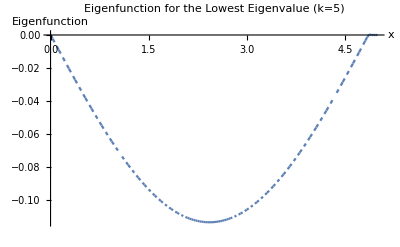

```mathematica
k=5; (*Resolution index*)
nMax=155; (*Number of scaling functions*)
coefficients={-0.0017074049254533305,-0.003974167298013526,-0.006302774691059165,-0.008605106215475535,-0.010890014855650172,-0.013167397102463209,-0.01543944554931554,-0.017705465388003383,-0.019964356103788862,-0.022215112635389715,-0.024456800940875788,-0.026688507582845834,-0.0289093236986373,-0.03111834364202548,-0.03331466609186284,-0.03549739483287986,-0.0376656392099534,-0.039818514489297484,-0.04195514221127153,-0.0440746505460312,-0.046176174648937335,-0.04825885701355909,-0.05032184782163955,-0.052364305289871516,-0.05438539601337909,-0.05638429530577846,-0.058360187535683214,-0.06031226645951512,-0.06223973555048315,-0.06414180832359906,-0.0660177086565948,-0.06786667110661201,-0.0696879412225323,-0.07148077585282452,-0.07324444344878053,-0.07497822436301656,-0.0766814111431185,-0.07835330882031051,-0.0799932351930305,-0.08160052110529509,-0.08317451071974319,-0.08471456178524425,-0.08622004589896204,-0.08769034876276795,-0.08912487043389992,-0.09052302556976238,-0.09188424366677023,-0.09320796929313802,-0.09449366231551792,-0.0957407981193954,-0.09694886782315326,-0.09811737848571608,-0.0992458533076901,-0.1003338318259158,-0.10138087010135637,-0.10238654090024113,-0.10335043386839567,-0.1042721556986838,-0.10515133029149043,-0.10598759890818646,-0.10678062031750829,-0.10753007093479448,-0.10823564495402094,-0.10889705447258098,-0.10951402960876214,-0.11008631861186978,-0.11061368796495134,-0.11109592248007949,-0.11153282538615723,-0.11192421840920964,-0.11226994184512595,-0.1125698546248253,-0.11282383437181888,-0.11303177745214439,-0.11319359901665339,-0.11330923303563362,-0.11337863232575035,-0.11340176856929829,-0.11337863232575851,-0.11330923303564985,-0.1131935990166768,-0.11303177745217446,-0.11282383437185557,-0.11256985462486835,-0.11226994184517522,-0.11192421840926509,-0.11153282538621813,-0.11109592248014495,-0.11061368796502101,-0.11008631861194382,-0.1095140296088407,-0.10889705447266484,-0.10823564495411113,-0.10753007093489111,-0.1067806203176109,-0.10598759890829484,-0.10515133029160456,-0.1042721556988032,-0.10335043386851989,-0.10238654090036964,-0.10138087010148909,-0.1003338318260522,-0.09924585330782919,-0.0981173784858575,-0.09694886782329622,-0.09574079811953899,-0.09449366231566185,-0.09320796929328196,-0.09188424366691395,-0.09052302556990592,-0.08912487043404416,-0.08769034876291322,-0.08622004589910816,-0.08471456178539037,-0.0831745107198893,-0.08160052110544143,-0.07999323519317653,-0.07835330882045655,-0.07668141114326418,-0.07497822436316164,-0.07324444344892564,-0.07148077585296922,-0.069687941222677,-0.06786667110675643,-0.06601770865673831,-0.06414180832374083,-0.06223973555062268,-0.060312266459652264,-0.058360187535817835,-0.056384295305910645,-0.054385396013508475,-0.05236430528999729,-0.05032184782176182,-0.0482588570136773,-0.046176174649051216,-0.044074650546139876,-0.0419551422113745,-0.039818514489395024,-0.03766563921004576,-0.035497394832967474,-0.03331466609194593,-0.03111834364210389,-0.028909323698710868,-0.026688507582914453,-0.024456800940939213,-0.022215112635448127,-0.019964356103841792,-0.017705465388050432,-0.01543944554935692,-0.013167397102498524,-0.010890014855679383,-0.008605106215498823,-0.006302774691076388,-0.003974167298024514,-0.0017074049254580392};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,5},PlotLabel->"Eigenfunction for the Lowest Eigenvalue (k=5)",AxesLabel->{"x","Eigenfunction"},PlotRange->All, PlotPoints->100]
```

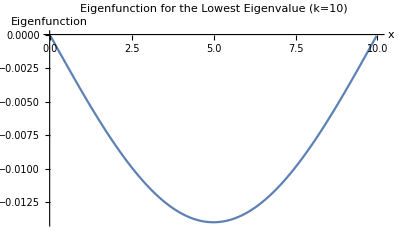

```mathematica
k=10; (*Resolution index*)
nMax=10235; (*Number of scaling functions*)
coefficients={-3.1980691314668404e-06,-7.445128549828786e-06,-1.1811028778982458e-05,-1.6132510831402366e-05,-2.0427930060292188e-05,-2.471757355547317e-05,-2.9007288536672367e-05,-3.32975092097727e-05,-3.758790550032209e-05,-4.187832085530141e-05,-4.616872557710108e-05,-5.0459121631676484e-05,-5.4749511920141626e-05,-5.9039897042743724e-05,-6.333027668491983e-05,-6.762065039130604e-05,-7.191101773163266e-05,-7.620137829650005e-05,-8.04917316820077e-05,-8.478207748451331e-05,-8.907241530001149e-05,-9.336274472434392e-05,-9.765306535332636e-05,-0.00010194337678277974,-0.00010623367860852827,-0.00011052397042639895,-0.0001148142518322198,-0.00011910452242181866,-0.00012339478179102472,-0.00012768502953566948,-0.00013197526525158556,-0.00013626548853460616,-0.00014055569898056505,-0.00014484589618529722,-0.00014913607974463984,-0.00015342624925442956,-0.00015771640431050556,-0.00016200654450870833,-0.00016629666944487914,-0.00017058677871486226,-0.00017487687191450186,-0.00017916694863964467,-0.00018345700848613886,-0.0001877470510498343,-0.0001920370759265827,-0.00019632708271223758,-0.00020061707100265213,-0.00020490704039368262,-0.0002091969904811857,-0.00021348692086102213,-0.00021777683112905293,-0.00022206672088114187,-0.00022635658971315405,-0.0002306464372209576,-0.0002349362630004205,-0.00023922606664741612,-0.0002435158477578186,-0.00024780560592750265,-0.000252095340752346,-0.00025638505182823184,-0.0002606747387510425,-0.00026496440111666253,-0.0002692540385209759,-0.00027354365055987285,-0.0002778332368292453,-0.0002821227969249867,-0.000286412330442994,-0.0002907018369791658,-0.00029499131612940595,-0.00029928076748961734,-0.00030357019065570587,-0.0003078595852235831,-0.0003121489507891593,-0.0003164382869483497,-0.00032072759329707145,-0.0003250168694312452,-0.00032930611494679505,-0.00033359532943964755,-0.00033788451250573,-0.00034217366374097633,-0.000346462782741321,-0.0003507518691027001,-0.00035504092242105603,-0.0003593299422923333,-0.0003636189283124799,-0.0003679078800774462,-0.00037219679718318447,-0.0003764856792256515,-0.0003807745258008077,-0.0003850633365046162,-0.0003893521109330476,-0.00039364084868207395,-0.0003979295493476711,-0.00040221821252581246,-0.0004065068378124809,-0.0004107954248036614,-0.00041508397309534395,-0.00041937248228352014,-0.00042366095196418155,-0.00042794938173332735,-0.0004322377711869622,-0.00043652611992109607,-0.0004408144275317369,-0.0004451026936148975,-0.00044939091776659686,-0.0004536790995828562,-0.00045796723865970066,-0.0004622553345931652,-0.00046654338697928334,-0.0004708313954140954,-0.0004751193594936402,-0.00047940727881396627,-0.00048369515297112575,-0.00048798298156117195,-0.0004922707641801661,-0.000496558500424173,-0.0005008461898892603,-0.0005051338321714995,-0.0005094214268669687,-0.0005137089735717517,-0.0005179964718819327,-0.0005222839213936011,-0.0005265713217028492,-0.0005308586724057774,-0.000535145973098491,-0.0005394332233771052,-0.0005437204228377261,-0.0005480075710764759,-0.0005522946676894804,-0.0005565817122728676,-0.0005608687044227722,-0.0005651556437353374,-0.0005694425298067077,-0.0005737293622330356,-0.0005780161406104766,-0.0005823028645351797,-0.0005865895336033091,-0.0005908761474110302,-0.0005951627055545174,-0.0005994492076299503,-0.0006037356532335149,-0.0006080220419613989,-0.0006123083734097995,-0.0006165946471749139,-0.000620880862852946,-0.0006251670200401069,-0.0006294531183326186,-0.0006337391573267007,-0.0006380251366185795,-0.0006423110558044821,-0.0006465969144806582,-0.0006508827122433513,-0.0006551684486888201,-0.0006594541234133207,-0.0006637397360131158,-0.0006680252860844742,-0.0006723107732236731,-0.0006765961970269926,-0.0006808815570907128,-0.0006851668530111258,-0.0006894520843845321,-0.0006937372508072347,-0.0006980223518755424,-0.0007023073871857726,-0.0007065923563342505,-0.0007108772589173093,-0.0007151620945312783,-0.000719446862772498,-0.0007237315632373116,-0.0007280161955220694,-0.0007323007592231328,-0.000736585253936872,-0.0007408696792596697,-0.0007451540347879096,-0.000749438320117984,-0.0007537225348462859,-0.0007580066785692049,-0.0007622907508831439,-0.0007665747513845182,-0.0007708586796697529,-0.0007751425353352777,-0.0007794263179775301,-0.0007837100271929531,-0.0007879936625779882,-0.0007922772237290841,-0.0007965607102427082,-0.0008008441217153314,-0.0008051274577434296,-0.0008094107179234831,-0.0008136939018519795,-0.0008179770091254257,-0.0008222600393403218,-0.0008265429920931767,-0.000830825866980512,-0.0008351086635988528,-0.0008393913815447325,-0.0008436740204146928,-0.0008479565798052822,-0.0008522390593130518,-0.0008565214585345634,-0.0008608037770663856,-0.000865086014505098,-0.0008693681704472901,-0.0008736502444895513,-0.0008779322362284846,-0.000882214145260697,-0.0008864959711828168,-0.0008907777135914773,-0.0008950593720833121,-0.000899340946254952,-0.0009036224357030383,-0.0009079038400242269,-0.0009121851588151789,-0.0009164663916725699,-0.0009207475381930911,-0.0009250285979734226,-0.0009293095706102699,-0.0009335904557003394,-0.0009378712528403412,-0.0009421519616269929,-0.0009464325816570336,-0.000950713112527202,-0.0009549935538342387,-0.0009592739051748992,-0.0009635541661459515,-0.0009678343363441731,-0.0009721144153663472,-0.0009763944028092618,-0.0009806742982697042,-0.0009849541013444833,-0.0009892338116304139,-0.000993513428724317,-0.0009977929522230237,-0.0010020723817233779,-0.0010063517168222356,-0.0010106309571164592,-0.0010149101022029175,-0.001019189151678493,-0.001023468105140073,-0.0010277469621845555,-0.0010320257224088437,-0.001036304385409846,-0.0010405829507844884,-0.0010448614181297056,-0.0010491397870424377,-0.001053418057119638,-0.0010576962279582728,-0.0010619742991553039,-0.0010662522703077115,-0.0010705301410124809,-0.0010748079108666123,-0.0010790855794671084,-0.00108336314641099,-0.0010876406112952778,-0.0010919179737170078,-0.0010961952332732294,-0.0011004723895609975,-0.0011047494421773756,-0.0011090263907194342,-0.0011133032347842614,-0.0011175799739689492,-0.0011218566078706044,-0.001126133136086348,-0.0011304095582133095,-0.0011346858738486266,-0.0011389620825894375,-0.001143238184032886,-0.0011475141777761335,-0.0011517900634163568,-0.001156065840550743,-0.0011603415087764843,-0.0011646170676907865,-0.0011688925168908515,-0.0011731678559739086,-0.001177443084537195,-0.0011817182021779623,-0.0011859932084934757,-0.0011902681030810044,-0.0011945428855378159,-0.001198817555461203,-0.0012030921124484668,-0.0012073665560969173,-0.001211640886003871,-0.0012159151017666467,-0.0012201892029825817,-0.0012244631892490295,-0.0012287370601633573,-0.0012330108153229549,-0.0012372844543252052,-0.0012415579767675038,-0.001245831382247262,-0.001250104670361897,-0.0012543778407088418,-0.0012586508928855314,-0.0012629238264894316,-0.001267196641118007,-0.001271469336368735,-0.001275741911839104,-0.0012800143671266129,-0.0012842867018287663,-0.0012885589155430845,-0.0012928310078670836,-0.0012971029783983097,-0.0013013748267343154,-0.0013056465524726665,-0.0013099181552109432,-0.0013141896345467312,-0.0013184609900776236,-0.0013227322214012392,-0.0013270033281152008,-0.0013312743098171512,-0.0013355451661047311,-0.0013398158965755975,-0.0013440865008274264,-0.0013483569784578995,-0.0013526273290646984,-0.0013568975522455285,-0.0013611676475981103,-0.0013654376147201764,-0.0013697074532094625,-0.0013739771626637212,-0.0013782467426807184,-0.0013825161928582312,-0.0013867855127940533,-0.0013910547020859814,-0.0013953237603318229,-0.0013995926871294075,-0.0014038614820765952,-0.0014081301447712376,-0.0014123986748111985,-0.0014166670717943506,-0.0014209353353185985,-0.0014252034649818452,-0.0014294714603820015,-0.0014337393211169979,-0.0014380070467847762,-0.0014422746369832863,-0.0014465420913104855,-0.0014508094093643607,-0.0014550765907429032,-0.0014593436350441148,-0.0014636105418660231,-0.0014678773108066504,-0.0014721439414640278,-0.0014764104334362143,-0.0014806767863212802,-0.0014849429997173182,-0.0014892090732224166,-0.0014934750064347076,-0.0014977407989523056,-0.0015020064503733473,-0.0015062719602959786,-0.0015105373283183757,-0.001514802554038715,-0.001519067637055185,-0.0015233325769659788,-0.0015275973733693072,-0.0015318620258634058,-0.0015361265340465156,-0.001540390897516898,-0.0015446551158728114,-0.0015489191887125351,-0.0015531831156343659,-0.0015574468962366124,-0.001561710530117613,-0.0015659740168757197,-0.0015702373561092742,-0.001574500547416641,-0.0015787635903961993,-0.0015830264846463265,-0.00158728922976543,-0.0015915518253519323,-0.0015958142710042688,-0.0016000765663208964,-0.0016043387109002767,-0.001608600704340892,-0.0016128625462412376,-0.0016171242361998318,-0.0016213857738151987,-0.0016256471586858895,-0.0016299083904104373,-0.001634169468587411,-0.0016384303928153989,-0.0016426911626929847,-0.0016469517778187662,-0.0016512122377913747,-0.0016554725422094647,-0.0016597326906716947,-0.0016639926827767455,-0.0016682525181232763,-0.0016725121963099933,-0.0016767717169356034,-0.0016810310795988272,-0.0016852902838983986,-0.0016895493294330865,-0.0016938082158016723,-0.0016980669426029354,-0.0017023255094356516,-0.001706583915898623,-0.0017108421615906868,-0.0017151002461106932,-0.001719358169057514,-0.0017236159300300354,-0.0017278735286271518,-0.0017321309644477657,-0.0017363882370907972,-0.00174064534615518,-0.0017449022912398744,-0.001749159071943842,-0.001753415687866075,-0.0017576721386055652,-0.0017619284237613275,-0.0017661845429324055,-0.001770440495717865,-0.0017746962817167587,-0.001778951900528163,-0.0017832073517511768,-0.001787462634984902,-0.001791717749828453,-0.0017959726958809688,-0.0018002274727416184,-0.0018044820800095732,-0.0018087365172840214,-0.0018129907841641598,-0.0018172448802492094,-0.0018214988051384105,-0.0018257525584309965,-0.001830006139726241,-0.0018342595486234455,-0.0018385127847219112,-0.0018427658476209512,-0.0018470187369198955,-0.0018512714522181141,-0.0018555239931149542,-0.0018597763592098115,-0.0018640285501020765,-0.0018682805653911845,-0.0018725324046765597,-0.0018767840675576585,-0.0018810355536339521,-0.001885286862504931,-0.0018895379937700842,-0.0018937889470289307,-0.001898039721881011,-0.001902290317925858,-0.001906540734763032,-0.001910790971992126,-0.0019150410292127318,-0.0019192909060244553,-0.001923540602026939,-0.0019277901168198227,-0.001932039450002789,-0.001936288601175539,-0.001940537569937786,-0.001944786355889246,-0.0019490349586296376,-0.0019532833777587064,-0.0019575316128762443,-0.0019617796635820295,-0.001966027529475869,-0.001970275210157588,-0.001974522705227038,-0.0019787700142840873,-0.0019830171369286044,-0.0019872640727604794,-0.0019915108213796116,-0.00199575738238593,-0.0020000037553793825,-0.002004249939959938,-0.0020084959357275834,-0.0020127417422823204,-0.002016987359224178,-0.002021232786153183,-0.0020254780226693935,-0.0020297230683729026,-0.0020339679228638056,-0.0020382125857421967,-0.0020424570566081966,-0.0020467013350619298,-0.002050945420703552,-0.002055189313133243,-0.00205943301195123,-0.0020636765167577316,-0.0020679198271530003,-0.002072162942737281,-0.002076405863110853,-0.0020806485878740056,-0.002084891116627041,-0.002089133448970297,-0.002093375584504128,-0.0020976175228289073,-0.0021018592635450102,-0.0021061008062528406,-0.002110342150552814,-0.0021145832960453616,-0.002118824242330925,-0.0021230649890099707,-0.002127305535683,-0.0021315458819505294,-0.0021357860274130924,-0.002140025971671241,-0.0021442657143255573,-0.002148505254976638,-0.002152744593225098,-0.002156983728671557,-0.00216122266091666,-0.002165461389561076,-0.0021696999142054763,-0.002173938234450582,-0.0021781763498970883,-0.00218241426014576,-0.0021866519647973552,-0.002190889463452654,-0.0021951267557124305,-0.002199363841177517,-0.002203600719448754,-0.002207837390127017,-0.0022120738528131926,-0.0022163101071081734,-0.0022205461526128767,-0.0022247819889282274,-0.0022290176156551924,-0.0022332530323947502,-0.0022374882387479027,-0.0022417232343156655,-0.002245958018699063,-0.002250192591499163,-0.002254426952317042,-0.0022586611007537768,-0.002262895036410504,-0.002267128758888348,-0.0022713622677884514,-0.0022755955627120133,-0.002279828643260216,-0.0022840615090342813,-0.0022882941596354366,-0.002292526594664946,-0.002296758813724096,-0.002300990816414199,-0.002305222602336565,-0.002309454171092531,-0.0023136855222834593,-0.002317916655510717,-0.0023221475703757,-0.0023263782664798274,-0.002330608743424552,-0.002334839000811342,-0.002339069038241673,-0.0023432988553170548,-0.0023475284516390324,-0.002351757826809138,-0.0023559869804289347,-0.0023602159121000215,-0.002364444621423999,-0.0023686731080025027,-0.0023729013714371707,-0.0023771294113296816,-0.0023813572272817214,-0.002385584818895026,-0.00238981218577132,-0.002394039327512386,-0.002398266243719997,-0.002402492933995928,-0.002406719397941996,-0.0024109456351600334,-0.0024151716452519324,-0.002419397427819571,-0.002423622982464855,-0.0024278483087897033,-0.002432073406396043,-0.002436298274885841,-0.002440522913861101,-0.0024447473229238393,-0.002448971501676085,-0.002453195449719891,-0.002457419166657322,-0.0024616426520905005,-0.0024658659056215507,-0.0024700889268526433,-0.00247431171538592,-0.002478534270823553,-0.002482756592767715,-0.0024869786808206463,-0.0024912005345845978,-0.0024954221536618473,-0.0024996435376546757,-0.0025038646861654185,-0.0025080855987964406,-0.0025123062751501077,-0.0025165267148287815,-0.002520746917434898,-0.0025249668825708784,-0.0025291866098391884,-0.0025334060988423035,-0.002537625349182723,-0.002541844360462966,-0.002546063132285582,-0.0025502816642531206,-0.002554499955968183,-0.002558718007033359,-0.0025629358170512757,-0.0025671533856245704,-0.002571370712355931,-0.0025755877968480765,-0.002579804638703726,-0.002584021237525635,-0.0025882375929165563,-0.00259245370447929,-0.002596669571816628,-0.0026008851945314325,-0.002605100572226552,-0.0026093157045048803,-0.0026135305909693158,-0.0026177452312227934,-0.0026219596248682497,-0.0026261737715086763,-0.0026303876707470886,-0.002634601322186541,-0.0026388147254300825,-0.002643027880080773,-0.002647240785741717,-0.0026514534420160126,-0.0026556658485067837,-0.002659878004817189,-0.0026640899105504134,-0.0026683015653096607,-0.002672512968698177,-0.0026767241203192083,-0.00268093501977604,-0.0026851456666719615,-0.002689356060610335,-0.0026935662011945373,-0.0026977760880279567,-0.00270198572071399,-0.002706195098856038,-0.002710404222057534,-0.002714613089921946,-0.002718821702052793,-0.0027230300580535884,-0.0027272381575278596,-0.0027314460000791925,-0.00273565358531121,-0.0027398609128275503,-0.0027440679822318187,-0.0027482747931276788,-0.0027524813451188348,-0.0027566876378090125,-0.0027608936708019586,-0.0027650994437014315,-0.00276930495611122,-0.0027735102076351494,-0.0027777151978770603,-0.002781919926440819,-0.0027861243929303025,-0.0027903285969493995,-0.0027945325381020522,-0.002798736215992218,-0.0028029396302239108,-0.0028071427804011407,-0.0028113456661279386,-0.0028155482870083695,-0.0028197506426465052,-0.002823952732646467,-0.002828154556612392,-0.0028323561141484375,-0.002836557404858803,-0.0028407584283476834,-0.002844959184219324,-0.002849159672077984,-0.002853359891527936,-0.0028575598421734898,-0.0028617595236189865,-0.0028659589354688274,-0.0028701580773274047,-0.0028743569487991246,-0.0028785555494884106,-0.0028827538789997307,-0.0028869519369375822,-0.0028911497229064933,-0.002895347236510986,-0.002899544477355631,-0.002903741445045023,-0.002907938139183776,-0.0029121345593765315,-0.002916330705227976,-0.0029205265763428048,-0.0029247221723257286,-0.0029289174927815157,-0.0029331125373149346,-0.00293730730553078,-0.002941501797033859,-0.0029456960114290264,-0.002949889948321159,-0.002954083607315183,-0.002958276988016041,-0.002962470090028696,-0.0029666629129581233,-0.0029708554564093124,-0.002975047719987304,-0.0029792397032971634,-0.002983431405943976,-0.0029876228275328557,-0.002991813967668974,-0.002996004825957481,-0.003000195402003576,-0.003004385695412482,-0.0030085757057894164,-0.003012765432739655,-0.0030169548758685106,-0.003021144034781292,-0.003025332909083355,-0.00302952149838009,-0.0030337098022768863,-0.003037897820379187,-0.0030420855522924574,-0.003046272997622213,-0.0030504601559739795,-0.0030546470269533043,-0.0030588336101657473,-0.0030630199052169116,-0.0030672059117124234,-0.0030713916292579553,-0.0030755770574591745,-0.0030797621959217938,-0.003083947044251558,-0.0030881316020542077,-0.0030923158689355142,-0.003096499844501304,-0.003100683528357434,-0.0031048669201097826,-0.0031090500193642493,-0.003113232825726742,-0.0031174153388032065,-0.0031215975581996027,-0.0031257794835219664,-0.0031299611143763345,-0.003134142450368792,-0.0031383234911054295,-0.003142504236192363,-0.003146684685235735,-0.0031508648378417037,-0.0031550446936164677,-0.003159224252166293,-0.003163403513097429,-0.003167582476016139,-0.003171761140528762,-0.00317593950624163,-0.003180117572761133,-0.003184295339693667,-0.0031884728066456764,-0.003192649973223603,-0.0031968268390339446,-0.003201003403683184,-0.0032051796667778455,-0.0032093556279245037,-0.003213531286729801,-0.003217706642800362,-0.0032218816957428533,-0.0032260564451639467,-0.0032302308906703445,-0.0032344050318687855,-0.003238578868366036,-0.0032427523997688875,-0.0032469256256841537,-0.003251098545718672,-0.0032552711594792966,-0.0032594434665729464,-0.0032636154666065864,-0.0032677871591871984,-0.003271958543921776,-0.003276129620417373,-0.003280300388281051,-0.0032844708471198975,-0.0032886409965410474,-0.003292810836151654,-0.0032969803655588836,-0.0033011495843699216,-0.003305318492191992,-0.0033094870886323843,-0.003313655373298384,-0.0033178233457973137,-0.0033219910057365096,-0.003326158352723347,-0.0033303253863652296,-0.00333449210626962,-0.0033386585120439927,-0.0033428246032958576,-0.0033469903796327707,-0.0033511558406622804,-0.003355320985991943,-0.0033594858152293733,-0.0033636503279822283,-0.0033678145238581793,-0.003371978402464943,-0.0033761419634102266,-0.0033803052063017865,-0.003384468130747432,-0.0033886307363549927,-0.0033927930227323137,-0.0033969549894872853,-0.0034011166362278252,-0.003405277962561876,-0.0034094389680974393,-0.0034135996524425325,-0.0034177600152051923,-0.003421920055993497,-0.0034260797744155086,-0.003430239170079369,-0.0034343982425932337,-0.003438556991565292,-0.0034427154166037405,-0.003446873517316855,-0.0034510312933128838,-0.00345518874420015,-0.003459345869587017,-0.003463502669081853,-0.0034676591422930485,-0.0034718152888290406,-0.0034759711082983148,-0.003480126600309345,-0.003484281764470688,-0.0034884366003909094,-0.003492591107678611,-0.0034967452859424133,-0.0035008991347909297,-0.0035050526538328384,-0.003509205842676834,-0.003513358700931635,-0.003517511228206038,-0.003521663424108864,-0.003525815288248964,-0.0035299668202351947,-0.003534118019676472,-0.003538268886181695,-0.0035424194193598188,-0.003546569618819844,-0.0035507194841708366,-0.003554869015021854,-0.003559018210981982,-0.0035631670716603117,-0.0035673155966660045,-0.003571463785608262,-0.00357561163809629,-0.0035797591537393442,-0.003583906332146695,-0.003588053172927605,-0.0035921996756914185,-0.0035963458400475215,-0.003600491665605345,-0.003604637151974333,-0.003608782298763938,-0.0036129271055836453,-0.003617071572043003,-0.003621215697751571,-0.003625359482318978,-0.00362950292535486,-0.003633646026468879,-0.0036377887852706886,-0.0036419312013700124,-0.0036460732743765875,-0.0036502150039002313,-0.0036543563895507767,-0.0036584974309380952,-0.003662638127672075,-0.0036667784793626016,-0.003670918485619631,-0.003675058146053155,-0.0036791974602731954,-0.0036833364278897863,-0.003687475048513006,-0.0036916133217530216,-0.003695751247219948,-0.003699888824523947,-0.003704026053275213,-0.0037081629330839977,-0.003712299463560613,-0.00371643564431536,-0.003720571474958585,-0.00372470695510064,-0.003728842084351935,-0.0037329768623229104,-0.0037371112886240825,-0.0037412453628659953,-0.0037453790846592276,-0.003749512453614325,-0.0037536454693418804,-0.0037577781314525353,-0.0037619104395569688,-0.0037660423932658815,-0.003770173992190043,-0.003774305235940192,-0.0037784361241271374,-0.003782566656361742,-0.003786696832254905,-0.0037908266514175342,-0.0037949561134605803,-0.003799085217995038,-0.0038032139646319327,-0.0038073423529822897,-0.003811470382657185,-0.0038155980532677317,-0.0038197253644250803,-0.0038238523157403913,-0.0038279789068248952,-0.0038321051372898385,-0.0038362310067464765,-0.003840356514806134,-0.0038444816610801636,-0.0038486064451799568,-0.003852730866716962,-0.0038568549253026494,-0.0038609786205484895,-0.003865101952065971,-0.003869224919466694,-0.0038733475223622364,-0.003877469760364221,-0.0038815916330843217,-0.0038857131401341975,-0.0038898342811255725,-0.003893955055670234,-0.0038980754633799594,-0.003902195503866558,-0.003906315176741904,-0.003910434481617878,-0.003914553418106394,-0.003918671985819401,-0.003922790184368934,-0.003926908013367043,-0.003931025472425827,-0.003935142561157377,-0.003939259279173849,-0.003943375626087436,-0.003947491601510337,-0.0039516072050548075,-0.003955722436333147,-0.003959837294957664,-0.003963951780540711,-0.003968065892694662,-0.003972179631031969,-0.00397629299516511,-0.0039804059847065795,-0.003984518599268929,-0.0039886308384646406,-0.003992742701906305,-0.003996854189206549,-0.0040009652999780715,-0.00400507603383363,-0.004009186390386007,-0.00401329636924798,-0.004017405970032358,-0.004021515192351995,-0.004025624035819744,-0.004029732500048533,-0.004033840584651307,-0.0040379482892410655,-0.004042055613430805,-0.0040461625568335964,-0.004050269119062505,-0.00405437529973069,-0.004058481098451343,-0.00406258651483765,-0.004066691548502858,-0.004070796199060269,-0.004074900466123207,-0.004079004349305,-0.004083107848218997,-0.004087210962478599,-0.004091313691697281,-0.004095416035488569,-0.004099517993466012,-0.004103619565243188,-0.004107720750433716,-0.00411182154865123,-0.0041159219595093945,-0.0041200219826219376,-0.004124121617602611,-0.0041282208640652,-0.004132319721623522,-0.004136418189891444,-0.004140516268482854,-0.0041446139570117235,-0.0041487112550920155,-0.004152808162337757,-0.004156904678363012,-0.004161000802781862,-0.004165096535208403,-0.004169191875256796,-0.004173286822541199,-0.0041773813766758415,-0.004181475537274987,-0.0041855693039529315,-0.004189662676324031,-0.00419375565400266,-0.004197848236603211,-0.004201940423740164,-0.004206032215028001,-0.00421012361008126,-0.004214214608514515,-0.004218305209942411,-0.004222395413979595,-0.004226485220240742,-0.004230574628340533,-0.004234663637893712,-0.004238752248515068,-0.004242840459819427,-0.004246928271421671,-0.004251015682936754,-0.004255102693979615,-0.004259189304165224,-0.0042632755131085534,-0.004267361320424632,-0.004271446725728597,-0.004275531728635581,-0.004279616328760738,-0.004283700525719278,-0.004287784319126423,-0.00429186770859747,-0.004295950693747731,-0.0043000332741925835,-0.00430411544954742,-0.0043081972194276485,-0.004312278583448717,-0.00431635954122615,-0.004320440092375498,-0.004324520236512381,-0.00432859997325242,-0.00433267930221126,-0.004336758223004602,-0.004340836735248171,-0.004344914838557739,-0.0043489925325490945,-0.004353069816838064,-0.004357146691040532,-0.004361223154772455,-0.004365299207649813,-0.004369374849288587,-0.004373450079304833,-0.004377524897314623,-0.004381599302934101,-0.004385673295779423,-0.004389746875466824,-0.004393820041612572,-0.004397892793832958,-0.004401965131744292,-0.004406037054962914,-0.004410108563105206,-0.004414179655787607,-0.004418250332626609,-0.004422320593238781,-0.004426390437240673,-0.004430459864248857,-0.00443452887387994,-0.004438597465750623,-0.0044426656394776325,-0.004446733394677725,-0.004450800730967683,-0.004454867647964303,-0.004458934145284442,-0.004463000222545008,-0.004467065879363003,-0.0044711311153554445,-0.004475195930139402,-0.004479260323331918,-0.004483324294550107,-0.00448738784341107,-0.00449145096953198,-0.0044955136725301215,-0.004499575952022787,-0.004503637807627285,-0.004507699238960954,-0.004511760245641134,-0.0045158208272852544,-0.004519880983510768,-0.004523940713935171,-0.004528000018176031,-0.004532058895850925,-0.004536117346577501,-0.004540175369973432,-0.004544232965656445,-0.004548290133244256,-0.0045523468723546465,-0.004556403182605472,-0.004560459063614605,-0.004564514514999962,-0.004568569536379504,-0.0045726241273712194,-0.004576678287593115,-0.0045807320166632096,-0.004584785314199626,-0.004588838179820519,-0.00459289061314412,-0.004596942613788647,-0.004600994181372348,-0.004605045315513529,-0.004609096015830571,-0.004613146281941901,-0.004617196113465974,-0.004621245510021292,-0.004625294471226376,-0.004629342996699792,-0.0046333910860601926,-0.004637438738926212,-0.004641485954916504,-0.004645532733649785,-0.004649579074744843,-0.004653624977820473,-0.004657670442495534,-0.004661715468388907,-0.004665760055119508,-0.004669804202306313,-0.0046738479095683565,-0.004677891176524709,-0.004681934002794456,-0.004685976387996742,-0.004690018331750721,-0.004694059833675631,-0.004698100893390723,-0.004702141510515349,-0.004706181684668827,-0.0047102214154705405,-0.00471426070253989,-0.004718299545496308,-0.0047223379439593136,-0.004726375897548488,-0.004730413405883389,-0.004734450468583689,-0.004738487085269109,-0.004742523255559359,-0.004746558979074227,-0.004750594255433502,-0.004754629084257038,-0.004758663465164742,-0.004762697397776496,-0.004766730881712245,-0.004770763916592044,-0.004774796502036007,-0.00477882863766426,-0.004782860323096961,-0.004786891557954295,-0.004790922341856491,-0.004794952674423802,-0.0047989825552766045,-0.004803011984035225,-0.004807040960320063,-0.004811069483751571,-0.004815097553950245,-0.0048191251705366435,-0.004823152333131325,-0.004827179041354898,-0.004831205294827999,-0.004835231093171299,-0.00483925643600556,-0.004843281322951565,-0.004847305753630135,-0.00485132972766222,-0.004855353244668722,-0.004859376304270598,-0.004863398906088831,-0.004867421049744454,-0.004871442734858546,-0.0048754639610522395,-0.0048794847279466915,-0.004883505035163181,-0.004887524882323001,-0.004891544269047449,-0.004895563194957838,-0.004899581659675537,-0.004903599662821966,-0.004907617204018605,-0.004911634282886981,-0.004915650899048628,-0.004919667052125111,-0.004923682741738089,-0.004927697967509272,-0.0049317127290604374,-0.004935727026013403,-0.00493974085799,-0.004943754224612155,-0.004947767125501819,-0.004951779560280956,-0.004955791528571597,-0.004959803029995745,-0.004963814064175481,-0.004967824630732907,-0.004971834729290213,-0.004975844359469601,-0.004979853520893362,-0.004983862213183803,-0.004987870435963243,-0.0049918781888540565,-0.004995885471478684,-0.004999892283459648,-0.005003898624419451,-0.005007904493980634,-0.005011909891765834,-0.005015914817397712,-0.005019919270498951,-0.005023923250692338,-0.005027926757600673,-0.0050319297908468594,-0.005035932350053761,-0.005039934434844279,-0.005043936044841386,-0.0050479371796681065,-0.005051937838947444,-0.00505593802230255,-0.005059937729356603,-0.005063936959732838,-0.00506793571305453,-0.0050719339889449475,-0.005075931787027422,-0.005079929106925343,-0.005083925948262105,-0.005087922310661154,-0.005091918193746024,-0.005095913597140338,-0.005099908520467717,-0.005103902963351838,-0.005107896925416389,-0.0051118904062850985,-0.005115883405581735,-0.005119875922930141,-0.005123867957954172,-0.005127859510277762,-0.005131850579524826,-0.005135841165319417,-0.005139831267285634,-0.005143820885047599,-0.00514781001822943,-0.005151798666455329,-0.005155786829349555,-0.005159774506536375,-0.005163761697640118,-0.005167748402285134,-0.005171734620095842,-0.005175720350696712,-0.005179705593712275,-0.00518369034876704,-0.005187674615485612,-0.005191658393492646,-0.005195641682412905,-0.005199624481871163,-0.0052036067914922575,-0.0052075886109010355,-0.005211569939722415,-0.00521555077758129,-0.005219531124102631,-0.005223510978911491,-0.005227490341632918,-0.005231469211892078,-0.00523544758931416,-0.005239425473524366,-0.005243402864147884,-0.005247379760810006,-0.005251356163136082,-0.005255332070751553,-0.005259307483281841,-0.005263282400352459,-0.005267256821588998,-0.005271230746617041,-0.00527520417506219,-0.00527917710655009,-0.005283149540706477,-0.0052871214771571,-0.005291092915527748,-0.005295063855444292,-0.005299034296532627,-0.00530300423841866,-0.00530697368072844,-0.005310942623088015,-0.005314911065123499,-0.005318879006461035,-0.0053228464467268465,-0.005326813385547236,-0.0053307798225485006,-0.005334745757356937,-0.005338711189598906,-0.00534267611890079,-0.005346640544889056,-0.005350604467190285,-0.005354567885431053,-0.005358530799237991,-0.005362493208237749,-0.0053664551120570555,-0.005370416510322655,-0.005374377402661392,-0.005378337788700145,-0.005382297668065816,-0.005386257040385378,-0.005390215905285827,-0.005394174262394217,-0.005398132111337667,-0.005402089451743343,-0.005406046283238446,-0.00541000260545016,-0.005413958418005778,-0.0054179137205326005,-0.005421868512657979,-0.005425822794009371,-0.005429776564214236,-0.005433729822900144,-0.0054376825696946865,-0.0054416348042255125,-0.00544558652612026,-0.00544953773500663,-0.0054534884305123725,-0.005457438612265299,-0.005461388279893373,-0.005465337433024528,-0.005469286071286691,-0.0054732341943078714,-0.005477181801716151,-0.0054811288931396925,-0.0054850754682066235,-0.005489021526545139,-0.00549296706778346,-0.005496912091549893,-0.005500856597472796,-0.005504800585180605,-0.005508744054301753,-0.005512687004464812,-0.005516629435298257,-0.005520571346430722,-0.005524512737490809,-0.00552845360810723,-0.005532393957908764,-0.005536333786524175,-0.0055402730935823355,-0.005544211878712142,-0.005548150141542551,-0.005552087881702555,-0.005556025098821177,-0.005559961792527476,-0.0055638979624506035,-0.005567833608219716,-0.0055717687294640885,-0.005575703325813003,-0.005579637396895797,-0.00558357094234184,-0.005587503961780582,-0.005591436454841482,-0.005595368421154087,-0.005599299860348006,-0.005603230772052806,-0.005607161155898178,-0.005611091011513813,-0.0056150203385294814,-0.005618949136575002,-0.00562287740528029,-0.005626805144275316,-0.005630732353190077,-0.005634659031654613,-0.005638585179299003,-0.0056425107957534075,-0.005646435880647992,-0.005650360433612951,-0.00565428445427856,-0.005658207942275108,-0.005662130897232926,-0.00566605331878248,-0.005669975206554286,-0.005673896560178887,-0.00567781737928685,-0.005681737663508827,-0.005685657412475509,-0.005689576625817618,-0.00569349530316593,-0.0056974134441512385,-0.005701331048404448,-0.005705248115556477,-0.005709164645238341,-0.005713080637081091,-0.0057169960907158465,-0.0057209110057737855,-0.005724825381886156,-0.0057287392186842,-0.005732652515799193,-0.005736565272862448,-0.00574047748950539,-0.005744389165359459,-0.005748300300056127,-0.005752210893226997,-0.005756120944503602,-0.005760030453517592,-0.0057639394199006525,-0.005767847843284545,-0.005771755723301055,-0.005775663059582036,-0.0057795698517594096,-0.00578347609946512,-0.005787381802331158,-0.005791286959989573,-0.005795191572072487,-0.005799095638212084,-0.0058029991580406,-0.005806902131190279,-0.005810804557293427,-0.0058147064359823685,-0.005818607766889529,-0.0058225085496474,-0.005826408783888527,-0.0058303084692455315,-0.005834207605351002,-0.005838106191837636,-0.005842004228338092,-0.005845901714485143,-0.005849798649911624,-0.005853695034250417,-0.005857590867134491,-0.005861486148196816,-0.005865380877070408,-0.00586927505338834,-0.005873168676783789,-0.005877061746889949,-0.005880954263340053,-0.005884846225767447,-0.005888737633805541,-0.005892628487087669,-0.005896518785247289,-0.005900408527917904,-0.005904297714733077,-0.005908186345326439,-0.005912074419331681,-0.005915961936382513,-0.005919848896112712,-0.005923735298156104,-0.005927621142146581,-0.005931506427718092,-0.005935391154504613,-0.005939275322140132,-0.0059431589302587195,-0.005947041978494521,-0.005950924466481726,-0.0059548063938546164,-0.005958687760247484,-0.005962568565294697,-0.005966448808630589,-0.005970328489889592,-0.005974207608706209,-0.005978086164714997,-0.005981964157550628,-0.005985841586847815,-0.005989718452241293,-0.005993594753365812,-0.005997470489856274,-0.006001345661347538,-0.006005220267474523,-0.006009094307872192,-0.0060129677821755805,-0.006016840690019802,-0.006020713031040043,-0.006024584804871493,-0.006028456011149401,-0.006032326649509053,-0.0060361967195858195,-0.006040066221015103,-0.006043935153432375,-0.006047803516473142,-0.006051671309772937,-0.006055538532967367,-0.006059405185692097,-0.006063271267582896,-0.006067136778275569,-0.006071001717406019,-0.006074866084610169,-0.006078729879523985,-0.006082593101783456,-0.0060864557510246714,-0.006090317826883749,-0.006094179328996809,-0.006098040257000059,-0.006101900610529757,-0.006105760389222263,-0.006109619592713984,-0.006113478220641311,-0.006117336272640742,-0.006121193748348796,-0.006125050647402073,-0.006128906969437243,-0.006132762714091041,-0.0061366178810002584,-0.006140472469801753,-0.006144326480132402,-0.006148179911629152,-0.006152032763928934,-0.006155885036668761,-0.006159736729485678,-0.0061635878420168485,-0.006167438373899479,-0.006171288324770858,-0.006175137694268294,-0.006178986482029111,-0.006182834687690682,-0.006186682310890494,-0.006190529351266114,-0.006194375808455143,-0.0061982216820952035,-0.006202066971823973,-0.0062059116772792125,-0.006209755798098697,-0.006213599333920275,-0.006217442284381807,-0.00622128464912131,-0.006225126427776853,-0.006228967619986574,-0.0062328082253885935,-0.006236648243621121,-0.006240487674322458,-0.006244326517130858,-0.006248164771684649,-0.0062520024376222305,-0.006255839514582054,-0.006259676002202657,-0.006263511900122547,-0.006267347207980345,-0.00627118192541481,-0.006275016052064717,-0.006278849587568858,-0.00628268253156605,-0.006286514883695162,-0.0062903466435951716,-0.006294177810905132,-0.00629800838526408,-0.006301838366311159,-0.006305667753685557,-0.00630949654702658,-0.006313324745973526,-0.0063171523501657665,-0.006320979359242744,-0.006324805772843866,-0.006328631590608643,-0.00633245681217671,-0.006336281437187712,-0.006340105465281334,-0.006343928896097307,-0.006347751729275441,-0.006351573964455571,-0.006355395601277627,-0.006359216639381596,-0.006363037078407534,-0.006366856917995571,-0.0063706761577858465,-0.0063744947974185085,-0.006378312836533791,-0.006382130274772043,-0.0063859471117736835,-0.006389763347179147,-0.006393578980628927,-0.006397394011763558,-0.006401208440223619,-0.00640502226564974,-0.006408835487682637,-0.006412648105963074,-0.006416460120131909,-0.0064202715298299785,-0.006424082334698239,-0.0064278925343777445,-0.0064317021285095295,-0.00643551111673467,-0.006439319498694315,-0.0064431272740297085,-0.0064469344423821445,-0.006450741003393042,-0.0064545469567038145,-0.006458352301955885,-0.006462157038790811,-0.006465961166850169,-0.0064697646857756015,-0.006473567595208746,-0.0064773698947913185,-0.006481171584165104,-0.006484972662971902,-0.006488773130853594,-0.006492572987452124,-0.006496372232409533,-0.0065001708653679375,-0.0065039688859695535,-0.006507766293856546,-0.006511563088671215,-0.00651535927005589,-0.006519154837652971,-0.006522949791104907,-0.006526744130054151,-0.0065305378541432105,-0.006534330963014643,-0.00653812345631114,-0.006541915333675452,-0.006545706594750346,-0.0065494972391786374,-0.006553287266603206,-0.006557076676667038,-0.006560865469013157,-0.006564653643284666,-0.006568441199124697,-0.00657222813617642,-0.006576014454083084,-0.006579800152488014,-0.006583585231034648,-0.006587369689366407,-0.00659115352712671,-0.006594936743959085,-0.00659871933950715,-0.006602501313414596,-0.006606282665325152,-0.006610063394882537,-0.00661384350173047,-0.00661762298551284,-0.0066214018458736435,-0.0066251800824569,-0.006628957694906716,-0.006632734682867236,-0.006636511045982667,-0.006640286783897183,-0.006644061896255062,-0.006647836382700644,-0.006651610242878353,-0.006655383476432689,-0.0066591560830081865,-0.0066629280622494185,-0.006666699413801064,-0.006670470137307851,-0.0066742402324145725,-0.006678009698766127,-0.006681778536007376,-0.006685546743783308,-0.006689314321738921,-0.006693081269519302,-0.006696847586769588,-0.006700613273134922,-0.006704378328260498,-0.006708142751791665,-0.006711906543373747,-0.006715669702652187,-0.006719432229272402,-0.006723194122879946,-0.00672695538312041,-0.006730716009639547,-0.006734476002083131,-0.00673823536009698,-0.006741994083326934,-0.006745752171418847,-0.006749509624018681,-0.006753266440772455,-0.006757022621326289,-0.006760778165326259,-0.00676453307241853,-0.006768287342249328,-0.006772040974465002,-0.0067757939687120156,-0.006779546324636816,-0.006783298041885953,-0.006787049120105977,-0.006790799558943519,-0.006794549358045293,-0.006798298517058036,-0.006802047035628491,-0.0068057949134035485,-0.00680954215003012,-0.00681328874515517,-0.006817034698425751,-0.006820780009488995,-0.006824524677992074,-0.0068282687035821805,-0.006832012085906612,-0.006835754824612735,-0.0068394969193480305,-0.006843238369759952,-0.0068469791754959776,-0.0068507193362037,-0.006854458851530799,-0.006858197721125002,-0.006861935944634066,-0.0068656735217057915,-0.006869410451988103,-0.006873146735128937,-0.006876882370776349,-0.006880617358578407,-0.006884351698183275,-0.006888085389239132,-0.006891818431394285,-0.006895550824297045,-0.006899282567595799,-0.006903013660938888,-0.006906744103974771,-0.006910473896351983,-0.006914203037719196,-0.006917931527725118,-0.006921659366018475,-0.0069253865522480584,-0.006929113086062786,-0.006932838967111651,-0.006936564195043648,-0.0069402887695078795,-0.006944012690153479,-0.006947735956629642,-0.006951458568585631,-0.0069551805256707734,-0.006958901827534447,-0.006962622473826049,-0.006966342464195073,-0.006970061798291067,-0.006973780475763673,-0.006977498496262538,-0.006981215859437354,-0.006984932564937885,-0.0069886486124139885,-0.006992364001515614,-0.006996078731892747,-0.006999792803195456,-0.0070035062150739175,-0.007007218967178292,-0.007010931059158802,-0.007014642490665783,-0.007018353261349553,-0.007022063370860526,-0.007025772818849148,-0.00702948160496598,-0.00703318972886165,-0.007036897190186817,-0.007040603988592219,-0.007044310123728642,-0.007048015595247014,-0.007051720402798211,-0.007055424546033119,-0.007059128024602792,-0.007062830838158372,-0.007066532986351051,-0.007070234468832067,-0.007073935285252715,-0.007077635435264339,-0.0070813349185183715,-0.007085033734666367,-0.007088731883359821,-0.007092429364250373,-0.00709612617698965,-0.007099822321229311,-0.007103517796621185,-0.007107212602817209,-0.007110906739469363,-0.007114600206229588,-0.007118293002749936,-0.007121985128682465,-0.00712567658367936,-0.007129367367392887,-0.007133057479475375,-0.0071367469195792056,-0.007140435687356756,-0.007144123782460488,-0.007147811204543032,-0.007151497953257039,-0.007155184028255232,-0.007158869429190293,-0.007162554155715005,-0.007166238207482248,-0.00716992158414497,-0.007173604285356236,-0.007177286310769132,-0.00718096766003672,-0.007184648332812202,-0.007188328328748828,-0.0071920076474999055,-0.007195686288718744,-0.007199364252058829,-0.007203041537173694,-0.007206718143716933,-0.0072103940713422075,-0.007214069319703222,-0.007217743888453749,-0.007221417777247559,-0.007225090985738587,-0.0072287635135808125,-0.007232435360428296,-0.0072361065259351435,-0.007239777009755412,-0.0072434468115432785,-0.007247115930953074,-0.007250784367639161,-0.007254452121256031,-0.0072581191914581405,-0.007261785577900046,-0.007265451280236368,-0.007269116298121761,-0.007272780631210952,-0.007276444279158804,-0.007280107241620151,-0.007283769518249822,-0.007287431108702684,-0.007291092012633777,-0.007294752229698213,-0.0072984117595512165,-0.007302070601848051,-0.007305728756244067,-0.007309386222394622,-0.0073130429999551765,-0.007316699088581337,-0.007320354487928677,-0.007324009197652802,-0.007327663217409499,-0.007331316546854535,-0.007334969185643748,-0.007338621133432995,-0.007342272389878219,-0.00734592295463541,-0.007349572827360718,-0.007353222007710203,-0.007356870495340093,-0.0073605182899067305,-0.0073641653910664516,-0.0073678117984757535,-0.007371457511791137,-0.007375102530669105,-0.0073787468547661965,-0.007382390483739144,-0.007386033417244626,-0.007389675654939477,-0.007393317196480568,-0.007396958041524881,-0.007400598189729388,-0.0074042376407511745,-0.007407876394247359,-0.007411514449875144,-0.007415151807291846,-0.00741878846615481,-0.007422424426121434,-0.007426059686849274,-0.0074296942479958675,-0.007433328109218754,-0.00743696127017566,-0.007440593730524306,-0.0074442254899224885,-0.007447856548028065,-0.007451486904498858,-0.007455116558992838,-0.007458745511168141,-0.0074623737606829684,-0.007466001307195524,-0.007469628150364125,-0.007473254289846972,-0.0074768797253024185,-0.007480504456388905,-0.007484128482765005,-0.0074877518040893645,-0.007491374420020622,-0.007494996330217413,-0.007498617534338531,-0.007502238032042915,-0.007505857822989527,-0.007509476906837391,-0.007513095283245492,-0.007516712951872922,-0.0075203299123788505,-0.007523946164422564,-0.007527561707663406,-0.00753117654176076,-0.007534790666374061,-0.007538404081162904,-0.007542016785786837,-0.00754562877990548,-0.007549240063178557,-0.007552850635265861,-0.0075564604958272075,-0.007560069644522537,-0.007563678081011858,-0.00756728580495521,-0.007570892816012759,-0.00757449911384477,-0.007578104698111538,-0.007581709568473372,-0.007585313724590694,-0.007588917166123953,-0.007592519892733701,-0.007596121904080575,-0.00759972319982525,-0.007603323779628421,-0.007606923643150852,-0.007610522790053391,-0.007614121219996969,-0.007617718932642612,-0.007621315927651471,-0.0076249122046847286,-0.007628507763403554,-0.007632102603469148,-0.007635696724542915,-0.007639290126286274,-0.007642882808360735,-0.007646474770427809,-0.007650066012149105,-0.0076536565331863735,-0.00765724633320129,-0.00766083541185567,-0.007664423768811397,-0.007668011403730393,-0.0076715983162746445,-0.007675184506106233,-0.007678769972887355,-0.007682354716280237,-0.007685938735947216,-0.007689522031550641,-0.007693104602753034,-0.007696686449216859,-0.007700267570604724,-0.007703847966579213,-0.007707427636803096,-0.007711006580939094,-0.007714584798650036,-0.0077181622895987345,-0.007721739053448211,-0.007725315089861511,-0.007728890398501688,-0.007732464979031925,-0.007736038831115505,-0.007739611954415699,-0.007743184348595914,-0.007746756013319585,-0.007750326948250335,-0.007753897153051823,-0.007757466627387694,-0.007761035370921712,-0.007764603383317696,-0.007768170664239531,-0.00777173721335109,-0.00777530303031634,-0.007778868114799369,-0.0077824324664643035,-0.007785996084975356,-0.007789558969996786,-0.007793121121193011,-0.0077966825382284445,-0.007800243220767632,-0.007803803168475059,-0.007807362381015345,-0.0078109208580532325,-0.00781447859925349,-0.007818035604280914,-0.007821591872800413,-0.00782514740447705,-0.007828702198975907,-0.007832256255962127,-0.007835809575100976,-0.007839362156057595,-0.007842913998497271,-0.007846465102085311,-0.007850015466487177,-0.007853565091368435,-0.007857113976394752,-0.00786066212123183,-0.0078642095255454,-0.007867756189001268,-0.0078713021112653,-0.007874847292003414,-0.00787839173088159,-0.007881935427565935,-0.007885478381722565,-0.00788902059301777,-0.00789256206111789,-0.007896102785689323,-0.007899642766398466,-0.007903182002911808,-0.007906720494895964,-0.007910258242017626,-0.007913795243943495,-0.007917331500340312,-0.007920867010874955,-0.007924401775214333,-0.007927935793025481,-0.007931469063975438,-0.007935001587731307,-0.007938533363960356,-0.007942064392329926,-0.007945594672507399,-0.007949124204160217,-0.007952652986955864,-0.007956181020561837,-0.007959708304645716,-0.007963234838875228,-0.007966760622918092,-0.00797028565644217,-0.007973809939115421,-0.007977333470605781,-0.007980856250581345,-0.007984378278710211,-0.007987899554660624,-0.007991420078100896,-0.007994939848699445,-0.007998458866124651,-0.008001977130045006,-0.008005494640129007,-0.008009011396045287,-0.00801252739746247,-0.00801604264404926,-0.008019557135474512,-0.008023070871407285,-0.008026583851516642,-0.008030096075471624,-0.0080336075429413,-0.008037118253594802,-0.008040628207101492,-0.008044137403130756,-0.008047645841352017,-0.008051153521434717,-0.008054660443048397,-0.008058166605862642,-0.008061672009547084,-0.008065176653771568,-0.008068680538205919,-0.008072183662520023,-0.00807568602638386,-0.008079187629467448,-0.008082688471440959,-0.008086188551974667,-0.008089687870738799,-0.00809318642740374,-0.008096684221639852,-0.0081001812531176,-0.00810367752150764,-0.008107173026480619,-0.008110667767707231,-0.008114161744858173,-0.00811765495760431,-0.008121147405616555,-0.008124639088565963,-0.00812813000612361,-0.008131620157960628,-0.008135109543748159,-0.008138598163157394,-0.00814208601585962,-0.008145573101526297,-0.008149059419828963,-0.008152544970439242,-0.008156029753028766,-0.008159513767269283,-0.008162997012832537,-0.008166479489390381,-0.008169961196614738,-0.008173442134177592,-0.008176922301751068,-0.008180401699007238,-0.008183880325618243,-0.008187358181256365,-0.008190835265593976,-0.008194311578303566,-0.00819778711905764,-0.008201261887528725,-0.008204735883389536,-0.008208209106312805,-0.008211681555971384,-0.008215153232038093,-0.008218624134185918,-0.008222094262087863,-0.008225563615417009,-0.00822903219384659,-0.008232499997049884,-0.00823596702470027,-0.008239433276471114,-0.00824289875203585,-0.008246363451068064,-0.00824982737324137,-0.008253290518229369,-0.008256752885705746,-0.008260214475344318,-0.008263675286818956,-0.00826713531980364,-0.008270594573972403,-0.008274053048999344,-0.008277510744558658,-0.00828096766032466,-0.008284423795971729,-0.008287879151174269,-0.008291333725606751,-0.008294787518943681,-0.008298240530859653,-0.008301692761029439,-0.008305144209127735,-0.008308594874829293,-0.008312044757809034,-0.008315493857741958,-0.008318942174303226,-0.00832238970716803,-0.008325836456011565,-0.00832928242050915,-0.008332727600336189,-0.008336171995168184,-0.008339615604680684,-0.008343058428549198,-0.008346500466449353,-0.008349941718056902,-0.00835338218304772,-0.008356821861097655,-0.008360260751882701,-0.008363698855078882,-0.008367136170362286,-0.008370572697409113,-0.008374008435895633,-0.00837744338549817,-0.008380877545893086,-0.008384310916756833,-0.008387743497765995,-0.008391175288597211,-0.008394606288927202,-0.008398036498432675,-0.0084014659167905,-0.008404894543677575,-0.008408322378770929,-0.008411749421747678,-0.008415175672284942,-0.008418601130059983,-0.008422025794750121,-0.008425449666032762,-0.008428872743585409,-0.008432295027085618,-0.008435716516210884,-0.008439137210638801,-0.008442557110047192,-0.008445976214113944,-0.008449394522516996,-0.008452812034934287,-0.00845622875104379,-0.008459644670523613,-0.008463059793051892,-0.008466474118306887,-0.008469887645966909,-0.008473300375710483,-0.008476712307216045,-0.008480123440162192,-0.00848353377422759,-0.008486943309090968,-0.008490352044431174,-0.00849375997992706,-0.008497167115257496,-0.008500573450101424,-0.008503978984138039,-0.00850738371704654,-0.008510787648506194,-0.008514190778196346,-0.00851759310579637,-0.008520994630985797,-0.008524395353444132,-0.008527795272851035,-0.008531194388886214,-0.008534592701229542,-0.008537990209560867,-0.008541386913560127,-0.008544782812907287,-0.008548177907282427,-0.008551572196365714,-0.008554965679837346,-0.008558358357377699,-0.008561750228667104,-0.008565141293386107,-0.008568531551215201,-0.008571921001834999,-0.008575309644926157,-0.00857869748016946,-0.008582084507245801,-0.008585470725836078,-0.008588856135621267,-0.008592240736282411,-0.008595624527500671,-0.008599007508957352,-0.008602389680333769,-0.00860577104131129,-0.008609151591571329,-0.008612531330795445,-0.008615910258665207,-0.008619288374862345,-0.00862266567906857,-0.008626042170965756,-0.00862941785023586,-0.008632792716560825,-0.008636166769622644,-0.008639540009103427,-0.008642912434685415,-0.008646284046050936,-0.008649654842882382,-0.008653024824862203,-0.008656393991673002,-0.008659762342997371,-0.00866312987851804,-0.008666496597917763,-0.008669862500879297,-0.00867322758708549,-0.008676591856219324,-0.008679955307963807,-0.008683317942002139,-0.008686679758017662,-0.008690040755693587,-0.008693400934713269,-0.008696760294760145,-0.008700118835517716,-0.008703476556669587,-0.008706833457899401,-0.008710189538890844,-0.00871354479932774,-0.008716899238894005,-0.00872025285727373,-0.008723605654150975,-0.00872695762920987,-0.008730308782134695,-0.008733659112609773,-0.008737008620319418,-0.008740357304948172,-0.008743705166180572,-0.008747052203701273,-0.00875039841719497,-0.008753743806346323,-0.008757088370840148,-0.008760432110361344,-0.008763775024594963,-0.008767117113226116,-0.008770458375939984,-0.008773798812421784,-0.008777138422356863,-0.008780477205430568,-0.00878381516132836,-0.008787152289735815,-0.008790488590338518,-0.008793824062822142,-0.008797158706872431,-0.008800492522175183,-0.0088038255084163,-0.0088071576652818,-0.008810488992457823,-0.008813819489630677,-0.00881714915648653,-0.008820477992711708,-0.008823805997992599,-0.0088271331720157,-0.008830459514467561,-0.008833785025034858,-0.008837109703404228,-0.008840433549262443,-0.008843756562296244,-0.008847078742192713,-0.008850400088638966,-0.00885372060132214,-0.00885704027992935,-0.008860359124147895,-0.008863677133665166,-0.008866994308168572,-0.008870310647345636,-0.008873626150883994,-0.008876940818471313,-0.00888025464979534,-0.008883567644543882,-0.00888687980240476,-0.008890191123065813,-0.008893501606215175,-0.008896811251540992,-0.008900120058731573,-0.00890342802747518,-0.00890673515746006,-0.008910041448374576,-0.008913346899907209,-0.00891665151174658,-0.008919955283581438,-0.008923258215100625,-0.008926560305993042,-0.008929861555947707,-0.008933161964653592,-0.008936461531799684,-0.00893976025707501,-0.008943058140168814,-0.008946355180770365,-0.008949651378569061,-0.008952946733254424,-0.00895624124451608,-0.00895953491204367,-0.008962827735526934,-0.008966119714655576,-0.008969410849119432,-0.008972701138608413,-0.008975990582812642,-0.008979279181422247,-0.008982566934127382,-0.008985853840618398,-0.008989139900585686,-0.008992425113719697,-0.008995709479710947,-0.008998992998250079,-0.009002275669027733,-0.00900555749173462,-0.009008838466061533,-0.009012118591699432,-0.0090153978683393,-0.009018676295672219,-0.0090219538733894,-0.009025230601182042,-0.009028506478741484,-0.009031781505759093,-0.00903505568192633,-0.009038329006934794,-0.009041601480476035,-0.009044873102241755,-0.009048143871923712,-0.009051413789213819,-0.009054682853804064,-0.00905795106538647,-0.009061218423653124,-0.009064484928296167,-0.009067750579007928,-0.009071015375480796,-0.009074279317407173,-0.009077542404479567,-0.009080804636390606,-0.00908406601283304,-0.009087326533499638,-0.009090586198083164,-0.009093845006276573,-0.00909710295777287,-0.009100360052265147,-0.009103616289446491,-0.00910687166901005,-0.009110126190649185,-0.009113379854057331,-0.00911663265892809,-0.009119884604955096,-0.009123135691831883,-0.00912638591925216,-0.009129635286909705,-0.009132883794498415,-0.009136131441712365,-0.009139378228245594,-0.009142624153792184,-0.00914586921804635,-0.00914911342070234,-0.009152356761454546,-0.009155599239997397,-0.009158840856025467,-0.009162081609233434,-0.00916532149931601,-0.009168560525967918,-0.009171798688884063,-0.009175035987759327,-0.009178272422288731,-0.009181507992167416,-0.009184742697090525,-0.0091879765367534,-0.00919120951085135,-0.009194441619079835,-0.009197672861134324,-0.009200903236710382,-0.00920413274550377,-0.00920736138721025,-0.00921058916152569,-0.009213816068146079,-0.00921704210676744,-0.00922026727708595,-0.009223491578797705,-0.009226715011598855,-0.009229937575185643,-0.009233159269254441,-0.009236380093501832,-0.009239600047624395,-0.009242819131318789,-0.009246037344281775,-0.009249254686210255,-0.00925247115680115,-0.009255686755751419,-0.009258901482758139,-0.009262115337518403,-0.009265328319729404,-0.009268540429088399,-0.009271751665292835,-0.009274962028040162,-0.009278171517027905,-0.00928138013195365,-0.0092845878725151,-0.009287794738410115,-0.009291000729336583,-0.0092942058449925,-0.009297410085075822,-0.009300613449284819,-0.009303815937317748,-0.00930701754887294,-0.009310218283648803,-0.009313418141343796,-0.00931661712165637,-0.009319815224285172,-0.009323012448928952,-0.009326208795286598,-0.009329404263056963,-0.009332598851939029,-0.009335792561631832,-0.009338985391834429,-0.00934217734224606,-0.009345368412565997,-0.009348558602493591,-0.009351747911728353,-0.009354936339969873,-0.009358123886917757,-0.00936131055227176,-0.009364496335731689,-0.0093676812369973,-0.009370865255768485,-0.009374048391745372,-0.009377230644628191,-0.009380412014117259,-0.009383592499912878,-0.009386772101715407,-0.009389950819225338,-0.00939312865214323,-0.00939630560016965,-0.009399481663005216,-0.009402656840350713,-0.009405831131907091,-0.009409004537375316,-0.009412177056456344,-0.009415348688851372,-0.00941851943426175,-0.009421689292388848,-0.009424858262934026,-0.009428026345598568,-0.009431193540083968,-0.009434359846091813,-0.009437525263323926,-0.009440689791482113,-0.009443853430268257,-0.00944701617938424,-0.009450178038531999,-0.009453339007413715,-0.00945649908573166,-0.009459658273188197,-0.009462816569485754,-0.009465973974326783,-0.009469130487413846,-0.009472286108449598,-0.0094754408371368,-0.009478594673178258,-0.009481747616276869,-0.009484899666135587,-0.009488050822457407,-0.009491201084945484,-0.009494350453303024,-0.009497498927233311,-0.009500646506439616,-0.009503793190625456,-0.009506938979494414,-0.009510083872750116,-0.009513227870096301,-0.009516370971236853,-0.009519513175875747,-0.009522654483716926,-0.00952579489446445,-0.009528934407822357,-0.009532073023494935,-0.00953521074118648,-0.00953834756060143,-0.00954148348144424,-0.00954461850341949,-0.00954775262623191,-0.009550885849586254,-0.00955401817318736,-0.00955714959674019,-0.009560280119949806,-0.009563409742521284,-0.009566538464159701,-0.009569666284570287,-0.009572793203458278,-0.009575919220529085,-0.009579044335488273,-0.00958216854804147,-0.009585291857894442,-0.009588414264752864,-0.009591535768322602,-0.009594656368309652,-0.009597776064420093,-0.009600894856359985,-0.00960401274383553,-0.009607129726552942,-0.00961024580421857,-0.009613360976538973,-0.009616475243220702,-0.00961958860397026,-0.009622701058494368,-0.009625812606499796,-0.009628923247693452,-0.009632032981782312,-0.00963514180847332,-0.009638249727473628,-0.00964135673849062,-0.009644462841231742,-0.009647568035404414,-0.009650672320716066,-0.009653775696874093,-0.009656878163586095,-0.0096599797205597,-0.009663080367502717,-0.009666180104123038,-0.009669278930128637,-0.00967237684522759,-0.009675473849128084,-0.009678569941538257,-0.009681665122166502,-0.009684759390721269,-0.00968785274691112,-0.009690945190444618,-0.009694036721030405,-0.009697127338377205,-0.009700217042193853,-0.009703305832189344,-0.009706393708072754,-0.009709480669553077,-0.009712566716339464,-0.009715651848141093,-0.00971873606466733,-0.009721819365627783,-0.009724901750731962,-0.009727983219689556,-0.009731063772210276,-0.009734143408003881,-0.00973722212678023,-0.009740299928249272,-0.00974337681212098,-0.009746452778105565,-0.0097495278259133,-0.009752601955254478,-0.009755675165839547,-0.00975874745737901,-0.009761818829583413,-0.00976488928216336,-0.009767958814829553,-0.009771027427292854,-0.009774095119264182,-0.009777161890454512,-0.009780227740574902,-0.009783292669336651,-0.009786356676451046,-0.009789419761629517,-0.009792481924583396,-0.00979554316502423,-0.009798603482663574,-0.009801662877213126,-0.009804721348384615,-0.00980777889588994,-0.009810835519441046,-0.00981389121875005,-0.009816945993529074,-0.009819999843490395,-0.009823052768346226,-0.00982610476780893,-0.009829155841591093,-0.009832205989405303,-0.009835255210964264,-0.00983830350598069,-0.009841350874167364,-0.009844397315237086,-0.009847442828902937,-0.009850487414878083,-0.009853531072875761,-0.009856573802609302,-0.009859615603792065,-0.009862656476137467,-0.00986569641935892,-0.009868735433169898,-0.009871773517284051,-0.009874810671415204,-0.009877846895277225,-0.009880882188584154,-0.009883916551050052,-0.009886949982389148,-0.009889982482315717,-0.00989301405054412,-0.009896044686788678,-0.009899074390763792,-0.009902103162184086,-0.009905131000764188,-0.009908157906218953,-0.009911183878263197,-0.009914208916611893,-0.009917233020979944,-0.009920256191082383,-0.009923278426634397,-0.009926299727351305,-0.009929320092948543,-0.009932339523141624,-0.00993535801764614,-0.00993837557617773,-0.009941392198452182,-0.009944407884185266,-0.00994742263309287,-0.009950436444890944,-0.009953449319295645,-0.00995646125602319,-0.009959472254789794,-0.009962482315311813,-0.009965491437305612,-0.009968499620487684,-0.009971506864574682,-0.009974513169283335,-0.009977518534330456,-0.009980522959432903,-0.00998352644430765,-0.009986528988671736,-0.009989530592242262,-0.00999253125473643,-0.00999553097587157,-0.009998529755365155,-0.010001527592934637,-0.010004524488297603,-0.010007520441171711,-0.01001051545127481,-0.010013509518324719,-0.010016502642039354,-0.010019494822136779,-0.010022486058335084,-0.010025476350352417,-0.010028465697907083,-0.010031454100717522,-0.010034441558502383,-0.010037428070980212,-0.010040413637869578,-0.010043398258889181,-0.010046381933757797,-0.010049364662194325,-0.01005234644391781,-0.010055327278647339,-0.010058307166102036,-0.010061286106001212,-0.010064264098064218,-0.010067241142010538,-0.010070217237559692,-0.010073192384431285,-0.010076166582345067,-0.010079139831020907,-0.010082112130178764,-0.010085083479538669,-0.010088053878820658,-0.010091023327744765,-0.010093991826031164,-0.01009695937340021,-0.010099925969572368,-0.010102891614268177,-0.010105856307208314,-0.010108820048113505,-0.010111782836704629,-0.010114744672702623,-0.010117705555828417,-0.010120665485803025,-0.010123624462347514,-0.010126582485183146,-0.010129539554031274,-0.010132495668613264,-0.01013545082865071,-0.01013840503386529,-0.010141358283978628,-0.010144310578712463,-0.0101472619177886,-0.010150212300928932,-0.010153161727855613,-0.010156110198290828,-0.010159057711956817,-0.010162004268575858,-0.01016494986787039,-0.010167894509562896,-0.010170838193375909,-0.01017378091903216,-0.01017672268625452,-0.010179663494765978,-0.01018260334428952,-0.010185542234548157,-0.010188480165265005,-0.010191417136163384,-0.01019435314696658,-0.010197288197397944,-0.010200222287180998,-0.010203155416039326,-0.010206087583696536,-0.010209018789876347,-0.010211949034302567,-0.01021487831669913,-0.010217806636790009,-0.010220733994299467,-0.01022366038895177,-0.010226585820471305,-0.01022951028858248,-0.010232433793009746,-0.010235356333477634,-0.01023827790971086,-0.010241198521434248,-0.010244118168372632,-0.01024703685025094,-0.010249954566794107,-0.010252871317727313,-0.010255787102775879,-0.01025870192166513,-0.010261615774120507,-0.010264528659867437,-0.010267440578631423,-0.010270351530138205,-0.01027326151411342,-0.010276170530282965,-0.01027907857837277,-0.010281985658109028,-0.010284891769217827,-0.010287796911425347,-0.010290701084457815,-0.01029360428804165,-0.01029650652190341,-0.010299407785769791,-0.010302308079367469,-0.010305207402423277,-0.010308105754664178,-0.010311003135817185,-0.010313899545609389,-0.010316794983767828,-0.010319689450019785,-0.01032258294409253,-0.010325475465713356,-0.010328367014609794,-0.010331257590509443,-0.010334147193139897,-0.01033703582222888,-0.010339923477504256,-0.010342810158694121,-0.010345695865526507,-0.010348580597729633,-0.010351464355031731,-0.010354347137161138,-0.010357228943846285,-0.010360109774815536,-0.01036298962979742,-0.010365868508520667,-0.010368746410714029,-0.010371623336106502,-0.010374499284427133,-0.01037737425540504,-0.01038024824876941,-0.010383121264249446,-0.010385993301574454,-0.010388864360473923,-0.010391734440677399,-0.010394603541914495,-0.010397471663914946,-0.010400338806408572,-0.010403204969125317,-0.010406070151795163,-0.010408934354148176,-0.010411797575914554,-0.01041465981682461,-0.010417521076608788,-0.010420381354997451,-0.01042324065172117,-0.010426098966510543,-0.010428956299096221,-0.010431812649208979,-0.010434668016579735,-0.010437522400939423,-0.010440375802019184,-0.01044322821955019,-0.01044607965326375,-0.010448930102891203,-0.010451779568164047,-0.010454628048813825,-0.010457475544572235,-0.010460322055171068,-0.010463167580342183,-0.010466012119817486,-0.0104688556733291,-0.010471698240609083,-0.010474539821389564,-0.010477380415402773,-0.010480220022381118,-0.010483058642057085,-0.010485896274163324,-0.010488732918432537,-0.010491568574597496,-0.01049440324239097,-0.01049723692154594,-0.010500069611795473,-0.01050290131287268,-0.010505732024510805,-0.010508561746443153,-0.010511390478403182,-0.010514218220124395,-0.010517044971340336,-0.010519870731784694,-0.010522695501191335,-0.010525519279294257,-0.01052834206582738,-0.01053116386052484,-0.010533984663120706,-0.010536804473349261,-0.010539623290944843,-0.010542441115641985,-0.010545257947175334,-0.010548073785279456,-0.010550888629689026,-0.010553702480138814,-0.010556515336363675,-0.010559327198098495,-0.010562138065078438,-0.010564947937038785,-0.010567756813714838,-0.010570564694841968,-0.010573371580155764,-0.010576177469391802,-0.010578982362285735,-0.010581786258573325,-0.010584589157990426,-0.010587391060272934,-0.01059019196515686,-0.010592991872378327,-0.010595790781673574,-0.010598588692778943,-0.010601385605430847,-0.010604181519365737,-0.010606976434320242,-0.010609770350031073,-0.010612563266234979,-0.010615355182668854,-0.01061814609906969,-0.010620936015174585,-0.01062372493072064,-0.010626512845445163,-0.010629299759085631,-0.010632085671379512,-0.010634870582064405,-0.010637654490877986,-0.010640437397558074,-0.010643219301842513,-0.010646000203469206,-0.01064878010217617,-0.010651558997701488,-0.010654336889783275,-0.010657113778159798,-0.01065988966256934,-0.010662664542750389,-0.01066543841844158,-0.010668211289381708,-0.0106709831553096,-0.01067375401596417,-0.010676523871084365,-0.010679292720409175,-0.010682060563677787,-0.010684827400629437,-0.010687593231003548,-0.01069035805453949,-0.010693121870976848,-0.010695884680055273,-0.010698646481514505,-0.010701407275094324,-0.01070416706053456,-0.01070692583757505,-0.010709683605955882,-0.010712440365417304,-0.010715196115699651,-0.010717950856543338,-0.0107207045876889,-0.010723457308876876,-0.010726209019848025,-0.010728959720342953,-0.010731709410102461,-0.010734458088867613,-0.010737205756379622,-0.010739952412379697,-0.010742698056609077,-0.010745442688809028,-0.01074818630872102,-0.010750928916086531,-0.010753670510647207,-0.010756411092144797,-0.01075915066032106,-0.01076188921491792,-0.010764626755677248,-0.010767363282341201,-0.010770098794652003,-0.010772833292352029,-0.010775566775183725,-0.010778299242889542,-0.010781030695212,-0.010783761131893704,-0.010786490552677504,-0.0107892189573063,-0.010791946345523037,-0.010794672717070882,-0.010797398071693012,-0.010800122409132732,-0.010802845729133443,-0.010805568031438504,-0.01080828931579138,-0.010811009581935658,-0.010813728829615113,-0.010816447058573594,-0.010819164268555056,-0.01082188045930353,-0.010824595630563049,-0.010827309782077828,-0.010830022913592334,-0.010832735024851013,-0.01083544611559828,-0.010838156185578568,-0.010840865234536595,-0.010843573262217188,-0.010846280268365269,-0.010848986252725857,-0.010851691215043887,-0.010854395155064572,-0.010857098072533265,-0.010859799967195325,-0.010862500838796162,-0.010865200687081248,-0.010867899511796252,-0.010870597312686952,-0.010873294089499289,-0.010875989841979251,-0.010878684569872829,-0.010881378272926174,-0.010884070950885547,-0.010886762603497375,-0.01088945323050807,-0.010892142831664182,-0.010894831406712364,-0.010897518955399307,-0.010900205477471748,-0.010902890972676453,-0.010905575440760401,-0.010908258881470793,-0.010910941294554914,-0.010913622679760019,-0.010916303036833438,-0.010918982365522703,-0.010921660665575447,-0.010924337936739364,-0.010927014178762243,-0.010929689391391982,-0.010932363574376614,-0.010935036727464134,-0.010937708850402688,-0.010940379942940568,-0.01094305000482615,-0.010945719035807955,-0.010948387035634666,-0.010951054004054965,-0.010953719940817525,-0.010956384845671142,-0.010959048718364757,-0.01096171155864743,-0.010964373366268371,-0.010967034140976894,-0.010969693882522398,-0.010972352590654308,-0.010975010265122072,-0.01097766690567529,-0.010980322512063576,-0.010982977084036796,-0.010985630621344913,-0.010988283123737968,-0.010990934590966029,-0.010993585022779235,-0.01099623441892782,-0.010998882779162167,-0.011001530103232824,-0.011004176390890496,-0.0110068216418859,-0.011009465855969862,-0.011012109032893187,-0.01101475117240694,-0.011017392274262185,-0.011020032338210126,-0.011022671364002009,-0.011025309351389102,-0.011027946300122944,-0.011030582209955142,-0.011033217080637408,-0.011035850911921578,-0.011038483703559485,-0.01104111545530318,-0.011043746166904712,-0.011046375838116282,-0.011049004468690116,-0.01105163205837866,-0.01105425860693434,-0.011056884114109773,-0.011059508579657658,-0.011062132003330772,-0.011064754384881928,-0.011067375724064011,-0.011069996020630036,-0.011072615274333121,-0.011075233484926521,-0.011077850652163617,-0.011080466775797916,-0.011083081855582896,-0.011085695891272252,-0.01108830888261976,-0.011090920829379297,-0.011093531731304689,-0.01109614158814996,-0.011098750399669217,-0.011101358165616656,-0.011103964885746666,-0.011106570559813725,-0.011109175187572304,-0.01111177876877706,-0.011114381303182706,-0.011116982790543987,-0.011119583230615812,-0.011122182623153204,-0.011124780967911302,-0.011127378264645401,-0.011129974513110843,-0.01113256971306306,-0.011135163864257572,-0.011137756966449957,-0.011140349019395911,-0.011142940022851232,-0.011145529976571726,-0.011148118880313383,-0.011150706733832366,-0.01115329353688487,-0.01115587928922719,-0.011158463990615741,-0.01116104764080707,-0.011163630239557756,-0.011166211786624513,-0.011168792281764121,-0.011171371724733476,-0.011173950115289504,-0.011176527453189429,-0.011179103738190475,-0.011181678970049942,-0.011184253148525196,-0.01118682627337375,-0.011189398344353271,-0.011191969361221429,-0.01119453932373598,-0.011197108231654679,-0.01119967608473554,-0.011202242882736657,-0.011204808625416179,-0.011207373312532411,-0.011209936943843804,-0.011212499519108996,-0.011215061038086508,-0.011217621500534966,-0.011220180906213184,-0.011222739254880047,-0.01122529654629466,-0.011227852780216058,-0.011230407956403446,-0.011232962074616118,-0.011235515134613542,-0.011238067136155262,-0.011240618079000831,-0.011243167962909934,-0.01124571678764232,-0.011248264552957923,-0.011250811258616657,-0.011253356904378542,-0.011255901490003759,-0.011258445015252682,-0.01126098747988566,-0.01126352888366315,-0.011266069226345701,-0.011268608507693921,-0.011271146727468678,-0.01127368388543069,-0.011276219981340945,-0.011278755014960552,-0.011281288986050714,-0.011283821894372796,-0.011286353739688275,-0.011288884521758673,-0.011291414240345613,-0.011293942895210757,-0.011296470486115803,-0.01129899701282256,-0.011301522475093,-0.01130404687268918,-0.011306570205373182,-0.011309092472907244,-0.011311613675053693,-0.011314133811575046,-0.011316652882234032,-0.011319170886793482,-0.011321687825016198,-0.011324203696665067,-0.01132671850150309,-0.011329232239293382,-0.011331744909799029,-0.011334256512783247,-0.01133676704800941,-0.011339276515241047,-0.011341784914241803,-0.011344292244775392,-0.011346798506605603,-0.011349303699496337,-0.011351807823211433,-0.011354310877515076,-0.011356812862171457,-0.011359313776944952,-0.011361813621599923,-0.0113643123959009,-0.011366810099612457,-0.01136930673249927,-0.011371802294326272,-0.011374296784858436,-0.011376790203860761,-0.01137928255109832,-0.011381773826336261,-0.011384264029339904,-0.011386753159874717,-0.011389241217706146,-0.011391728202599793,-0.01139421411432135,-0.01139669895263657,-0.011399182717311319,-0.0114016654081116,-0.011404147024803541,-0.011406627567153412,-0.011409107034927419,-0.01141158542789195,-0.011414062745813464,-0.011416538988458595,-0.011419014155594194,-0.011421488246987212,-0.011423961262404627,-0.01142643320161346,-0.011428904064380794,-0.011431373850473684,-0.011433842559659494,-0.01143631019170572,-0.011438776746379909,-0.011441242223449614,-0.011443706622682548,-0.01144616994384649,-0.011448632186709507,-0.011451093351039656,-0.011453553436605096,-0.011456012443173985,-0.01145847037051473,-0.011460927218395867,-0.011463382986585955,-0.011465837674853702,-0.011468291282967861,-0.011470743810697267,-0.011473195257810877,-0.01147564562407777,-0.01147809490926716,-0.011480543113148237,-0.011482990235490325,-0.011485436276062862,-0.011487881234635363,-0.011490325110977476,-0.011492767904858914,-0.011495209616049601,-0.011497650244319507,-0.011500089789438832,-0.011502528251177844,-0.01150496562930681,-0.01150740192359601,-0.011509837133815863,-0.011512271259736974,-0.011514704301130154,-0.011517136257766285,-0.011519567129416229,-0.01152199691585094,-0.011524425616841428,-0.011526853232158837,-0.011529279761574465,-0.011531705204859813,-0.01153412956178648,-0.01153655283212602,-0.011538975015650063,-0.011541396112130455,-0.01154381612133915,-0.011546235043048038,-0.01154865287702925,-0.01155106962305507,-0.011553485280897845,-0.0115558998503301,-0.01155831333112426,-0.01156072572305293,-0.011563137025888879,-0.01156554723940485,-0.011567956363373821,-0.011570364397568783,-0.011572771341762843,-0.011575177195729251,-0.011577581959241419,-0.011579985632072866,-0.011582388213997175,-0.011584789704787867,-0.011587190104218678,-0.011589589412063422,-0.011591987628096224,-0.011594384752091234,-0.011596780783822641,-0.011599175723064653,-0.011601569569591626,-0.011603962323178032,-0.01160635398359863,-0.01160874455062814,-0.011611134024041406,-0.011613522403613345,-0.011615909689118839,-0.01161829588033303,-0.011620680977031075,-0.01162306497898835,-0.011625447885980309,-0.011627829697782456,-0.011630210414170368,-0.011632590034919722,-0.011634968559806318,-0.011637345988606064,-0.011639722321095017,-0.011642097557049202,-0.011644471696244923,-0.011646844738458484,-0.011649216683466449,-0.011651587531045443,-0.011653957280972049,-0.011656325933022973,-0.011658693486975026,-0.011661059942605108,-0.011663425299690396,-0.011665789558008113,-0.011668152717335517,-0.011670514777449976,-0.011672875738128917,-0.01167523559914981,-0.01167759436029035,-0.011679952021328214,-0.01168230858204126,-0.011684664042207431,-0.011687018401604953,-0.011689371660012169,-0.011691723817207502,-0.011694074872969317,-0.011696424827076076,-0.011698773679306452,-0.011701121429439049,-0.011703468077252763,-0.011705813622526403,-0.011708158065038938,-0.01171050140456959,-0.011712843640897502,-0.011715184773802075,-0.011717524803062719,-0.01171986372845913,-0.011722201549770998,-0.011724538266778082,-0.011726873879260247,-0.011729208386997437,-0.011731541789769746,-0.011733874087357364,-0.011736205279540566,-0.011738535366099687,-0.011740864346815262,-0.01174319222146799,-0.011745518989838619,-0.011747844651707922,-0.011750169206856806,-0.01175249265506619,-0.011754814996117198,-0.011757136229791028,-0.011759456355869011,-0.01176177537413252,-0.011764093284363085,-0.011766410086342301,-0.011768725779851986,-0.011771040364673968,-0.0117733538405902,-0.011775666207382561,-0.01177797746483317,-0.01178028761272438,-0.011782596650838846,-0.011784904578959166,-0.011787211396867905,-0.011789517104347724,-0.011791821701181255,-0.011794125187151332,-0.011796427562040883,-0.01179872882563305,-0.01180102897771107,-0.01180332801805828,-0.011805625946458103,-0.011807922762693998,-0.011810218466549529,-0.011812513057808316,-0.011814806536254222,-0.01181709890167134,-0.011819390153843878,-0.011821680292556128,-0.011823969317592246,-0.011826257228736519,-0.01182854402577334,-0.011830829708487275,-0.011833114276663033,-0.011835397730085327,-0.011837680068539141,-0.011839961291809475,-0.011842241399681338,-0.011844520391939927,-0.011846798268370502,-0.011849075028758463,-0.011851350672889307,-0.011853625200548648,-0.011855898611522243,-0.011858170905596007,-0.011860442082555924,-0.01186271214218797,-0.011864981084278333,-0.011867248908613225,-0.011869515614978954,-0.011871781203162091,-0.011874045672949224,-0.01187630902412697,-0.011878571256482055,-0.01188083236980132,-0.011883092363871733,-0.011885351238480436,-0.011887608993414643,-0.011889865628461694,-0.011892121143408995,-0.01189437553804408,-0.011896628812154605,-0.011898880965528281,-0.01190113199795287,-0.01190338190921632,-0.011905630699106846,-0.011907878367412512,-0.011910124913921405,-0.011912370338421846,-0.011914614640702481,-0.011916857820551916,-0.01191909987775874,-0.011921340812111667,-0.011923580623399656,-0.011925819311411663,-0.011928056875936784,-0.01193029331676421,-0.011932528633683239,-0.011934762826483364,-0.011936995894954042,-0.011939227838884917,-0.011941458658065654,-0.011943688352286099,-0.011945916921336116,-0.011948144365005863,-0.011950370683085569,-0.011952595875365516,-0.011954819941636134,-0.011957042881687977,-0.011959264695311642,-0.01196148538229781,-0.011963704942437287,-0.011965923375520956,-0.011968140681339813,-0.011970356859684972,-0.011972571910347682,-0.011974785833119244,-0.011976998627791138,-0.011979210294154899,-0.011981420832002033,-0.011983630241124196,-0.011985838521313297,-0.011988045672361466,-0.011990251694060795,-0.011992456586203442,-0.011994660348581552,-0.011996862980987509,-0.011999064483213842,-0.012001264855053262,-0.0120034640962983,-0.012005662206741806,-0.012007859186176757,-0.012010055034396094,-0.012012249751192975,-0.012014443336360557,-0.012016635789692226,-0.012018827110981472,-0.01202101730002188,-0.012023206356607308,-0.012025394280531558,-0.012027581071588508,-0.01202976672957212,-0.012031951254276436,-0.012034134645495716,-0.01203631690302423,-0.012038498026656599,-0.012040678016187247,-0.012042856871410693,-0.01204503459212168,-0.012047211178115014,-0.012049386629185668,-0.012051560945128654,-0.012053734125739096,-0.01205590617081226,-0.012058077080143517,-0.012060246853528451,-0.012062415490762585,-0.012064582991641577,-0.012066749355961338,-0.012068914583517804,-0.012071078674106969,-0.0120732416275249,-0.012075403443567743,-0.012077564122031962,-0.012079723662713886,-0.012081882065410037,-0.01208403932991709,-0.012086195456031883,-0.012088350443551436,-0.012090504292272725,-0.012092657001992899,-0.01209480857250921,-0.012096959003618908,-0.012099108295119405,-0.012101256446808192,-0.012103403458483005,-0.012105549329941586,-0.012107694060981776,-0.01210983765140157,-0.012111980100998938,-0.012114121409572022,-0.012116261576919035,-0.012118400602838366,-0.012120538487128445,-0.012122675229587885,-0.01212481083001551,-0.012126945288210164,-0.01212907860397079,-0.012131210777096347,-0.012133341807385897,-0.012135471694638678,-0.012137600438654092,-0.012139728039231596,-0.012141854496170754,-0.012143979809271224,-0.012146103978332792,-0.012148227003155489,-0.012150348883539335,-0.01215246961928432,-0.0121545892101907,-0.01215670765605868,-0.01215882495668856,-0.012160941111880888,-0.012163056121436406,-0.012165169985155844,-0.012167282702839927,-0.012169394274289655,-0.012171504699306218,-0.012173613977690784,-0.012175722109244606,-0.012177829093769106,-0.01217993493106592,-0.012182039620936683,-0.012184143163183104,-0.012186245557607063,-0.012188346804010371,-0.012190446902195,-0.012192545851963138,-0.012194643653117072,-0.012196740305458963,-0.012198835808791409,-0.012200930162916984,-0.012203023367638394,-0.0122051154227586,-0.012207206328080547,-0.01220929608340728,-0.012211384688541908,-0.012213472143287742,-0.012215558447448198,-0.012217643600826618,-0.012219727603226637,-0.012221810454451908,-0.01222389215430616,-0.012225972702593228,-0.01222805209911712,-0.012230130343681924,-0.012232207436091772,-0.01223428337615097,-0.012236358163664024,-0.012238431798435522,-0.012240504280270143,-0.01224257560897276,-0.012244645784348173,-0.012246714806201297,-0.012248782674337174,-0.012250849388560981,-0.012252914948678029,-0.012254979354493725,-0.012257042605813645,-0.012259104702443395,-0.012261165644188792,-0.012263225430855722,-0.01226528406225007,-0.012267341538177795,-0.01226939785844509,-0.01227145302285836,-0.012273507031224014,-0.012275559883348526,-0.012277611579038552,-0.012279662118100807,-0.012281711500342142,-0.012283759725569516,-0.012285806793590077,-0.012287852704210879,-0.012289897457239142,-0.012291941052482283,-0.01229398348974785,-0.012296024768843289,-0.01229806488957631,-0.012300103851754635,-0.012302141655186309,-0.012304178299679254,-0.012306213785041582,-0.012308248111081395,-0.012310281277607006,-0.012312313284426911,-0.012314344131349747,-0.012316373818184312,-0.012318402344739325,-0.012320429710823727,-0.012322455916246398,-0.012324480960816408,-0.012326504844343073,-0.012328527566635696,-0.01233054912750384,-0.012332569526757002,-0.012334588764204815,-0.01233660683965713,-0.012338623752923836,-0.01234063950381496,-0.01234265409214059,-0.012344667517710906,-0.012346679780336309,-0.012348690879827269,-0.012350700815994356,-0.012352709588648097,-0.012354717197599212,-0.012356723642658576,-0.012358728923637282,-0.012360733040346263,-0.012362735992596732,-0.012364737780199921,-0.012366738402967252,-0.01236873786071024,-0.012370736153240558,-0.012372733280370087,-0.012374729241910768,-0.012376724037674598,-0.012378717667473506,-0.01238071013111975,-0.0123827014284255,-0.0123846915592032,-0.012386680523265418,-0.012388668320424798,-0.012390654950494072,-0.01239264041328611,-0.01239462470861376,-0.012396607836290058,-0.012398589796128163,-0.012400570587941483,-0.012402550211543508,-0.012404528666747627,-0.012406505953367425,-0.012408482071216694,-0.01241045702010927,-0.012412430799859188,-0.012414403410280585,-0.0124163748511875,-0.01241834512239427,-0.012420314223715253,-0.01242228215496505,-0.012424248915958343,-0.012426214506509822,-0.012428178926434288,-0.012430142175546662,-0.012432104253661947,-0.01243406516059527,-0.01243602489616178,-0.012437983460176893,-0.012439940852456158,-0.012441897072815232,-0.01244385212106959,-0.012445805997035111,-0.012447758700527731,-0.012449710231363546,-0.012451660589358692,-0.012453609774329535,-0.012455557786092503,-0.012457504624464086,-0.012459450289260944,-0.012461394780299766,-0.012463338097397277,-0.012465280240370313,-0.012467221209035827,-0.012469161003211009,-0.012471099622713143,-0.012473037067359641,-0.012474973336967976,-0.012476908431355656,-0.012478842350340393,-0.012480775093740046,-0.012482706661372727,-0.012484637053056457,-0.01248656626860926,-0.012488494307849329,-0.012490421170595043,-0.01249234685666488,-0.01249427136587744,-0.012496194698051336,-0.012498116853005519,-0.012500037830559065,-0.012501957630531009,-0.012503876252740508,-0.012505793697006745,-0.01250770996314898,-0.01250962505098678,-0.012511538960339852,-0.012513451691027763,-0.012515363242870326,-0.01251727361568744,-0.012519182809299194,-0.012521090823525722,-0.012522997658187233,-0.01252490331310406,-0.012526807788096589,-0.012528711082985282,-0.012530613197590882,-0.012532514131734195,-0.012534413885236193,-0.012536312457918013,-0.012538209849600685,-0.012540106060105409,-0.012542001089253524,-0.012543894936866579,-0.012545787602766117,-0.012547679086773834,-0.012549569388711403,-0.012551458508400632,-0.01255334644566359,-0.012555233200322468,-0.012557118772199524,-0.012559003161117358,-0.012560886366898498,-0.012562768389365556,-0.012564649228341199,-0.012566528883648172,-0.012568407355109425,-0.012570284642547974,-0.012572160745786959,-0.012574035664649631,-0.012575909398959254,-0.012577781948539394,-0.012579653313213717,-0.012581523492805962,-0.012583392487140056,-0.012585260296039912,-0.012587126919329573,-0.012588992356833209,-0.012590856608375023,-0.012592719673779411,-0.012594581552870762,-0.01259644224547363,-0.012598301751412739,-0.012600160070512961,-0.012602017202599231,-0.012603873147496702,-0.01260572790503058,-0.01260758147502611,-0.012609433857308625,-0.012611285051703527,-0.012613135058036391,-0.012614983876132956,-0.01261683150581913,-0.012618677946920842,-0.01262052319926405,-0.012622367262675016,-0.012624210136979964,-0.012626051822005354,-0.01262789231757773,-0.012629731623523708,-0.012631569739670038,-0.012633406665843392,-0.01263524240187074,-0.012637076947579087,-0.012638910302795531,-0.012640742467347442,-0.01264257344106226,-0.012644403223767456,-0.012646231815290622,-0.012648059215459487,-0.012649885424101892,-0.012651710441045821,-0.012653534266119404,-0.012655356899150804,-0.012657178339968428,-0.012658998588400645,-0.012660817644275983,-0.012662635507423017,-0.012664452177670612,-0.012666267654847558,-0.012668081938782796,-0.012669895029305416,-0.012671706926244452,-0.012673517629429332,-0.012675327138689489,-0.01267713545385445,-0.012678942574753882,-0.012680748501217656,-0.012682553233075647,-0.012684356770157772,-0.012686159112294027,-0.012687960259314623,-0.012689760211050002,-0.012691558967330567,-0.012693356527986971,-0.012695152892849894,-0.01269694806175,-0.012698742034518082,-0.012700534810985107,-0.012702326390982186,-0.012704116774340517,-0.012705905960891375,-0.012707693950466213,-0.012709480742896746,-0.01271126633801463,-0.012713050735651698,-0.012714833935639859,-0.012716615937811208,-0.012718396741997802,-0.012720176348031747,-0.012721954755745496,-0.012723731964971487,-0.012725507975542089,-0.012727282787289948,-0.012729056400047928,-0.012730828813649108,-0.012732600027926547,-0.01273437004271348,-0.01273613885784315,-0.012737906473148913,-0.012739672888464362,-0.01274143810362302,-0.012743202118458573,-0.012744964932804746,-0.012746726546495538,-0.0127484869593649,-0.012750246171246999,-0.012752004181976091,-0.012753760991386696,-0.012755516599313236,-0.012757271005590275,-0.01275902421005254,-0.012760776212534792,-0.012762527012871918,-0.012764276610899034,-0.012766025006451347,-0.012767772199364183,-0.012769518189473016,-0.012771262976613278,-0.012773006560620602,-0.012774748941330722,-0.01277649011857946,-0.012778230092202846,-0.012779968862037012,-0.012781706427918128,-0.01278344278968251,-0.012785177947166607,-0.01278691190020688,-0.012788644648639887,-0.012790376192302349,-0.012792106531031149,-0.01279383566466336,-0.012795563593036128,-0.012797290315986648,-0.012799015833352282,-0.012800740144970438,-0.012802463250678723,-0.012804185150314895,-0.012805905843716759,-0.012807625330722218,-0.012809343611169427,-0.012811060684896531,-0.012812776551741593,-0.012814491211542888,-0.012816204664138844,-0.012817916909368081,-0.012819627947069288,-0.01282133777708132,-0.012823046399243152,-0.01282475381339384,-0.012826460019372453,-0.012828165017018334,-0.012829868806170782,-0.012831571386669368,-0.012833272758353791,-0.012834972921063698,-0.012836671874638893,-0.012838369618919347,-0.01284006615374508,-0.012841761478956224,-0.012843455594393227,-0.01284514849989641,-0.012846840195306276,-0.012848530680463424,-0.012850219955208648,-0.012851908019382772,-0.012853594872826671,-0.012855280515381403,-0.012856964946888101,-0.012858648167188074,-0.012860330176122692,-0.01286201097353357,-0.012863690559262413,-0.01286536893315109,-0.012867046095041494,-0.012868722044775628,-0.012870396782195722,-0.012872070307144089,-0.012873742619462978,-0.012875413718994783,-0.012877083605582052,-0.012878752279067549,-0.012880419739294073,-0.012882085986104424,-0.012883751019341505,-0.012885414838848568,-0.012887077444468986,-0.012888738836046163,-0.012890399013423532,-0.012892057976444719,-0.012893715724953455,-0.012895372258793546,-0.012897027577808784,-0.012898681681843202,-0.012900334570740982,-0.012901986244346445,-0.01290363670250399,-0.012905285945058123,-0.012906933971853447,-0.012908580782734724,-0.012910226377546883,-0.012911870756134964,-0.012913513918343923,-0.01291515586401902,-0.01291679659300554,-0.012918436105148924,-0.012920074400294723,-0.012921711478288527,-0.012923347338976147,-0.012924981982203546,-0.012926615407816738,-0.01292824761566192,-0.012929878605585417,-0.012931508377433489,-0.012933136931052552,-0.012934764266289107,-0.012936390382989783,-0.012938015281001356,-0.012939638960170755,-0.012941261420345069,-0.012942882661371549,-0.012944502683097374,-0.012946121485369992,-0.012947739068036984,-0.012949355430946073,-0.012950970573944934,-0.012952584496881345,-0.012954197199603197,-0.012955808681958645,-0.012957418943795799,-0.012959027984963047,-0.012960635805308854,-0.01296224240468172,-0.012963847782930199,-0.012965451939903219,-0.01296705487544957,-0.012968656589418223,-0.0129702570816583,-0.012971856352019018,-0.012973454400349697,-0.012975051226499798,-0.012976646830318893,-0.012978241211656694,-0.012979834370363008,-0.012981426306287826,-0.012983017019281092,-0.01298460650919293,-0.012986194775873598,-0.01298778181917345,-0.012989367638942857,-0.012990952235032589,-0.012992535607293326,-0.012994117755575805,-0.01299569867973091,-0.012997278379609714,-0.01299885685506344,-0.013000434105943343,-0.01300201013210087,-0.01300358493338753,-0.013005158509655059,-0.013006730860755222,-0.013008301986539909,-0.013009871886861112,-0.013011440561570995,-0.013013008010521639,-0.013014574233565352,-0.01301613923055459,-0.013017703001341894,-0.013019265545779896,-0.013020826863721548,-0.013022386955019722,-0.01302394581952749,-0.013025503457098037,-0.013027059867584546,-0.01302861505084037,-0.013030169006718873,-0.013031721735073751,-0.01303327323575893,-0.013034823508628121,-0.013036372553535253,-0.013037920370334405,-0.013039466958879684,-0.013041012319025387,-0.01304255645062605,-0.013044099353536264,-0.013045641027610726,-0.013047181472704221,-0.013048720688671552,-0.013050258675367644,-0.013051795432647619,-0.013053330960366785,-0.013054865258380448,-0.013056398326544118,-0.013057930164713303,-0.013059460772743722,-0.013060990150491163,-0.01306251829781167,-0.013064045214561257,-0.013065570900596096,-0.013067095355772407,-0.013068618579946517,-0.013070140572974957,-0.013071661334714473,-0.013073180865021709,-0.013074699163753483,-0.013076216230766793,-0.013077732065918734,-0.013079246669066487,-0.013080760040067266,-0.01308227217877857,-0.013083783085057987,-0.013085292758763141,-0.013086801199751865,-0.013088308407882148,-0.013089814383011877,-0.013091319124999092,-0.013092822633701918,-0.013094324908978838,-0.013095825950688375,-0.013097325758689082,-0.013098824332839504,-0.013100321672998492,-0.013101817779025023,-0.013103312650778213,-0.013104806288117266,-0.013106298690901535,-0.013107789858990429,-0.013109279792243423,-0.013110768490520144,-0.013112255953680292,-0.01311374218158374,-0.013115227174090499,-0.013116710931060689,-0.01311819345235449,-0.013119674737832236,-0.013121154787354287,-0.013122633600781294,-0.013124111177974102,-0.013125587518793494,-0.013127062623100299,-0.01312853649075551,-0.013130009121620184,-0.013131480515555708,-0.013132950672423352,-0.013134419592084787,-0.013135887274401596,-0.013137353719235639,-0.013138818926448848,-0.013140282895903101,-0.013141745627460483,-0.013143207120983207,-0.013144667376333585,-0.01314612639337405,-0.013147584171967024,-0.013149040711975315,-0.013150496013261709,-0.013151950075689017,-0.013153402899120297,-0.013154854483418616,-0.013156304828447318,-0.013157753934069769,-0.013159201800149468,-0.013160648426549959,-0.013162093813134988,-0.01316353795976835,-0.013164980866313925,-0.013166422532635834,-0.013167862958598266,-0.013169302144065578,-0.013170740088902148,-0.013172176792972673,-0.013173612256141817,-0.013175046478274234,-0.013176479459234733,-0.013177911198888401,-0.013179341697100362,-0.013180770953735732,-0.013182198968659844,-0.013183625741738142,-0.013185051272836337,-0.013186475561820215,-0.013187898608555447,-0.013189320412907952,-0.013190740974743901,-0.013192160293929472,-0.013193578370330914,-0.013194995203814517,-0.01319641079424696,-0.013197825141495019,-0.013199238245425496,-0.013200650105905189,-0.013202060722800966,-0.013203470095979879,-0.013204878225309174,-0.013206285110656229,-0.013207690751888386,-0.013209095148873086,-0.013210498301478168,-0.013211900209571517,-0.013213300873021094,-0.0132147002916951,-0.013216098465461706,-0.013217495394189257,-0.013218891077746086,-0.013220285516000822,-0.013221678708822003,-0.013223070656078249,-0.013224461357638382,-0.013225850813371525,-0.013227239023146634,-0.013228625986832965,-0.013230011704299893,-0.013231396175416939,-0.013232779400053683,-0.01323416137807977,-0.013235542109364958,-0.01323692159377923,-0.013238299831192566,-0.013239676821475149,-0.013241052564497167,-0.013242427060129146,-0.01324380030824163,-0.013245172308705224,-0.013246543061390625,-0.013247912566168687,-0.013249280822910369,-0.013250647831486766,-0.013252013591769144,-0.013253378103628883,-0.013254741366937531,-0.013256103381566457,-0.013257464147387201,-0.013258823664271726,-0.013260181932092042,-0.013261538950720282,-0.013262894720028577,-0.013264249239889258,-0.013265602510174763,-0.01326695453075749,-0.013268305301509988,-0.013269654822305079,-0.013271003093015675,-0.013272350113514724,-0.013273695883675328,-0.013275040403370651,-0.013276383672474029,-0.013277725690858914,-0.013279066458398887,-0.013280405974967605,-0.01328174424043896,-0.013283081254686956,-0.013284417017585533,-0.013285751529008865,-0.013287084788831185,-0.013288416796926845,-0.013289747553170394,-0.013291077057436604,-0.013292405309600169,-0.013293732309535861,-0.013295058057118628,-0.013296382552223667,-0.013297705794726224,-0.013299027784501625,-0.01330034852142531,-0.013301668005372904,-0.013302986236220159,-0.013304303213842779,-0.013305618938116636,-0.01330693340891768,-0.013308246626122101,-0.013309558589606314,-0.013310869299246676,-0.013312178754919685,-0.01331348695650197,-0.01331479390387026,-0.013316099596901554,-0.013317404035472885,-0.013318707219461467,-0.013320009148744353,-0.013321309823198851,-0.013322609242702538,-0.013323907407132969,-0.013325204316368012,-0.013326499970285541,-0.013327794368763433,-0.01332908751167963,-0.013330379398912373,-0.013331670030340059,-0.013332959405841179,-0.013334247525294142,-0.01333553438857747,-0.013336819995569932,-0.013338104346150487,-0.01333938744019819,-0.0133406692775921,-0.01334194985821158,-0.013343229181935883,-0.013344507248644314,-0.013345784058216584,-0.013347059610532378,-0.013348333905471613,-0.013349606942914233,-0.013350878722740243,-0.013352149244829812,-0.013353418509063325,-0.013354686515321065,-0.013355953263483614,-0.013357218753431762,-0.013358482985046268,-0.013359745958208113,-0.013361007672798396,-0.013362268128698196,-0.01336352732578861,-0.013364785263951023,-0.013366041943067019,-0.013367297363018227,-0.013368551523686432,-0.013369804424953531,-0.013371056066701494,-0.01337230644881233,-0.013373555571168056,-0.01337480343365095,-0.013376050036143517,-0.013377295378528479,-0.013378539460688623,-0.013379782282506672,-0.013381023843865462,-0.013382264144648028,-0.013383503184737541,-0.013384740964017318,-0.013385977482370665,-0.013387212739681194,-0.013388446735832477,-0.013389679470708214,-0.013390910944192305,-0.01339214115616863,-0.013393370106521366,-0.013394597795134676,-0.013395824221892932,-0.013397049386680739,-0.013398273289382628,-0.013399495929883333,-0.013400717308067604,-0.013401937423820216,-0.013403156277026195,-0.013404373867570717,-0.013405590195339288,-0.013406805260217442,-0.013408019062090798,-0.013409231600844984,-0.013410442876365634,-0.013411652888538633,-0.013412861637250015,-0.013414069122385852,-0.013415275343832267,-0.013416480301475724,-0.013417683995202693,-0.013418886424899868,-0.01342008759045402,-0.013421287491751952,-0.013422486128680536,-0.013423683501126847,-0.013424879608978221,-0.013426074452121897,-0.013427268030445262,-0.013428460343835828,-0.013429651392181288,-0.0134308411753695,-0.013432029693288378,-0.013433216945825945,-0.01343440293287035,-0.013435587654309807,-0.013436771110032778,-0.0134379532999277,-0.013439134223883278,-0.01344031388178823,-0.013441492273531438,-0.01344266939900187,-0.013443845258088664,-0.013445019850681044,-0.01344619317666812,-0.013447365235939493,-0.013448536028384814,-0.013449705553893916,-0.013450873812356658,-0.013452040803662928,-0.013453206527702703,-0.01345437098436615,-0.013455534173543603,-0.013456696095125528,-0.013457856749002546,-0.013459016135065262,-0.013460174253204305,-0.013461331103310529,-0.013462486685275103,-0.013463640998989286,-0.013464794044344178,-0.01346594582123117,-0.01346709632954165,-0.013468245569167238,-0.013469393539999878,-0.01347054024193147,-0.013471685674853838,-0.013472829838659064,-0.01347397273323934,-0.013475114358487026,-0.013476254714294592,-0.01347739380055466,-0.013478531617159903,-0.013479668164003197,-0.013480803440977423,-0.01348193744797576,-0.013483070184891251,-0.01348420165161718,-0.013485331848047013,-0.013486460774074211,-0.013487588429592468,-0.013488714814495444,-0.013489839928677076,-0.013490963772031208,-0.013492086344451905,-0.013493207645833522,-0.013494327676070497,-0.013495446435057325,-0.013496563922688528,-0.01349768013885886,-0.013498795083463298,-0.013499908756396702,-0.013501021157554076,-0.013502132286830702,-0.013503242144121939,-0.013504350729323364,-0.013505458042330621,-0.013506564083039154,-0.013507668851344698,-0.013508772347143197,-0.013509874570330734,-0.013510975520803508,-0.01351207519845776,-0.01351317360318992,-0.0135142707348964,-0.013515366593473944,-0.013516461178819373,-0.013517554490829633,-0.013518646529401641,-0.013519737294432439,-0.013520826785819331,-0.013521915003459778,-0.013523001947251197,-0.013524087617091255,-0.013525172012877592,-0.01352625513450799,-0.013527336981880436,-0.013528417554893112,-0.013529496853444277,-0.013530574877432177,-0.013531651626755088,-0.013532727101311513,-0.013533801301000166,-0.013534874225719891,-0.013535945875369743,-0.013537016249848766,-0.013538085349056086,-0.013539153172890915,-0.013540219721252857,-0.013541284994041426,-0.013542348991156064,-0.013543411712496449,-0.013544473157962493,-0.013545533327454302,-0.013546592220872086,-0.013547649838116162,-0.013548706179086751,-0.013549761243684517,-0.013550815031810106,-0.013551867543364206,-0.013552918778247651,-0.013553968736361293,-0.013555017417606122,-0.013556064821883405,-0.013557110949094614,-0.013558155799141203,-0.013559199371924747,-0.013560241667346755,-0.013561282685309036,-0.013562322425713601,-0.013563360888462474,-0.013564398073457825,-0.0135654339806019,-0.013566468609797083,-0.013567501960946002,-0.013568534033951283,-0.01356956482871573,-0.013570594345142266,-0.013571622583133908,-0.013572649542593785,-0.013573675223425051,-0.013574699625531116,-0.01357572274881542,-0.013576744593181625,-0.013577765158533511,-0.013578784444774823,-0.013579802451809658,-0.01358081917954198,-0.013581834627876111,-0.013582848796716484,-0.013583861685967499,-0.0135848732955338,-0.01358588362532008,-0.01358689267523114,-0.013587900445171879,-0.013588906935047376,-0.013589912144762767,-0.013590916074223363,-0.013591918723334543,-0.0135929200920019,-0.013593920180131145,-0.013594918987628213,-0.013595916514398908,-0.013596912760349196,-0.013597907725385112,-0.013598901409413016,-0.013599893812339251,-0.013600884934070351,-0.0136018747745129,-0.013602863333573623,-0.013603850611159355,-0.013604836607177123,-0.013605821321534083,-0.013606804754137553,-0.013607786904894914,-0.013608767773713462,-0.013609747360500758,-0.013610725665164577,-0.013611702687612732,-0.013612678427753091,-0.013613652885493762,-0.01361462606074305,-0.013615597953409367,-0.013616568563401264,-0.013617537890627253,-0.013618505934995896,-0.0136194726964161,-0.013620438174796839,-0.013621402370047117,-0.013622365282076047,-0.013623326910792898,-0.013624287256106997,-0.013625246317927893,-0.013626204096165204,-0.013627160590728821,-0.013628115801528687,-0.013629069728474684,-0.013630022371476846,-0.013630973730445544,-0.01363192380529115,-0.013632872595924234,-0.013633820102255364,-0.013634766324195281,-0.013635711261654776,-0.013636654914544829,-0.013637597282776573,-0.013638538366261225,-0.013639478164910093,-0.013640416678634757,-0.013641353907346634,-0.013642289850957369,-0.013643224509378838,-0.013644157882522935,-0.013645089970301998,-0.013646020772628243,-0.013646950289414135,-0.013647878520571966,-0.013648805466014253,-0.013649731125653673,-0.013650655499402913,-0.013651578587175061,-0.013652500388883208,-0.013653420904440397,-0.013654340133759761,-0.013655258076754632,-0.013656174733338702,-0.013657090103425596,-0.013658004186929163,-0.013658916983763309,-0.013659828493842043,-0.013660738717079509,-0.013661647653389924,-0.013662555302687732,-0.013663461664887279,-0.013664366739903091,-0.013665270527649966,-0.0136661730280428,-0.013667074240996622,-0.013667974166426507,-0.013668872804247558,-0.013669770154375182,-0.013670666216724971,-0.013671560991212466,-0.013672454477753304,-0.013673346676263269,-0.013674237586658257,-0.013675127208854514,-0.01367601554276826,-0.013676902588315649,-0.013677788345413049,-0.013678672813977001,-0.013679555993924312,-0.013680437885171681,-0.01368131848763607,-0.013682197801234548,-0.013683075825884237,-0.013683952561502495,-0.013684828008006838,-0.013685702165314806,-0.013686575033343877,-0.01368744661201186,-0.013688316901236668,-0.013689185900936433,-0.013690053611029401,-0.013690920031433717,-0.013691785162067706,-0.013692649002849841,-0.013693511553698611,-0.013694372814532738,-0.01369523278527112,-0.013696091465832822,-0.013696948856137012,-0.013697804956102897,-0.013698659765649802,-0.01369951328469722,-0.013700365513164704,-0.013701216450971946,-0.013702066098038715,-0.013702914454285023,-0.013703761519630887,-0.013704607293996559,-0.013705451777302454,-0.01370629496946897,-0.013707136870416707,-0.013707977480066327,-0.013708816798338656,-0.013709654825154722,-0.013710491560435524,-0.013711327004102287,-0.013712161156076172,-0.013712994016278726,-0.013713825584631497,-0.013714655861056215,-0.013715484845474517,-0.013716312537808294,-0.013717138937979484,-0.013717964045910438,-0.013718787861523387,-0.013719610384740665,-0.013720431615484778,-0.013721251553678438,-0.01372207019924437,-0.01372288755210531,-0.013723703612184354,-0.013724518379404539,-0.013725331853689167,-0.013726144034961448,-0.013726954923145044,-0.013727764518163743,-0.01372857281994117,-0.013729379828401068,-0.013730185543467254,-0.013730989965064087,-0.013731793093115733,-0.013732594927546495,-0.013733395468280778,-0.013734194715243234,-0.013734992668358615,-0.013735789327551836,-0.013736584692747819,-0.01373737876387163,-0.013738171540848484,-0.013738963023603713,-0.013739753212062627,-0.013740542106150671,-0.013741329705793618,-0.013742116010917326,-0.013742901021447653,-0.013743684737310715,-0.013744467158432725,-0.01374524828473995,-0.013746028116158715,-0.01374680665261555,-0.013747583894037125,-0.013748359840350343,-0.013749134491481959,-0.013749907847358954,-0.013750679907908445,-0.013751450673057658,-0.013752220142733997,-0.01375298831686507,-0.013753755195378583,-0.013754520778202337,-0.013755285065264217,-0.013756048056492217,-0.013756809751814394,-0.01375757015115905,-0.013758329254454475,-0.013759087061629231,-0.013759843572612014,-0.013760598787331622,-0.013761352705716772,-0.013762105327696391,-0.01376285665319958,-0.013763606682155613,-0.013764355414493813,-0.013765102850143629,-0.013765848989034537,-0.013766593831096286,-0.013767337376258622,-0.013768079624451573,-0.013768820575605207,-0.013769560229649744,-0.013770298586515515,-0.013771035646132936,-0.01377177140843252,-0.013772505873345008,-0.013773239040801258,-0.01377397091073214,-0.013774701483068707,-0.013775430757742135,-0.013776158734683741,-0.013776885413824899,-0.013777610795097057,-0.01377833487843191,-0.013779057663761182,-0.01377977915101694,-0.01378049934013135,-0.013781218231036497,-0.013781935823664593,-0.013782652117948059,-0.013783367113819505,-0.01378408081121161,-0.013784793210057093,-0.013785504310288868,-0.01378621411183991,-0.013786922614643385,-0.013787629818632536,-0.013788335723740754,-0.01378904032990152,-0.01378974363704826,-0.013790445645114858,-0.013791146354035251,-0.013791845763743427,-0.013792543874173542,-0.01379324068525984,-0.01379393619693662,-0.013794630409138354,-0.013795323321799587,-0.013796014934855026,-0.013796705248239512,-0.013797394261888056,-0.013798081975735628,-0.013798768389717664,-0.01379945350376931,-0.013800137317825983,-0.013800819831823201,-0.013801501045696694,-0.0138021809593823,-0.013802859572816012,-0.013803536885933877,-0.013804212898672069,-0.013804887610966998,-0.013805561022755174,-0.013806233133973125,-0.013806903944557516,-0.013807573454445108,-0.013808241663573037,-0.01380890857187819,-0.013809574179297774,-0.013810238485768896,-0.013810901491228936,-0.0138115631956155,-0.013812223598866314,-0.01381288270091911,-0.013813540501711826,-0.013814197001182612,-0.013814852199269523,-0.013815506095910859,-0.013816158691045027,-0.013816809984610668,-0.013817459976546292,-0.013818108666790575,-0.01381875605528226,-0.013819402141960363,-0.013820046926763961,-0.013820690409632515,-0.013821332590505523,-0.01382197346932247,-0.013822613046023008,-0.013823251320546796,-0.0138238882928337,-0.013824523962823916,-0.013825158330457407,-0.013825791395674471,-0.013826423158415476,-0.01382705361862084,-0.01382768277623118,-0.013828310631187063,-0.013828937183429379,-0.013829562432899149,-0.013830186379537531,-0.013830809023285644,-0.01383143036408484,-0.01383205040187649,-0.013832669136602265,-0.013833286568203958,-0.01383390269662334,-0.013834517521802415,-0.013835131043683243,-0.013835743262208123,-0.013836354177319321,-0.013836963788959251,-0.013837572097070485,-0.013838179101595675,-0.013838784802477671,-0.013839389199659439,-0.013839992293084026,-0.013840594082694559,-0.013841194568434363,-0.013841793750247019,-0.013842391628076156,-0.013842988201865452,-0.013843583471558745,-0.013844177437099797,-0.013844770098432598,-0.013845361455501267,-0.013845951508250279,-0.01384654025662399,-0.013847127700566886,-0.013847713840023642,-0.013848298674939098,-0.013848882205258125,-0.013849464430925655,-0.013850045351886824,-0.013850624968086986,-0.013851203279471539,-0.013851780285985995,-0.013852355987575997,-0.01385293038418728,-0.01385350347576568,-0.013854075262257345,-0.013854645743608326,-0.013855214919764887,-0.013855782790673333,-0.013856349356280282,-0.013856914616532429,-0.01385747857137666,-0.01385804122075977,-0.013858602564628586,-0.013859162602930316,-0.013859721335612196,-0.0138602787626215,-0.013860834883905689,-0.013861389699412403,-0.013861943209089362,-0.013862495412884314,-0.013863046310745492,-0.013863595902620917,-0.013864144188458837,-0.013864691168207533,-0.013865236841815573,-0.01386578120923147,-0.013866324270403907,-0.013866866025281725,-0.013867406473813982,-0.013867945615949865,-0.01386848345163872,-0.013869019980829738,-0.013869555203472198,-0.013870089119515643,-0.01387062172890983,-0.013871153031604607,-0.013871683027549956,-0.013872211716695997,-0.013872739098992908,-0.013873265174391027,-0.013873789942840773,-0.013874313404292701,-0.013874835558697472,-0.013875356406005958,-0.01387587594616913,-0.01387639417913796,-0.013876911104863556,-0.013877426723297072,-0.013877941034390023,-0.013878454038094,-0.013878965734360735,-0.013879476123142153,-0.013879985204390074,-0.013880492978056451,-0.013880999444093363,-0.0138815046024532,-0.013882008453088459,-0.013882510995951584,-0.013883012230995185,-0.01388351215817188,-0.013884010777434766,-0.013884508088736994,-0.013885004092031623,-0.013885498787271786,-0.0138859921744108,-0.01388648425340231,-0.013886975024199914,-0.013887464486757465,-0.01388795264102874,-0.013888439486967871,-0.01388892502452899,-0.013889409253666444,-0.013889892174334638,-0.013890373786488124,-0.01389085409008159,-0.013891333085069716,-0.013891810771407213,-0.01389228714904919,-0.013892762217950725,-0.013893235978067107,-0.013893708429353715,-0.013894179571766023,-0.013894649405259665,-0.013895117929790243,-0.013895585145313635,-0.013896051051785728,-0.013896515649162723,-0.013896978937400977,-0.013897440916456805,-0.0138979015862867,-0.01389836094684712,-0.013898818998094715,-0.013899275739986386,-0.013899731172479292,-0.013900185295530592,-0.013900638109097469,-0.013901089613137187,-0.013901539807607216,-0.013901988692465164,-0.013902436267668633,-0.013902882533175537,-0.013903327488943809,-0.013903771134931443,-0.013904213471096615,-0.013904654497397596,-0.013905094213792935,-0.013905532620241266,-0.013905969716701298,-0.013906405503131901,-0.013906839979492071,-0.013907273145740796,-0.013907705001837318,-0.013908135547740836,-0.013908564783410883,-0.013908992708807017,-0.013909419323888882,-0.013909844628616505,-0.013910268622949754,-0.013910691306848614,-0.01391111268027322,-0.013911532743184029,-0.013911951495541622,-0.013912368937306364,-0.013912785068438922,-0.013913199888900144,-0.013913613398650972,-0.013914025597652294,-0.013914436485865316,-0.013914846063251185,-0.013915254329771186,-0.013915661285387062,-0.01391606693006057,-0.013916471263753475,-0.01391687428642763,-0.01391727599804504,-0.013917676398568,-0.013918075487958806,-0.013918473266179735,-0.013918869733193255,-0.013919264888962115,-0.013919658733449101,-0.013920051266617236,-0.01392044248842952,-0.013920832398849,-0.013921220997838829,-0.013921608285362354,-0.01392199426138317,-0.013922378925864856,-0.01392276227877139,-0.013923144320066657,-0.013923525049714678,-0.013923904467679498,-0.013924282573925308,-0.013924659368416472,-0.013925034851117565,-0.01392540902199318,-0.013925781881008023,-0.013926153428127011,-0.013926523663315088,-0.013926892586537447,-0.013927260197759382,-0.013927626496946267,-0.013927991484063457,-0.013928355159076542,-0.013928717521951234,-0.013929078572653566,-0.013929438311149464,-0.013929796737404994,-0.013930153851386379,-0.013930509653060036,-0.013930864142392562,-0.013931217319350469,-0.013931569183900564,-0.013931919736009752,-0.013932268975644977,-0.01393261690277323,-0.013932963517361811,-0.013933308819377932,-0.013933652808788995,-0.01393399548556262,-0.013934336849666459,-0.01393467690106864,-0.013935015639737123,-0.013935353065639906,-0.013935689178745157,-0.01393602397902126,-0.013936357466436598,-0.013936689640959845,-0.013937020502559783,-0.01393735005120523,-0.013937678286865122,-0.013938005209508561,-0.013938330819104753,-0.013938655115623009,-0.013938978099032748,-0.01393929976930346,-0.013939620126404905,-0.013939939170306878,-0.013940256900979298,-0.013940573318392175,-0.013940888422515738,-0.01394120221332031,-0.013941514690776197,-0.013941825854853979,-0.013942135705524434,-0.01394244424275838,-0.013942751466526604,-0.01394305737680023,-0.013943361973550408,-0.013943665256748549,-0.013943967226366105,-0.013944267882374689,-0.013944567224745918,-0.013944865253451573,-0.013945161968463586,-0.013945457369754099,-0.0139457514572953,-0.013946044231059456,-0.013946335691018913,-0.013946625837146209,-0.01394691466941411,-0.013947202187795367,-0.01394748839226285,-0.013947773282789384,-0.013948056859348176,-0.013948339121912562,-0.013948620070456098,-0.013948899704952316,-0.013949178025374794,-0.01394945503169735,-0.013949730723893897,-0.013950005101938376,-0.013950278165804844,-0.013950549915467656,-0.013950820350901469,-0.013951089472080794,-0.013951357278980168,-0.013951623771574325,-0.013951888949838046,-0.013952152813746316,-0.01395241536327425,-0.01395267659839716,-0.01395293651909058,-0.013953195125329918,-0.01395345241709076,-0.01395370839434886,-0.013953963057080108,-0.013954216405260683,-0.01395446843886681,-0.013954719157874582,-0.013954968562260356,-0.01395521665200069,-0.013955463427072299,-0.01395570888745193,-0.013955953033116463,-0.013956195864042887,-0.01395643738020834,-0.013956677581590034,-0.013956916468165345,-0.013957154039911822,-0.013957390296806985,-0.0139576252388285,-0.013957858865954345,-0.013958091178162591,-0.013958322175431281,-0.013958551857738616,-0.01395878022506289,-0.013959007277382598,-0.013959233014676508,-0.013959457436923343,-0.013959680544101844,-0.013959902336191004,-0.013960122813169851,-0.013960341975017594,-0.013960559821713715,-0.013960776353237865,-0.013960991569569696,-0.01396120547068884,-0.013961418056574968,-0.013961629327208007,-0.013961839282568158,-0.013962047922635536,-0.013962255247390606,-0.013962461256813748,-0.013962665950885618,-0.01396286932958695,-0.01396307139289858,-0.01396327214080138,-0.01396347157327648,-0.013963669690305151,-0.013963866491868718,-0.013964061977948567,-0.01396425614852627,-0.013964449003583766,-0.013964640543102893,-0.0139648307670655,-0.013965019675453641,-0.013965207268249503,-0.013965393545435523,-0.013965578506994045,-0.013965762152907677,-0.013965944483159048,-0.013966125497730858,-0.013966305196606207,-0.01396648357976812,-0.013966660647199843,-0.013966836398884658,-0.013967010834805966,-0.013967183954947268,-0.013967355759292345,-0.013967526247824942,-0.013967695420528971,-0.013967863277388536,-0.013968029818387968,-0.013968195043511558,-0.013968358952743705,-0.013968521546068919,-0.013968682823471848,-0.013968842784937267,-0.013969001430450106,-0.013969158759995451,-0.01396931477355865,-0.013969469471125085,-0.01396962285268009,-0.013969774918209133,-0.013969925667698046,-0.013970075101132615,-0.013970223218498667,-0.01397037001978229,-0.013970515504969553,-0.013970659674046806,-0.013970802527000522,-0.013970944063817303,-0.013971084284483761,-0.013971223188986628,-0.013971360777312739,-0.013971497049449036,-0.013971632005382725,-0.013971765645101117,-0.01397189796859174,-0.01397202897584216,-0.01397215866683993,-0.013972287041572783,-0.013972414100028687,-0.013972539842195649,-0.013972664268061805,-0.01397278737761542,-0.013972909170844943,-0.013973029647738874,-0.01397314880828588,-0.01397326665247462,-0.01397338318029393,-0.01397349839173297,-0.013973612286780894,-0.013973724865427252,-0.013973836127661529,-0.013973946073473022,-0.0139740547028513,-0.013974162015786044,-0.013974268012267218,-0.013974372692284824,-0.013974476055828968,-0.01397457810288992,-0.013974678833458072,-0.01397477824752403,-0.013974876345078517,-0.01397497312611222,-0.013975068590615917,-0.013975162738580566,-0.013975255569997314,-0.013975347084857594,-0.01397543728315274,-0.013975526164874259,-0.01397561373001373,-0.013975699978562899,-0.013975784910513668,-0.013975868525857993,-0.013975950824588057,-0.01397603180669607,-0.013976111472174396,-0.013976189821015604,-0.013976266853212335,-0.013976342568757245,-0.013976416967643186,-0.013976490049863103,-0.01397656181541001,-0.013976632264277169,-0.013976701396458041,-0.013976769211946176,-0.01397683571073515,-0.013976900892818587,-0.01397696475819034,-0.013977027306844452,-0.013977088538775169,-0.013977148453976726,-0.013977207052443357,-0.013977264334169615,-0.013977320299150092,-0.013977374947379573,-0.01397742827885279,-0.01397748029356474,-0.013977530991510558,-0.013977580372685434,-0.013977628437084806,-0.013977675184704115,-0.013977720615538971,-0.013977764729585052,-0.013977807526838125,-0.0139778490072942,-0.013977889170949259,-0.013977928017799486,-0.013977965547841285,-0.0139780017610713,-0.013978036657486221,-0.013978070237082633,-0.013978102499857386,-0.013978133445807428,-0.013978163074929925,-0.013978191387222,-0.013978218382680872,-0.013978244061303933,-0.013978268423088849,-0.013978291468033411,-0.013978313196135426,-0.013978333607392767,-0.013978352701803557,-0.013978370479366096,-0.013978386940078595,-0.013978402083939617,-0.01397841591094773,-0.013978428421101613,-0.013978439614400078,-0.013978449490842036,-0.013978458050426619,-0.013978465293152996,-0.013978471219020447,-0.013978475828028365,-0.0139784791201764,-0.013978481095464207,-0.013978481753891634,-0.01397848109545866,-0.01397847912016531,-0.013978475828011707,-0.013978471218998048,-0.013978465293124931,-0.013978458050392991,-0.0139784494908029,-0.013978439614355388,-0.013978428421051396,-0.013978415910891936,-0.013978402083878226,-0.013978386940011515,-0.013978370479293425,-0.013978352701725474,-0.013978333607309303,-0.01397831319604658,-0.01397829146793918,-0.013978268422989125,-0.013978244061198682,-0.013978218382570013,-0.013978191387105663,-0.013978163074808186,-0.013978133445680172,-0.013978102499724431,-0.013978070236943904,-0.013978036657341725,-0.013978001760920978,-0.013977965547684983,-0.013977928017637134,-0.013977889170781119,-0.013977849007120399,-0.01397780752665874,-0.013977764729400093,-0.013977720615348606,-0.013977675184508523,-0.013977628436883972,-0.013977580372479245,-0.013977530991298894,-0.013977480293347555,-0.013977428278630253,-0.013977374947151901,-0.013977320298917458,-0.01397726433393198,-0.0139772070522008,-0.013977148453729231,-0.013977088538522791,-0.013977027306587085,-0.013976964757927908,-0.013976900892551148,-0.01397683571046284,-0.013976769211669144,-0.013976701396176256,-0.013976632263990532,-0.013976561815118459,-0.01397649004956675,-0.013976416967342172,-0.013976342568451724,-0.013976266852902116,-0.013976189820700594,-0.013976111471854399,-0.013976031806370963,-0.013975950824257791,-0.013975868525522503,-0.013975784910172866,-0.013975699978216788,-0.013975613729662212,-0.01397552616451724,-0.01397543728279008,-0.013975347084489173,-0.013975255569623046,-0.013975162738200328,-0.013975068590229773,-0.013974973125720354,-0.013974876344681066,-0.013974778247120968,-0.013974678833049174,-0.013974578102475202,-0.013974476055408443,-0.013974372691858535,-0.013974268011835187,-0.01397416201534822,-0.01397405470240754,-0.013973946073023278,-0.013973836127205742,-0.013973724864965405,-0.013973612286312699,-0.013973498391258271,-0.013973383179812825,-0.013973266651987209,-0.01397314880779245,-0.013973029647239638,-0.013972909170339996,-0.013972787377104806,-0.013972664267545646,-0.01397253984167405,-0.01397241409950176,-0.013972287041040653,-0.013972158666302848,-0.013972028975300364,-0.013971897968045394,-0.013971765644550098,-0.013971632004827157,-0.01397149704888902,-0.013971360776748364,-0.01397122318841805,-0.013971084283911138,-0.013970944063240613,-0.013970802526419577,-0.013970659673461467,-0.013970515504379714,-0.013970370019188,-0.013970223217899981,-0.013970075100529526,-0.013969925667090557,-0.013969774917597223,-0.013969622852063632,-0.013969469470504044,-0.013969314772932864,-0.013969158759364858,-0.01396900142981466,-0.013968842784296985,-0.01396868282282676,-0.013968521545419117,-0.013968358952089347,-0.013968195042852644,-0.013968029817724612,-0.013967863276720636,-0.013967695419856483,-0.013967526247147937,-0.01396735575861087,-0.013967183954261254,-0.01396701083411543,-0.013966836398189512,-0.013966660646499943,-0.013966483579063304,-0.013966305195896459,-0.013966125497016299,-0.013965944482439646,-0.013965762152183628,-0.013965578506265359,-0.013965393544702134,-0.013965207267511484,-0.013965019674710805,-0.013964830766317732,-0.013964640542350141,-0.013964449002825908,-0.013964256147763124,-0.013964061977180059,-0.01396386649109493,-0.013963669689526136,-0.013963471572492303,-0.013963272140012124,-0.013963071392104367,-0.013962869328787899,-0.013962665950081844,-0.013962461256005322,-0.013962255246577642,-0.013962047921818167,-0.013961839281746428,-0.013961629326381963,-0.013961418055744619,-0.013961205469854179,-0.013960991568730752,-0.013960776352394498,-0.013960559820865802,-0.013960341974165057,-0.013960122812312712,-0.013959902335329396,-0.01395968054323586,-0.013959457436052982,-0.013959233013801826,-0.013959007276503588,-0.01395878022417942,-0.013958551856850635,-0.0139583221745388,-0.0139580911772656,-0.013957858865052908,-0.013957625237922525,-0.01395739029589647,-0.01395715403899682,-0.013956916467245643,-0.013956677580665496,-0.013956437379279011,-0.013956195863108957,-0.013955953032177996,-0.01395570888650894,-0.013955463426124793,-0.013955216651048527,-0.013954968561303445,-0.013954719156912867,-0.013954468437900373,-0.013954216404289534,-0.013953963056104225,-0.013953708393368222,-0.013953452416105431,-0.013953195124339879,-0.013952936518095947,-0.013952676597397988,-0.013952415362270376,-0.013952152812737725,-0.01395188894882498,-0.013951623770556964,-0.013951357277958749,-0.013951089471055347,-0.013950820349872068,-0.013950549914434257,-0.013950278164767361,-0.013950005100897058,-0.013949730722849,-0.013949455030649037,-0.013949178024323024,-0.01394889970389695,-0.013948620069397137,-0.013948339120849857,-0.0139480568582816,-0.013947773281718975,-0.013947488391188659,-0.013947202186717564,-0.013946914668332595,-0.013946625836060943,-0.01394633568992969,-0.013946044229966328,-0.013945751456198367,-0.013945457368653212,-0.013945161967358552,-0.013944865252342219,-0.013944567223632258,-0.013944267881256855,-0.013943967225244104,-0.013943665255622276,-0.013943361972419986,-0.013943057375665745,-0.01394275146538824,-0.013942444241616187,-0.013942135704378496,-0.013941825853704244,-0.013941514689622621,-0.013941202212162981,-0.013940888421354792,-0.01394057331722764,-0.013940256899811165,-0.0139399391691352,-0.013939620125229769,-0.013939299768124745,-0.01393897809785031,-0.013938655114436677,-0.01393833081791436,-0.013938005208313876,-0.013937678285665934,-0.0139373500500013,-0.013937020501350915,-0.013936689639745894,-0.0139363574652174,-0.01393602397779685,-0.013935689177515522,-0.01393535306440505,-0.013935015638496934,-0.013934676899823046,-0.013934336848415366,-0.013933995484305916,-0.013933652807526826,-0.01393330881811035,-0.013932963516088972,-0.01393261690149528,-0.01393226897436198,-0.013931919734721703,-0.013931569182607441,-0.013931217318052073,-0.013930864141088786,-0.013930509651750855,-0.013930153850071502,-0.013929796736084278,-0.013929438309823036,-0.013929078571321649,-0.013928717520613913,-0.013928355157733894,-0.01392799148271571,-0.013927626495593684,-0.013927260196402183,-0.013926892585175557,-0.013926523661948466,-0.013926153426755674,-0.01392578187963205,-0.01392540902061277,-0.013925034849732938,-0.013924659367027735,-0.013924282572532453,-0.013923904466282506,-0.013923525048313566,-0.013923144318661426,-0.013922762277361866,-0.013922378924450836,-0.013921994259964588,-0.013921608283939442,-0.013921220996411774,-0.0139208323974181,-0.013920442486994937,-0.013920051265179005,-0.013919658732006967,-0.013919264887515789,-0.0139188697317426,-0.013918473264724647,-0.013918075486499318,-0.013917676397104242,-0.013917275996576946,-0.013916874284955156,-0.0139164712622767,-0.013916066928579655,-0.013915661283901913,-0.013915254328281678,-0.01391484606175727,-0.013914436484367392,-0.013914025596150485,-0.013913613397145313,-0.013913199887390515,-0.013912785066925054,-0.013912368935788089,-0.013911951494018793,-0.01391153274165655,-0.013911112678740869,-0.013910691305311211,-0.01391026862140739,-0.013909844627069231,-0.013909419322336662,-0.01390899270724964,-0.013908564781848418,-0.013908135546173199,-0.013907705000264498,-0.013907273144162834,-0.013906839977908831,-0.013906405501543487,-0.013905969715107568,-0.013905532618642134,-0.013905094212188497,-0.013904654495787993,-0.013904213469482053,-0.013903771133312152,-0.013903327487319848,-0.013902882531547034,-0.013902436266035632,-0.013901988690827656,-0.013901539805965342,-0.01390108961149102,-0.013900638107447252,-0.013900185293876396,-0.01389973117082118,-0.013899275738324356,-0.013898818996428718,-0.01389836094517723,-0.01389790158461303,-0.01389744091477941,-0.013896978935719803,-0.013896515647477825,-0.013896051050097188,-0.013895585143621606,-0.013895117928094869,-0.013894649403561036,-0.013894179570064249,-0.013893708427648714,-0.01389323597635884,-0.013892762216239174,-0.013892287147334342,-0.013891810769688907,-0.013891333083347803,-0.013890854088356094,-0.013890373784759033,-0.013889892172601902,-0.013889409251930057,-0.013888925022788868,-0.013888439485223966,-0.013887952639281047,-0.013887464485006063,-0.013886975022444986,-0.013886484251643903,-0.013885992172649075,-0.013885498785506942,-0.013885004090264006,-0.01388450808696677,-0.013884010775661967,-0.0138835121563965,-0.013883012229217426,-0.013882510994171688,-0.013882008451306528,-0.013881504600669201,-0.013880999442307371,-0.013880492976268545,-0.013879985202600375,-0.013879476121350659,-0.013878965732567418,-0.01387845403629873,-0.013877941032592852,-0.013877426721498044,-0.013876911103062746,-0.013876394177335464,-0.013875875944364941,-0.01387535640420005,-0.013874835556889802,-0.013874313402483207,-0.01387378994102943,-0.013873265172577713,-0.013872739097177468,-0.013872211714878327,-0.013871683025729921,-0.013871153029782018,-0.013870621727084599,-0.013870089117687816,-0.013869555201641836,-0.013869019978996958,-0.013868483449803674,-0.013867945614112535,-0.013867406471974193,-0.013866866023439296,-0.013866324268558815,-0.013865781207383663,-0.013865236839965057,-0.01386469116635424,-0.013864144186602662,-0.013863595900761852,-0.013863046308883525,-0.013862495411019346,-0.01386194320722126,-0.013861389697541375,-0.013860834882031832,-0.013860278760744884,-0.01385972133373299,-0.013859162601048546,-0.013858602562744161,-0.013858041218872552,-0.013857478569486608,-0.013856914614639452,-0.01385634935438432,-0.013855782788774453,-0.013855214917863101,-0.013854645741703768,-0.013854075260349999,-0.01385350347385563,-0.01385293038227451,-0.013852355985660626,-0.01385178028406806,-0.013851203277550907,-0.013850624966163674,-0.013850045349960942,-0.013849464428997184,-0.013848882203327105,-0.013848298673005641,-0.013847713838087793,-0.013847127698628711,-0.013846540254683444,-0.01384595150630723,-0.01384536145355569,-0.013844770096484438,-0.013844177435149142,-0.013843583469605758,-0.01384298819991016,-0.013842391626118482,-0.013841793748286979,-0.013841194566471942,-0.0138405940807297,-0.013839992291116779,-0.013839389197689858,-0.013838784800505934,-0.013838179099621747,-0.01383757209509444,-0.013836963786981201,-0.01383635417533929,-0.013835743260226324,-0.013835131041699788,-0.013834517519817298,-0.013833902694636531,-0.013833286566215625,-0.013832669134612495,-0.01383205039988526,-0.013831430362092195,-0.013830809021291786,-0.013830186377542715,-0.013829562430903495,-0.013828937181432804,-0.013828310629189669,-0.013827682774233007,-0.013827053616622067,-0.013826423156416079,-0.013825791393674522,-0.013825158328456814,-0.013824523960822583,-0.013823888290831643,-0.013823251318543926,-0.013822613044019282,-0.013821973467317882,-0.013821332588500025,-0.013820690407626046,-0.013820046924756595,-0.01381940213995218,-0.013818756053273564,-0.013818108664781677,-0.013817459974537517,-0.013816809982602115,-0.013816158689036724,-0.01381550609390268,-0.01381485219726143,-0.013814196999174595,-0.01381354049970399,-0.013812882698911465,-0.013812223596859012,-0.013811563193608673,-0.013810901489222677,-0.013810238483763266,-0.013809574177292899,-0.013808908569874326,-0.013808241661570105,-0.01380757345244311,-0.01380690394255617,-0.013806233131972464,-0.013805561020755065,-0.013804887608967385,-0.013804212896672855,-0.013803536883934953,-0.013802859570817423,-0.013802180957384074,-0.013801501043698853,-0.013800819829825759,-0.013800137315829042,-0.013799453501773059,-0.013798768387722178,-0.01379808197374101,-0.013797394259894234,-0.013796705246246658,-0.0137960149328632,-0.013795323319808822,-0.01379463040714864,-0.01379393619494785,-0.013793240683271833,-0.01379254387218602,-0.013791845761756044,-0.013791146352047647,-0.013790445643126897,-0.013789743635059842,-0.013789040327912623,-0.013788335721751588,-0.013787629816643165,-0.01378692261265376,-0.013786214109849934,-0.01378550430829843,-0.013784793208066203,-0.013784080809220276,-0.013783367111827751,-0.013782652115955845,-0.013781935821671674,-0.013781218229042888,-0.013780499338137023,-0.013779779149021952,-0.013779057661765359,-0.013778334876435268,-0.013777610793099785,-0.013776885411827198,-0.013776158732685907,-0.013775430755744264,-0.013774701481070932,-0.013773970908734504,-0.013773239038803838,-0.013772505871347854,-0.013771771406435573,-0.013771035644136127,-0.013770298584518767,-0.013769560227653037,-0.013768820573608427,-0.013768079622454594,-0.013767337374261437,-0.013766593829098854,-0.013765848987037014,-0.013765102848146001,-0.013764355412496062,-0.0137636066801576,-0.013762856651201152,-0.013762105325697384,-0.01376135270371715,-0.013760598785331276,-0.013759843570610842,-0.013759087059626845,-0.013758329252450671,-0.013757570149153823,-0.013756809749807735,-0.01375604805448415,-0.013755285063254786,-0.013754520776191543,-0.013753755193366421,-0.013752988314851436,-0.0137522201407187,-0.01375145067104077,-0.013750679905890063,-0.013749907845339254,-0.013749134489461063,-0.01374835983832841,-0.013747583892014437,-0.013746806650592037,-0.013746028114134388,-0.01374524828271479,-0.013744467156406828,-0.013743684735284051,-0.013742901019420184,-0.013742116008889083,-0.013741329703764679,-0.013740542104120875,-0.013739753210031923,-0.013738963021572199,-0.01373817153881618,-0.013737378761838474,-0.013736584690713769,-0.013735789325516782,-0.013734992666322464,-0.01373419471320571,-0.01373339546624176,-0.013732594925505888,-0.013731793091073492,-0.01373098996302009,-0.01373018554142153,-0.013729379826353598,-0.013728572817892167,-0.013727764516113228,-0.013726954921093002,-0.013726144032907759,-0.013725331851633982,-0.013724518377348073,-0.013723703610126774,-0.01372288755004665,-0.013722070197184685,-0.01372125155161785,-0.013720431613423123,-0.013719610382677754,-0.013718787859459257,-0.013717964043844972,-0.013717138935912645,-0.013716312535739988,-0.013715484843404872,-0.013714655858985323,-0.013713825582559286,-0.013712994014204958,-0.013712161154000736,-0.013711327002025219,-0.013710491558356951,-0.013709654823074686,-0.013708816796257173,-0.013707977477983312,-0.013707136868332132,-0.013706294967382897,-0.013705451775214896,-0.013704607291907575,-0.013703761517540509,-0.013702914452193142,-0.01370206609594536,-0.013701216448877155,-0.013700365511068603,-0.013699513282599895,-0.013698659763551314,-0.013697804954003131,-0.013696948854035948,-0.01369609146373033,-0.013695232783167154,-0.0136943728124274,-0.0136935115515921,-0.013692649000742263,-0.013691785159959122,-0.013690920029323976,-0.013690053608918373,-0.01368918589882404,-0.013688316899122727,-0.01368744660989635,-0.013686575031227012,-0.013685702163196659,-0.013684828005887446,-0.01368395255938184,-0.01368307582376216,-0.013682197799111116,-0.013681318485511542,-0.013680437883046136,-0.013679555991797796,-0.013678672811849592,-0.013677788343284748,-0.0136769025861866,-0.013676015540638718,-0.01367512720672452,-0.013674237584527793,-0.013673346674132213,-0.013672454475621702,-0.013671560989080393,-0.013670666214592349,-0.013669770152241923,-0.01366887280211358,-0.01366797416429183,-0.013667074238861278,-0.013666173025906636,-0.013665270525512946,-0.013664366737765256,-0.01366346166274868,-0.0136625553005485,-0.013661647651250084,-0.01366073871493902,-0.013659828491700839,-0.01365891698162127,-0.01365800418478625,-0.013657090101281738,-0.013656174731193804,-0.013655258074608585,-0.013654340131612566,-0.013653420902292228,-0.013652500386734167,-0.013651578585025068,-0.013650655497251819,-0.013649731123501352,-0.013648805463860629,-0.013647878518416938,-0.013646950287257662,-0.01364602077047021,-0.013645089968142086,-0.013644157880361097,-0.013643224507215102,-0.013642289848791952,-0.013641353905179593,-0.013640416676466299,-0.01363947816274043,-0.013638538364090432,-0.01363759728060477,-0.013636654912371912,-0.013635711259480762,-0.013634766322020287,-0.013633820100079592,-0.013632872593747736,-0.013631923803113958,-0.013630973728267739,-0.013630022369298512,-0.013629069726295896,-0.013628115799349532,-0.01362716058854928,-0.013626204093985173,-0.01362524631574739,-0.013624287253926141,-0.01362332690861176,-0.013622365279894686,-0.013621402367865609,-0.013620438172615205,-0.01361947269423434,-0.013618505932813899,-0.013617537888444893,-0.013616568561218467,-0.013615597951225963,-0.013614626058558977,-0.013613652883308965,-0.013612678425567588,-0.013611702685426608,-0.013610725662977928,-0.013609747358313681,-0.013608767771526004,-0.013607786902707171,-0.013606804751949468,-0.013605821319345518,-0.013604836604988013,-0.013603850608969618,-0.013602863331383335,-0.013601874772322078,-0.013600884931879017,-0.013599893810147265,-0.013598901407220207,-0.013597907723191442,-0.013596912758154521,-0.013595916512203314,-0.01359491898543175,-0.013593920177933675,-0.01359292008980325,-0.013591918721134674,-0.013590916072022254,-0.013589912142560381,-0.013588906932843755,-0.013587900442966996,-0.013586892673024951,-0.013585883623112546,-0.013584873293324874,-0.013583861683757097,-0.01358284879450448,-0.013581834625662401,-0.013580819177326484,-0.01357980244959227,-0.013578784442555648,-0.013577765156312495,-0.013576744590958733,-0.013575722746590546,-0.013574699623304154,-0.013573675221196046,-0.013572649540362728,-0.013571622580900888,-0.013570594342907218,-0.013569564826478536,-0.013568534031711776,-0.013567501958704086,-0.013566468607552715,-0.01356543397835503,-0.013564398071208584,-0.013563360886210945,-0.01356232242345978,-0.01356128268305296,-0.013560241665088436,-0.013559199369664165,-0.013558155796878404,-0.013557110946829378,-0.01355606481961562,-0.013555017415335702,-0.013553968734088161,-0.013552918775971853,-0.013551867541085815,-0.013550815029529147,-0.013549761241400927,-0.013548706176800488,-0.013547649835827198,-0.013546592218580518,-0.013545533325160009,-0.01354447315566544,-0.013543411710196787,-0.013542348988854121,-0.01354128499173753,-0.013540219718947222,-0.013539153170583532,-0.013538085346746848,-0.013537016247537637,-0.013535945873056683,-0.01353487422340487,-0.013533801298683182,-0.013532727098992652,-0.01353165162443453,-0.013530574875110179,-0.01352949685112107,-0.013528417552568775,-0.013527336979554945,-0.013526255132181203,-0.013525172010549555,-0.013524087614762039,-0.013523001944920857,-0.013521915001128192,-0.01352082678348651,-0.013519737292098304,-0.013518646527066086,-0.013517554488492551,-0.013516461176480744,-0.013515366591133697,-0.013514270732554455,-0.013513173600846196,-0.013512075196112227,-0.013510975518456125,-0.01350987456798157,-0.013508772344792372,-0.013507668848992268,-0.013506564080685235,-0.013505458039975203,-0.013504350726966435,-0.013503242141763239,-0.013502132284470081,-0.013501021155191533,-0.013499908754032312,-0.013498795081097173,-0.013497680136490981,-0.01349656392031884,-0.013495446432685784,-0.013494327673697237,-0.013493207643458585,-0.01349208634207531,-0.013490963769652973,-0.013489839926297535,-0.013488714812114808,-0.013487588427210801,-0.01348646077169165,-0.01348533184566357,-0.013484201649232757,-0.013483070182505622,-0.013481937445588748,-0.013480803438589066,-0.013479668161613351,-0.013478531614768498,-0.013477393798161595,-0.01347625471189984,-0.013475114356090537,-0.01347397273084094,-0.013472829836258752,-0.01347168567245161,-0.013470540239527274,-0.013469393537593655,-0.013468245566758791,-0.013467096327130923,-0.013465945818818352,-0.013464794041929401,-0.013463640996572443,-0.013462486682856106,-0.013461331100889276,-0.013460174250780874,-0.013459016132639697,-0.013457856746574865,-0.013456696092695574,-0.013455534171111226,-0.0134543709819313,-0.013453206525265372,-0.01345204080122314,-0.013450873809914454,-0.013449705551449179,-0.013448536025937374,-0.013447365233489248,-0.013446193174215259,-0.01344501984822572,-0.013443845255631264,-0.013442669396542376,-0.013441492271069876,-0.013440313879324711,-0.013439134221417815,-0.013437953297460382,-0.013436771107563713,-0.0134355876518391,-0.013434402930398059,-0.01343321694335199,-0.013432029690812652,-0.013430841172892092,-0.013429651389702408,-0.013428460341355593,-0.013427268027963592,-0.01342607444963883,-0.01342487960649391,-0.013423683498641283,-0.013422486126193598,-0.013421287489263523,-0.01342008758796409,-0.01341888642240847,-0.01341768399270988,-0.013416480298981457,-0.013415275341336692,-0.013414069119889236,-0.013412861634752549,-0.01341165288604033,-0.013410442873866472,-0.013409231598344989,-0.013408019059589792,-0.013406805257715232,-0.01340559019283571,-0.01340437386506565,-0.013403156274519674,-0.013401937421312455,-0.013400717305558894,-0.013399495927373916,-0.01339827328687251,-0.013397049384169992,-0.013395824219381616,-0.013394597792622927,-0.013393370104009362,-0.013392141153656483,-0.013390910941680005,-0.013389679468195864,-0.013388446733320012,-0.013387212737168567,-0.01338597747985794,-0.013384740961504393,-0.013383503182224522,-0.013382264142134935,-0.013381023841352266,-0.013379782279993374,-0.01337853945817511,-0.013377295376014698,-0.013376050033629414,-0.013374803431136648,-0.013373555568653585,-0.01337230644629784,-0.013371056064186959,-0.013369804422438916,-0.013368551521171543,-0.013367297360502878,-0.013366041940551006,-0.013364785261434205,-0.013363527323271044,-0.013362268126179902,-0.013361007670279429,-0.013359745955688344,-0.01335848298252557,-0.013357218750910132,-0.013355953260961053,-0.013354686512797536,-0.013353418506538895,-0.013352149242304637,-0.013350878720214406,-0.013349606940387788,-0.013348333902944534,-0.013347059608004695,-0.01334578405568819,-0.013344507246115283,-0.013343229179405955,-0.013341949855680773,-0.013340669275060266,-0.01333938743766516,-0.013338104343616285,-0.013336819993034387,-0.013335534386040534,-0.013334247522755926,-0.013332959403301757,-0.013331670027799303,-0.013330379396369992,-0.013329087509135416,-0.013327794366217427,-0.013326499967737737,-0.013325204313818223,-0.013323907404580879,-0.013322609240148019,-0.013321309820641978,-0.01332000914618513,-0.013318707216900027,-0.013317404032909482,-0.013316099594336037,-0.01331479390130258,-0.013313486953932111,-0.013312178752347931,-0.013310869296673227,-0.013309558587031223,-0.013308246623545461,-0.01330693340633968,-0.013305618935537463,-0.013304303211262474,-0.013302986233638852,-0.013301668002790649,-0.013300348518841891,-0.013299027781917005,-0.013297705792140417,-0.013296382549636701,-0.013295058054530512,-0.013293732306946672,-0.01329240530700998,-0.013291077054845439,-0.01328974755057813,-0.013288416794333307,-0.013287084786236443,-0.013285751526412997,-0.01328441701498871,-0.013283081252089277,-0.01328174423784054,-0.013280405972368379,-0.01327906645579871,-0.013277725688257698,-0.013276383669871859,-0.013275040400767631,-0.013273695881071489,-0.01327235011091,-0.013271003090409864,-0.013269654819698332,-0.013268305298902253,-0.013266954528148737,-0.013265602507565118,-0.013264249237278643,-0.013262894717416832,-0.013261538948107339,-0.013260181929477957,-0.013258823661656429,-0.013257464144770754,-0.013256103378948845,-0.01325474136431896,-0.01325337810100949,-0.013252013589148877,-0.01325064782886567,-0.013249280820288556,-0.0132479125635463,-0.013246543058767666,-0.013245172306081679,-0.013243800305617393,-0.013242427057504126,-0.013241052561871258,-0.013239676818848337,-0.013238299828564903,-0.013236921591150712,-0.013235542106735604,-0.013234161375449475,-0.013232779397422399,-0.013231396172784472,-0.013230011701666055,-0.013228625984197703,-0.01322723902050996,-0.013225850810733382,-0.013224461354998784,-0.013223070653437101,-0.013221678706179376,-0.013220285513356656,-0.013218891075100218,-0.013217495391541483,-0.013216098462811883,-0.013214700289043061,-0.013213300870366646,-0.01321190020691452,-0.013210498298818705,-0.013209095146211235,-0.013207690749224378,-0.013206285107990361,-0.013204878222641672,-0.013203470093310707,-0.013202060720130238,-0.01320065010323292,-0.013199238242751718,-0.013197825138819686,-0.013196410791569956,-0.01319499520113571,-0.013193578367650309,-0.013192160291247187,-0.01319074097205993,-0.013189320410222206,-0.013187898605867979,-0.013186475559131059,-0.01318505127014559,-0.013183625739045652,-0.01318219896596575,-0.013180770951040265,-0.013179341694403683,-0.013177911196190535,-0.013176479456535495,-0.013175046475573667,-0.013173612253440102,-0.013172176790269774,-0.013170740086198035,-0.013169302141360554,-0.013167862955892494,-0.013166422529929236,-0.013164980863606525,-0.013163537957060161,-0.013162093810426162,-0.013160648423840461,-0.013159201797439398,-0.013157753931359173,-0.01315630482573612,-0.013154854480706765,-0.01315340289640767,-0.013151950072975562,-0.013150496010547493,-0.013149040709260226,-0.013147584169250987,-0.013146126390657048,-0.013144667373615644,-0.013143207118264307,-0.01314174562474067,-0.013140282893182469,-0.013138818923727235,-0.01313735371651295,-0.013135887271677546,-0.013134419589359318,-0.01313295066969659,-0.01313148051282766,-0.013130009118891024,-0.01312853648802529,-0.013127062620369154,-0.013125587516061467,-0.0131241111752412,-0.013122633598047486,-0.01312115478461951,-0.013119674735096556,-0.013118193449618041,-0.013116710928323592,-0.013115227171353003,-0.013113742178845965,-0.013112255950942276,-0.013110768487781884,-0.01310927978950498,-0.013107789856251845,-0.013106298688162788,-0.013104806285378303,-0.013103312648038956,-0.013101817776285466,-0.013100321670258631,-0.013098824330099455,-0.013097325755949064,-0.013095825947948659,-0.013094324906239461,-0.013092822630962897,-0.01309131912226044,-0.013089814380273783,-0.013088308405144643,-0.013086801197015026,-0.01308529275602687,-0.013083783082322201,-0.013082272176043292,-0.013080760037332502,-0.013079246666332185,-0.013077732063184895,-0.013076216228033292,-0.013074699161020206,-0.013073180862288645,-0.013071661331981664,-0.013070140570242495,-0.013068618577214225,-0.013067095353040235,-0.013065570897864075,-0.013064045211829271,-0.013062518295079553,-0.013060990147758644,-0.013059460770010651,-0.013057930161979564,-0.013056398323809688,-0.013054865255645288,-0.01305333095763085,-0.013051795429911145,-0.013050258672630731,-0.013048720685934278,-0.013047181469966584,-0.01304564102487276,-0.013044099350797991,-0.01304255644788747,-0.013041012316286444,-0.013039466956140396,-0.013037920367595053,-0.013036372550795943,-0.013034823505888863,-0.013033273233019753,-0.013031721732334687,-0.013030169003979875,-0.01302861504810158,-0.013027059864846268,-0.013025503454360404,-0.013023945816790472,-0.013022386952283374,-0.013020826860985867,-0.013019265543044863,-0.013017702998607536,-0.01301613922782111,-0.013014574230832823,-0.01301300800779003,-0.013011440558840362,-0.01300987188413152,-0.01300830198381138,-0.01300673085802782,-0.013005158506928785,-0.013003584930662502,-0.013002010129377186,-0.013000434103221213,-0.012998856852342974,-0.012997278376891037,-0.012995698677014176,-0.012994117752861228,-0.012992535604581102,-0.012990952232322928,-0.01298936763623579,-0.01298778181646895,-0.012986194773171662,-0.012984606506493634,-0.012983017016584329,-0.012981426303593559,-0.012979834367671127,-0.012978241208967024,-0.01297664682763118,-0.0129750512238139,-0.012973454397665637,-0.012971856349336673,-0.012970257078977601,-0.012968656586739105,-0.012967054872771975,-0.012965451937226995,-0.012963847780255333,-0.012962242402008115,-0.012960635802636582,-0.012959027982291987,-0.01295741894112585,-0.012955808679289776,-0.012954197196935519,-0.012952584494214771,-0.012950970571279566,-0.012949355428281921,-0.01294773906537388,-0.012946121482707823,-0.012944502680436,-0.01294288265871095,-0.012941261417685467,-0.012939638957512198,-0.012938015278343805,-0.012936390380333299,-0.012934764263633757,-0.012933136928398323,-0.012931508374780397,-0.012929878602933435,-0.012928247613010977,-0.01292661540516663,-0.012924981979554082,-0.012923347336327284,-0.01292171147564025,-0.012920074397646987,-0.012918436102501861,-0.012916796590359082,-0.01291515586137336,-0.012913513915699207,-0.0129118707534912,-0.012910226374904098,-0.012908580780092847,-0.012906933969212555,-0.012905285942418247,-0.012903636699865278,-0.012901986241708949,-0.01290033456810469,-0.012898681679208142,-0.012897027575175114,-0.012895372256161502,-0.012893715722323059,-0.01289205797381582,-0.012890399010796015,-0.012888738833420028,-0.012887077441844301,-0.012885414836225259,-0.012883751016719494,-0.012882085983483624,-0.012880419736674567,-0.012878752276449313,-0.01287708360296494,-0.01287541371637872,-0.012873742616847953,-0.012872070304530168,-0.012870396779582892,-0.01286872204216366,-0.012867046092430182,-0.012865368930540388,-0.012863690556652443,-0.012862010970924176,-0.012860330173514,-0.01285864816458003,-0.012856964944280921,-0.012855280512775114,-0.01285359487022127,-0.0128519080167783,-0.012850219952605184,-0.012848530677860938,-0.012846840192704729,-0.01284514849729568,-0.012843455591793094,-0.012841761476356702,-0.012840066151145961,-0.01283836961632055,-0.012836671872040305,-0.012834972918465182,-0.012833272755755276,-0.012831571384070718,-0.012829868803571752,-0.012828165014418786,-0.012826460016772444,-0.012824753810793368,-0.012823046396642302,-0.012821337774480027,-0.012819627944467296,-0.012817916906765236,-0.012816204661535033,-0.012814491208938121,-0.01281277654913586,-0.012811060682289722,-0.012809343608561292,-0.012807625328112485,-0.012805905841105275,-0.01280418514770165,-0.012802463248063544,-0.012800740142353162,-0.012799015830732792,-0.012797290313364964,-0.012795563590412123,-0.012793835662036988,-0.012792106528402214,-0.01279037618967075,-0.012788644646005771,-0.012786911897570415,-0.012785177944527827,-0.012783442787041351,-0.01278170642527452,-0.012779968859390915,-0.012778230089554268,-0.012776490115928407,-0.012774748938677184,-0.012773006557964716,-0.012771262973955073,-0.012769518186812517,-0.012767772196701303,-0.012766025003786043,-0.012764276608231262,-0.012762527010201643,-0.012760776209862018,-0.012759024207377508,-0.01275727100291312,-0.012755516596633924,-0.012753760988705147,-0.012752004179292169,-0.012750246168560542,-0.01274848695667578,-0.01274672654380364,-0.012744964930109964,-0.012743202115760731,-0.012741438100922048,-0.012739672885760028,-0.012737906470441124,-0.012736138855131788,-0.012734370039998501,-0.012732600025207898,-0.012730828810926706,-0.012729056397321728,-0.012727282784559864,-0.0127255079728083,-0.012723731962234117,-0.01272195475300467,-0.012720176345287444,-0.012718396739249974,-0.012716615935059907,-0.01271483393288505,-0.012713050732893296,-0.012711266335252469,-0.012709480740130738,-0.012707693947696283,-0.012705905958117469,-0.012704116771562784,-0.012702326388200812,-0.012700534808200175,-0.01269874203172955,-0.01269694805895769,-0.012695152890053768,-0.012693356525186895,-0.012691558964526416,-0.012689760208241703,-0.012687960256502184,-0.012686159109477391,-0.012684356767337032,-0.012682553230250804,-0.012680748498388543,-0.012678942571920409,-0.012677135451016496,-0.012675327135846907,-0.012673517626582014,-0.012671706923392497,-0.012669895026448906,-0.012668081935921765,-0.01266626765198195,-0.012664452174800502,-0.01266263550454853,-0.012660817641397043,-0.01265899858551728,-0.01265717833708067,-0.012655356896258671,-0.012653534263222993,-0.012651710438145218,-0.012649885421197047,-0.012648059212550473,-0.012646231812377517,-0.01264440322085044,-0.012642573438141425,-0.012640742464422738,-0.01263891029986687,-0.012637076944646518,-0.012635242398934383,-0.012633406662903308,-0.012631569736726269,-0.012629731620576323,-0.01262789231462665,-0.012626051819050594,-0.01262421013402152,-0.012622367259712674,-0.01262052319629776,-0.012618677943950515,-0.012616831502844853,-0.012614983873154654,-0.012613135055053907,-0.012611285048716699,-0.012609433854317616,-0.012607581472030886,-0.01260572790203091,-0.012603873144492458,-0.012602017199590278,-0.012600160067499078,-0.01259830174839393,-0.012596442242449879,-0.012594581549842079,-0.012592719670745918,-0.012590856605336882,-0.012588992353790358,-0.01258712691628193,-0.012585260292987299,-0.012583392484082355,-0.012581523489742915,-0.012579653310145185,-0.012577781945465334,-0.012575909395879664,-0.012574035661564524,-0.012572160742696513,-0.012570284639452296,-0.01256840735200846,-0.012566528880541989,-0.012564649225229712,-0.012562768386248785,-0.012560886363776507,-0.012559003157990073,-0.012557118769066905,-0.012555233197184578,-0.012553346442520633,-0.012551458505252699,-0.012549569385558701,-0.012547679083616774,-0.012545787599604997,-0.0125438949337015,-0.012542001086084635,-0.012540106056932692,-0.012538209846424205,-0.01253631245473786,-0.012534413882052458,-0.012532514128546715,-0.012530613194399638,-0.01252871107979038,-0.012526807784898107,-0.012524903309902169,-0.012522997654981981,-0.012521090820316945,-0.012519182806086684,-0.012517273612471026,-0.01251536323964979,-0.012513451687803046,-0.012511538957110853,-0.012509625047753294,-0.012507709959910775,-0.012505793693763638,-0.012503876249492486,-0.012501957627277925,-0.012500037827300744,-0.01249811684974184,-0.012496194694782184,-0.012494271362602638,-0.012492346853384684,-0.01249042116730946,-0.012488494304558425,-0.01248656626531301,-0.012484637049754948,-0.01248270665806579,-0.012480775090427507,-0.012478842347022205,-0.012476908428031825,-0.012474973333638516,-0.012473037064024532,-0.012471099619372244,-0.012469160999864308,-0.012467221205683502,-0.01246528023701248,-0.012463338094034089,-0.012461394776931228,-0.012459450285887118,-0.012457504621084886,-0.012455557782707911,-0.012453609770939358,-0.012451660585962816,-0.012449710227961834,-0.01244775869712023,-0.012445805993621861,-0.0124438521176507,-0.012441897069390842,-0.012439940849026445,-0.012437983456741792,-0.012436024892721258,-0.012434065157149302,-0.012432104250210673,-0.012430142172089934,-0.012428178922971931,-0.01242621450304166,-0.012424248912484252,-0.012422282151484831,-0.012420314220228547,-0.012418345118900904,-0.012416374847687477,-0.012414403406773914,-0.012412430796345807,-0.012410457016588973,-0.012408482067689366,-0.01240650594983312,-0.012404528663206365,-0.012402550207995364,-0.012400570584386332,-0.012398589792565869,-0.01239660783272051,-0.01239462470503698,-0.012392640409702211,-0.012390654946903194,-0.012388668316826983,-0.012386680519660742,-0.012384691555591708,-0.012382701424807215,-0.012380710127494796,-0.012378717663842135,-0.012376724034036852,-0.012374729238266751,-0.012372733276719654,-0.012370736149583568,-0.0123687378570465,-0.012366738399296869,-0.012364737776523162,-0.012362735988913862,-0.012360733036657426,-0.012358728919942491,-0.012356723638957982,-0.012354717193892828,-0.012352709584935955,-0.012350700812276546,-0.01234869087610386,-0.012346679776607104,-0.012344667513975791,-0.012342654088399496,-0.012340639500067913,-0.01233862374917089,-0.012336606835898366,-0.012334588760440312,-0.012332569522986728,-0.012330549123727908,-0.01232852756285407,-0.012326504840555816,-0.012324480957023548,-0.012322455912447948,-0.012320429707019886,-0.012318402340930278,-0.012316373814369955,-0.012314344127530213,-0.012312313280602213,-0.012310281273777321,-0.012308248107246815,-0.012306213781202297,-0.012304178295835516,-0.012302141651338163,-0.012300103847901974,-0.012298064885719008,-0.012296024764981373,-0.012293983485881302,-0.0122919410486111,-0.012289897453363008,-0.01228785270032964,-0.01228580678970372,-0.012283759721677933,-0.012281711496444983,-0.012279662114197877,-0.012277611575129726,-0.012275559879433682,-0.012273507027302955,-0.012271453018931006,-0.01226939785451158,-0.012267341534238262,-0.012265284058304628,-0.012263225426904393,-0.012261165640231643,-0.012259104698480449,-0.012257042601844943,-0.0122549793505193,-0.012252914944697869,-0.012250849384575093,-0.012248782670345654,-0.012246714802204225,-0.012244645780345625,-0.012242575604964735,-0.012240504276256614,-0.012238431794416475,-0.01223635815963945,-0.012234283372120857,-0.012232207432056271,-0.01223013033964117,-0.012228052095071107,-0.012225972698542002,-0.0122238921502497,-0.012221810450390187,-0.012219727599159685,-0.012217643596754355,-0.012215558443370534,-0.012213472139204724,-0.01221138468445327,-0.012209296079312943,-0.012207206323980507,-0.012205115418652799,-0.012203023363526775,-0.01220093015879958,-0.01219883580466839,-0.012196740301330517,-0.012194643648983265,-0.012192545847824128,-0.01219044689805079,-0.012188346799861138,-0.01218624555345297,-0.012184143159024193,-0.012182039616773,-0.012179934926897418,-0.012177829089595698,-0.01217572210506617,-0.012173613973507384,-0.012171504695117963,-0.012169394270096563,-0.012167282698641972,-0.012165169980953166,-0.012163056117229112,-0.012160941107669089,-0.012158824952472244,-0.01215670765183804,-0.01215458920596586,-0.012152469615055263,-0.012150348879305951,-0.01214822699891757,-0.012146103974090019,-0.012143979805023433,-0.012141854491917816,-0.012139728034973525,-0.012137600434390768,-0.012135471690369989,-0.012133341803111902,-0.012131210772816953,-0.012129078599685891,-0.01212694528391978,-0.01212481082571954,-0.012122675225286334,-0.012120538482821384,-0.01211840059852581,-0.012116261572601022,-0.012114121405248559,-0.012111980096670028,-0.012109837647067162,-0.012107694056641726,-0.012105549325595742,-0.012103403454131266,-0.012101256442450425,-0.012099108290755469,-0.012096958999248729,-0.012094808568132642,-0.01209265699760985,-0.012090504287883082,-0.012088350439155108,-0.012086195451628905,-0.012084039325507468,-0.012081882060993953,-0.012079723658291418,-0.01207756411760324,-0.012075403439132928,-0.012073241623084085,-0.012071078669660265,-0.012068914579065209,-0.01206674935150285,-0.012064582987177217,-0.01206241548629231,-0.012060246849052375,-0.01205807707566168,-0.012055906166324615,-0.012053734121245722,-0.012051560940629613,-0.01204938662468093,-0.012047211173604489,-0.01204503458760522,-0.012042856866888156,-0.012040678011658456,-0.012038498022121454,-0.01203631689848263,-0.012034134640947505,-0.012031951249721683,-0.012029766725010733,-0.012027581067020328,-0.012025394275956447,-0.012023206352025223,-0.012021017295432677,-0.012018827106384933,-0.012016635785088369,-0.012014443331749423,-0.012012249746574725,-0.012010055029770981,-0.012007859181544971,-0.0120056622021034,-0.012003464091653383,-0.0120012648504019,-0.011999064478556075,-0.011996862976323242,-0.011994660343910765,-0.011992456581526171,-0.011990251689377156,-0.011988045667671381,-0.01198583851661665,-0.011983630236421001,-0.011981420827292165,-0.011979210289438432,-0.011976998623068155,-0.011974785828389567,-0.011972571905611136,-0.01197035685494148,-0.011968140676589302,-0.011965923370763309,-0.011963704937672511,-0.011961485377525895,-0.011959264690532503,-0.011957042876901395,-0.011954819936841997,-0.011952595870563815,-0.01195037067827629,-0.011948144360188989,-0.011945916916511581,-0.011943688347453992,-0.01194145865322635,-0.011939227834038592,-0.011936995890100933,-0.011934762821623602,-0.011932528628816908,-0.011930293311891348,-0.011928056871057425,-0.011925819306525816,-0.011923580618507337,-0.011921340807212901,-0.011919099872853596,-0.011916857815640445,-0.011914614635784807,-0.011912370333497915,-0.011910124908991217,-0.01190787836247611,-0.01190563069416434,-0.011903381904267598,-0.01190113199299786,-0.011898880960566972,-0.011896628807187073,-0.011894375533070302,-0.011892121138428849,-0.011889865623475094,-0.011887608988421696,-0.011885351233481186,-0.01188309235886621,-0.011880832364789626,-0.011878571251464342,-0.0118763090191033,-0.011874045667919539,-0.011871781198126269,-0.011869515609936845,-0.01186724890356476,-0.011864981079223623,-0.011862712137126993,-0.011860442077488648,-0.011858170900522352,-0.011855898606442079,-0.011853625195461966,-0.011851350667796193,-0.011849075023659048,-0.011846798263264775,-0.011844520386827869,-0.011842241394562946,-0.011839961286684693,-0.011837680063408035,-0.011835397724947707,-0.011833114271518765,-0.011830829703336376,-0.011828544020615724,-0.011826257223572145,-0.011823969312421112,-0.011821680287378103,-0.011819390148658833,-0.011817098896479002,-0.011814806531054541,-0.011812513052601397,-0.011810218461335582,-0.011807922757473145,-0.011805625941230389,-0.011803328012823612,-0.011801028972469409,-0.011798728820384404,-0.011796427556785312,-0.01179412518188894,-0.011791821695912122,-0.011789517099071875,-0.0117872113915854,-0.011784904573669847,-0.011782596645542607,-0.011780287607421013,-0.011777977459522559,-0.01177566620206488,-0.011773353835265727,-0.011771040359343019,-0.011768725774514627,-0.011766410080998638,-0.011764093279013175,-0.011761775368776529,-0.011759456350506972,-0.011757136224423047,-0.011754814990743235,-0.011752492649686303,-0.011750169201470963,-0.01174784464631614,-0.011745518984440873,-0.011743192216064163,-0.011740864341405217,-0.011738535360683302,-0.011736205274117771,-0.011733874081928126,-0.01173154178433413,-0.011729208381555426,-0.011726873873811857,-0.011724538261323348,-0.01172220154430993,-0.01171986372299172,-0.011717524797589,-0.011715184768322,-0.011712843635411172,-0.011710501399077155,-0.011708158059540598,-0.011705813617022174,-0.011703468071742768,-0.011701121423923481,-0.011698773673785216,-0.011696424821549195,-0.011694074867436703,-0.011691723811669136,-0.011689371654468055,-0.011687018396055113,-0.01168466403665176,-0.011682308576479956,-0.011679952015761488,-0.011677594354718431,-0.011675235593572928,-0.011672875732547223,-0.011670514771863557,-0.011668152711744447,-0.011665789552412266,-0.011663425294089709,-0.011661059936999434,-0.011658693481364326,-0.01165632592740732,-0.011653957275351427,-0.01165158752541982,-0.01164921667783581,-0.011646844732822709,-0.011644471690603918,-0.011642097551402941,-0.011639722315443525,-0.011637345982949486,-0.011634968554144524,-0.011632590029252706,-0.01163021040849812,-0.0116278296921048,-0.011625447880297178,-0.01162306497329961,-0.011620680971336568,-0.011618295874632614,-0.011615909683412315,-0.011613522397900483,-0.011611134018322084,-0.011608744544902133,-0.011606353977865781,-0.011603962317438314,-0.011601569563844916,-0.011599175717311071,-0.011596780778062277,-0.011594384746324151,-0.011591987622322514,-0.011589589406283012,-0.011587190098431604,-0.011584789698994295,-0.011582388208197243,-0.011579985626266642,-0.01157758195342881,-0.011575177189910255,-0.011572771335937466,-0.011570364391737054,-0.011567956357535816,-0.011565547233560626,-0.011563137020038595,-0.011560725717196692,-0.01155831332526221,-0.011555899844462238,-0.011553485275024271,-0.011551069617175655,-0.011548652871143972,-0.011546235037156856,-0.011543816115442054,-0.011541396106227515,-0.01153897500974123,-0.011536552826211242,-0.011534129555865642,-0.011531705198932827,-0.011529279755641287,-0.01152685322621947,-0.011524425610895957,-0.01152199690989932,-0.011519567123458358,-0.011517136251802146,-0.011514704295159562,-0.011512271253759716,-0.011509837127831789,-0.01150740191760519,-0.01150496562330922,-0.011502528245173465,-0.011500089783427536,-0.011497650238301169,-0.011495209610024261,-0.011492767898826634,-0.011490325104938255,-0.011487881228589328,-0.011485436270010006,-0.01148299022943058,-0.011480543107081655,-0.011478094903193656,-0.011475645617997247,-0.011473195251723058,-0.011470743804602038,-0.011468291276865062,-0.011465837668743274,-0.011463382980467651,-0.011460927212269588,-0.011458470364380363,-0.01145601243703152,-0.011453553430454661,-0.011451093344881393,-0.011448632180543577,-0.011446169937673013,-0.011443706616501457,-0.011441242217261196,-0.011438776740184368,-0.011436310185503135,-0.01143384255344985,-0.011431373844256965,-0.011428904058156992,-0.01142643319538261,-0.011423961256166681,-0.011421488240741998,-0.011419014149341667,-0.01141653898219868,-0.011414062739546359,-0.011411585421618041,-0.011409107028646955,-0.011406627560866673,-0.01140414701851075,-0.011401665401812552,-0.011399182711006046,-0.011396698946325267,-0.01139421410800416,-0.011391728196276742,-0.011389241211377264,-0.011386753153539991,-0.011384264022999328,-0.011381773819989761,-0.01137928254474585,-0.011376790197502373,-0.011374296778494223,-0.011371802287956008,-0.011369306726122687,-0.011366810093229493,-0.0113643123895116,-0.011361813615204273,-0.01135931377054308,-0.011356812855763317,-0.011354310871100731,-0.01135180781679095,-0.011349303693069855,-0.011346798500173347,-0.011344292238337602,-0.011341784907798618,-0.011339276508792559,-0.011336767041555654,-0.011334256506324242,-0.011331744903334757,-0.011329232232823937,-0.011326718495028636,-0.011324203690185636,-0.01132168781853187,-0.011319170880304286,-0.011316652875739986,-0.011314133805076183,-0.011311613668550036,-0.011309092466399074,-0.01130657019886089,-0.011304046866173026,-0.011301522468573248,-0.011298997006299324,-0.011296470479589253,-0.011293942888680993,-0.011291414233812625,-0.011288884515222471,-0.011286353733148827,-0.0112838218878299,-0.011281288979504367,-0.011278755008410773,-0.011276219974787784,-0.01127368387887433,-0.011271146720909337,-0.011268608501131724,-0.011266069219780813,-0.011263528877095629,-0.011260987473315493,-0.011258445008679865,-0.011255901483428303,-0.01125335689780038,-0.011250811252035682,-0.011248264546374091,-0.011245716781055518,-0.011243167956320011,-0.011240618072407596,-0.0112380671295585,-0.011235515128013076,-0.011232962068011679,-0.011230407949794975,-0.01122785277360358,-0.011225296539678138,-0.01122273924825949,-0.011220180899588601,-0.011217621493906444,-0.011215061031454195,-0.011212499512472997,-0.011209936937204061,-0.011207373305888816,-0.011204808618768868,-0.011202242876085783,-0.011199676078081432,-0.011197108224997605,-0.011194539317076044,-0.011191969354558715,-0.011189398337687968,-0.01118682626670577,-0.01118425314185437,-0.011181678963376322,-0.011179103731514147,-0.011176527446510433,-0.011173950108607805,-0.011171371718049106,-0.011168792275077251,-0.011166211779935202,-0.011163630232866177,-0.011161047634113208,-0.011158463983919616,-0.01115587928252892,-0.011153293530184506,-0.011150706727129913,-0.011148118873609085,-0.01114552996986567,-0.011142940016143594,-0.011140349012686854,-0.011137756959739507,-0.011135163857545814,-0.011132569706350072,-0.011129974506396623,-0.01112737825792993,-0.011124780961194574,-0.011122182616435246,-0.01111958322389665,-0.011116982783823798,-0.0111143812964616,-0.011111778762055092,-0.011109175180849376,-0.011106570553089782,-0.011103964879021697,-0.011101358158890691,-0.011098750392942313,-0.011096141581422131,-0.011093531724576064,-0.011090920822650029,-0.011088308875889883,-0.011085695884541733,-0.011083081848851446,-0.011080466769065442,-0.011077850645430145,-0.011075233478191882,-0.01107261526759731,-0.011069996013893014,-0.01106737571732571,-0.011064754378142265,-0.011062131996589682,-0.011059508572914978,-0.01105688410736527,-0.011054258600187737,-0.01105163205162983,-0.011049004461939,-0.01104637583136276,-0.011043746160148589,-0.011041115448544456,-0.011038483696798173,-0.01103585090515758,-0.011033217073870713,-0.01103058220318578,-0.011027946293350783,-0.011025309344614206,-0.011022671357224526,-0.011020032331430188,-0.011017392267479702,-0.011014751165621976,-0.011012109026105802,-0.011009465849180021,-0.011006821635093674,-0.01100417638409568,-0.011001530096435412,-0.010998882772362066,-0.010996234412125017,-0.01099358501597385,-0.010990934584158086,-0.01098828311692741,-0.010985630614531653,-0.01098297707722067,-0.010980322505244474,-0.010977666898853163,-0.010975010258296879,-0.010972352583825958,-0.010969693875690753,-0.010967034134141629,-0.010964373359429203,-0.010961711551804143,-0.010959048711517259,-0.010956384838819442,-0.010953719933961546,-0.01095105399719477,-0.01094838702877015,-0.010945719028938924,-0.010943049997952403,-0.010940379936062143,-0.010937708843519564,-0.010935036720576195,-0.010932363567483814,-0.010929689384494278,-0.010927014171859548,-0.010924337929831704,-0.010921660658662813,-0.01091898235860511,-0.010916303029910845,-0.010913622672832506,-0.010910941287622612,-0.010908258874533686,-0.010905575433818449,-0.01090289096572966,-0.010900205470520336,-0.01089751894844346,-0.010894831399751994,-0.010892142824699283,-0.010889453223538525,-0.010886762596523053,-0.010884070943906579,-0.010881378265942522,-0.010878684562884487,-0.010875989834986256,-0.010873294082501582,-0.01087059730568444,-0.010867899504789039,-0.010865200680069435,-0.010862500831779838,-0.01085979996017469,-0.01085709806550844,-0.01085439514803558,-0.01085169120801067,-0.010848986245688544,-0.010846280261324002,-0.010843573255171938,-0.010840865227487475,-0.010838156178525623,-0.010835446108541617,-0.010832735017790836,-0.01083002290652857,-0.01082730977501041,-0.010824595623491886,-0.010821880452228583,-0.010819164261476406,-0.010816447051491354,-0.010813728822529251,-0.010811009574846226,-0.010808289308698413,-0.010805568024342,-0.01080284572203353,-0.010800122402029363,-0.010797398064586048,-0.010794672709960155,-0.01079194633840858,-0.010789218950188055,-0.010786490545555699,-0.01078376112476835,-0.010781030688083205,-0.010778299235757448,-0.01077556676804852,-0.010772833285213754,-0.010770098787510746,-0.01076736327519699,-0.01076462674853024,-0.010761889207768277,-0.010759150653168958,-0.01075641108499043,-0.010753670503490584,-0.010750928908927593,-0.01074818630155972,-0.010745442681645461,-0.010742698049443259,-0.01073995240521161,-0.010737205749209229,-0.010734458081694893,-0.01073170940292748,-0.010728959713165901,-0.010726209012668996,-0.010723457301695988,-0.010720704580506248,-0.01071795084935889,-0.010715196108513528,-0.010712440358229504,-0.010709683598766704,-0.01070692583038467,-0.010704167053343051,-0.010701407267901902,-0.010698646474321142,-0.010695884672860848,-0.010693121863781395,-0.010690358047343048,-0.010687593223805993,-0.010684827393430841,-0.010682060556478003,-0.010679292713208137,-0.01067652386388206,-0.010673754008760663,-0.01067098314810475,-0.010668211282175358,-0.010665438411233614,-0.010662664535540798,-0.010659889655358197,-0.010657113770947267,-0.010654336882569395,-0.010651558990486318,-0.010648780094959833,-0.010646000196251589,-0.01064321929462343,-0.010640437390337388,-0.01063765448365546,-0.010634870574839946,-0.01063208566415301,-0.010629299751857064,-0.010626512838214574,-0.010623724923488046,-0.010620936007940084,-0.010618146091833463,-0.010615355175431019,-0.010612563258995606,-0.010609770342790212,-0.010606976427078101,-0.010604181512122371,-0.010601385598186375,-0.010598588685533353,-0.01059579077442703,-0.01059299186513079,-0.01059019195790836,-0.01058739105302349,-0.010584589150740146,-0.010581786251322209,-0.010578982355033763,-0.010576177462138953,-0.010573371572902052,-0.01057056468758735,-0.010567756806459152,-0.010564947929782128,-0.01056213805782086,-0.010559327190840097,-0.010556515329104687,-0.010553702472879418,-0.010550888622429254,-0.01054807377801927,-0.010545257939914697,-0.010542441108380849,-0.010539623283682938,-0.010536804466086546,-0.01053398465585719,-0.0105311638532605,-0.010528342058562202,-0.01052551927202823,-0.010522695493924436,-0.010519870724516914,-0.010517044964071798,-0.010514218212855222,-0.010511390471133485,-0.010508561739173063,-0.010505732017240336,-0.010502901305601999,-0.010500069604524636,-0.01049723691427493,-0.010494403235119918,-0.01049156856732645,-0.010488732911161484,-0.010485896266892253,-0.010483058634786118,-0.010480220015110238,-0.010477380408132134,-0.010474539814119175,-0.010471698233339006,-0.010468855666059297,-0.010466012112547973,-0.010463167573072864,-0.010460322047901913,-0.010457475537303184,-0.010454628041544928,-0.010451779560895246,-0.01044893009562253,-0.010446079645995103,-0.010443228212281578,-0.010440375794750678,-0.010437522393671005,-0.010434668009311351,-0.010431812641940687,-0.010428956291827945,-0.010426098959242366,-0.010423240644452894,-0.010420381347728882,-0.010417521069339828,-0.010414659809555029,-0.0104117975686439,-0.010408934346876212,-0.010406070144521886,-0.010403204961850682,-0.010400338799132429,-0.010397471656637102,-0.010394603534634901,-0.01039173443339612,-0.010388864353190842,-0.01038599329428946,-0.010383121256962419,-0.010380248241480365,-0.010377374248113806,-0.010374499277133622,-0.010371623328810666,-0.010368746403415821,-0.010365868501220154,-0.010362989622494824,-0.010360109767510941,-0.010357228936539908,-0.010354347129853038,-0.01035146434772182,-0.010348580590417765,-0.010345695858212623,-0.010342810151378144,-0.010339923470186127,-0.01033703581490863,-0.01033414718581758,-0.010331257583185195,-0.010328367007283653,-0.010325475458385299,-0.010322582936762538,-0.010319689442687954,-0.010316794976434049,-0.01031389953827343,-0.010311003128478989,-0.010308105747323465,-0.010305207395079787,-0.01030230807202115,-0.010299407778420616,-0.010296506514551402,-0.01029360428068678,-0.010290701077100244,-0.010287796904065461,-0.0102848917618557,-0.01028198565074477,-0.010279078571006373,-0.010276170522914506,-0.01027326150674309,-0.01027035152276603,-0.010267440571257648,-0.010264528652492153,-0.01026161576674382,-0.01025870191428721,-0.010255787095396636,-0.010252871310346846,-0.010249954559412461,-0.010247036842868274,-0.010244118160989052,-0.01024119851404968,-0.010238277902325305,-0.010235356326091113,-0.010232433785622289,-0.010229510281194041,-0.010226585813081926,-0.01022366038156137,-0.010220733986908068,-0.010217806629397681,-0.01021487830930601,-0.010211949026908902,-0.010209018782482246,-0.010206087576302085,-0.010203155408644552,-0.010200222279785905,-0.01019728819000245,-0.010194353139570605,-0.0101914171287669,-0.010188480157867883,-0.01018554222715031,-0.010182603336890776,-0.01017966348736625,-0.010176722678853554,-0.010173780911629828,-0.0101708381859724,-0.010167894502158438,-0.010164949860465228,-0.01016200426117022,-0.010159057704550858,-0.010156110190884709,-0.01015316172044938,-0.010150212293522557,-0.010147261910382318,-0.01014431057130652,-0.01014135827657326,-0.010138405026460696,-0.01013545082124687,-0.010132495661210111,-0.01012953954662883,-0.010126582477781507,-0.01012362445494678,-0.010120665478403209,-0.010117705548429654,-0.010114744665304917,-0.010111782829307827,-0.010108820040717488,-0.010105856299812952,-0.01010289160687333,-0.010099925962178059,-0.010096959366006469,-0.01009399181863809,-0.010091023320352424,-0.010088053871429149,-0.010085083472148109,-0.010082112122788893,-0.010079139823631652,-0.010076166574956436,-0.010073192377043178,-0.010070217230172126,-0.010067241134623626,-0.010064264090678116,-0.010061286098615918,-0.010058307158717625,-0.0100553272712639,-0.010052346436535433,-0.010049364654813006,-0.010046381926377574,-0.010043398251510106,-0.010040413630491745,-0.010037428063603561,-0.010034441551126835,-0.010031454093342931,-0.010028465690533396,-0.01002547634297958,-0.010022486050963092,-0.010019494814765674,-0.010016502634669171,-0.010013509510955415,-0.010010515443906439,-0.010007520433804266,-0.010004524480930872,-0.010001527585568533,-0.009998529747999588,-0.009995530968506677,-0.009992531247372077,-0.00998953058487837,-0.009986528981308326,-0.0099835264369447,-0.009980522952070383,-0.009977518526968265,-0.009974513161921404,-0.0099715068572129,-0.009968499613125952,-0.009965491429943987,-0.009962482307950377,-0.009959472247428722,-0.009956461248662474,-0.009953449311935335,-0.009950436437531001,-0.009947422625733242,-0.00994440787682609,-0.009941392191093506,-0.009938375568819487,-0.009935358010288277,-0.009932339515784134,-0.009929320085591461,-0.009926299719994638,-0.009923278419278163,-0.009920256183726819,-0.00991723301362524,-0.009914208909258228,-0.009911183870910605,-0.009908157898867394,-0.009905130993413613,-0.009902103154834436,-0.009899074383415161,-0.009896044679441236,-0.009893014043197914,-0.009889982474970811,-0.009886949975045588,-0.009883916543707882,-0.009880882181243366,-0.009877846887938009,-0.00987481066407775,-0.009871773509948467,-0.00986873542583642,-0.009865696412027733,-0.00986265646880866,-0.009859615596465709,-0.009856573795285284,-0.009853531065553856,-0.009850487407558093,-0.009847442821584848,-0.009844397307920852,-0.009841350866853019,-0.009838303498668325,-0.009835255203653748,-0.009832205982096592,-0.009829155834284052,-0.009826104760503504,-0.009823052761042497,-0.009819999836188333,-0.00981694598622866,-0.009813891211451254,-0.009810835512143847,-0.009807778888594338,-0.009804721341090632,-0.009801662869920895,-0.009798603475373183,-0.00979554315773575,-0.009792481917296893,-0.009789419754344953,-0.009786356669168446,-0.00978329266205586,-0.009780227733295852,-0.009777161883177081,-0.009774095111988543,-0.009771027420019106,-0.009767958807557667,-0.009764889274893237,-0.009761818822315157,-0.009758747450112595,-0.00975567515857495,-0.009752601947991773,-0.009749527818652463,-0.009746452770846625,-0.009743376804863983,-0.009740299920994329,-0.009737222119527331,-0.00973414340075305,-0.009731063764961512,-0.009727983212442838,-0.009724901743487235,-0.00972181935838501,-0.009718736057426678,-0.00971565184090258,-0.00971256670910325,-0.009709480662319225,-0.00970639370084126,-0.0097033058249601,-0.009700217034966752,-0.009697127331152211,-0.009694036713807424,-0.009690945183223696,-0.009687852739692228,-0.009684759383504476,-0.00968166511495177,-0.00967856993432556,-0.009675473841917496,-0.00967237683801909,-0.009669278922922154,-0.009666180096918515,-0.009663080360300218,-0.009659979713359296,-0.009656878156387882,-0.00965377568967799,-0.009650672313521921,-0.009647568028212013,-0.009644462834040869,-0.00964135673130093,-0.00963824972028495,-0.009635141801285484,-0.00963203297459528,-0.009628923240507225,-0.00962581259931441,-0.009622701051309784,-0.00961958859678643,-0.00961647523603758,-0.009613360969356577,-0.009610245797036713,-0.009607129719371516,-0.00960401273665444,-0.009600894849179245,-0.009597776057239596,-0.00959465636112929,-0.009591535761142187,-0.009588414257572406,-0.009585291850713959,-0.009582168540860981,-0.009579044328307617,-0.009575919213348286,-0.009572793196277447,-0.009569666277389541,-0.009566538456979178,-0.009563409735341049,-0.009560280112769853,-0.009557149589560335,-0.009554018166007466,-0.009550885842406319,-0.009547752619051986,-0.009544618496239455,-0.009541483474264102,-0.009538347553421252,-0.009535210734006278,-0.009532073016314613,-0.00952893440064204,-0.009525794887284196,-0.009522654476536907,-0.009519513168696014,-0.009516370964057323,-0.00951322786291692,-0.009510083865570939,-0.009506938972315445,-0.009503793183446803,-0.009500646499261325,-0.00949749892005557,-0.009494350446125947,-0.009491201077769088,-0.00948805081528163,-0.00948489965896034,-0.00948174760910215,-0.009478594666003997,-0.009475440829962867,-0.009472286101275854,-0.009469130480240206,-0.009465973967153188,-0.009462816562312203,-0.009459658266014694,-0.009456499078558207,-0.00945333900024028,-0.009450178031358515,-0.009447016172210667,-0.0094438534230948,-0.009440689784308806,-0.00943752525615069,-0.009434359838918467,-0.009431193532910533,-0.009428026338425079,-0.0094248582557606,-0.009421689285215551,-0.00941851942708852,-0.009415348681677984,-0.009412177049282652,-0.009409004530201468,-0.009405831124733267,-0.009402656833176832,-0.009399481655831331,-0.009396305592995882,-0.00939312864496958,-0.009389950812051736,-0.009386772094541659,-0.00938359249273908,-0.009380412006943287,-0.009377230637453899,-0.009374048384570689,-0.0093708652485935,-0.009367681229822091,-0.009364496328556616,-0.009361310545096964,-0.009358123879743253,-0.009354936332795716,-0.00935174790455467,-0.009348558595320416,-0.009345368405393394,-0.009342177335074212,-0.009338985384663523,-0.009335792554462014,-0.009332598844770402,-0.009329404255889509,-0.009326208788120316,-0.009323012441763959,-0.009319815217121498,-0.009316617114494084,-0.009313418134182922,-0.009310218276489443,-0.00930701754171521,-0.009303815930161765,-0.009300613442130585,-0.009297410077923444,-0.009294205837842047,-0.009291000722188164,-0.009287794731263805,-0.009284587865370994,-0.009281380124811882,-0.009278171509888505,-0.009274962020903303,-0.009271751658158585,-0.009268540421956847,-0.009265328312600568,-0.009262115330392449,-0.009258901475635144,-0.009255686748631305,-0.009252471149683767,-0.00924925467909552,-0.009246037337169447,-0.009242819124208698,-0.009239600040516396,-0.00923638008639595,-0.00923315926215067,-0.00922993756808401,-0.009226715004499285,-0.009223491571700227,-0.009220267269990597,-0.009217042099674078,-0.00921381606105459,-0.00921058915443584,-0.009207361380121952,-0.009204132738416885,-0.009200903229624979,-0.009197672854050409,-0.009194441611997443,-0.009191209503770502,-0.009187976529674076,-0.00918474269001273,-0.009181507985091155,-0.009178272415214052,-0.009175035980686275,-0.009171798681812627,-0.009168560518897997,-0.009165321492247532,-0.00916208160216642,-0.00915884084895983,-0.009155599232933184,-0.009152356754391786,-0.009149113413640988,-0.009145869210986481,-0.00914262414673385,-0.009139378221188807,-0.009136131434657236,-0.009132883787444859,-0.00912963527985768,-0.009126385912201685,-0.00912313568478294,-0.009119884597907748,-0.009116632651882364,-0.00911337984701318,-0.00911012618360659,-0.009106871661969,-0.00910361628240705,-0.009100360045227565,-0.009097102950737209,-0.009093844999242784,-0.009090586191051232,-0.009087326526469524,-0.00908406600580467,-0.00908080462936384,-0.009077542397454364,-0.009074279310383676,-0.009071015368459064,-0.009067750571988166,-0.009064484921278374,-0.009061218416637283,-0.009057951058372666,-0.009054682846792375,-0.00905141378220427,-0.009048143864916298,-0.009044873095236374,-0.009041601473472789,-0.00903832899993375,-0.009035055674927584,-0.009031781498762588,-0.009028506471747242,-0.009025230594190045,-0.009021953866399679,-0.009018676288684812,-0.009015397861354203,-0.009012118584716686,-0.009008838459081155,-0.009005557484756621,-0.009002275662052145,-0.008998992991276891,-0.0089957094727402,-0.008992425106751413,-0.008989139893619885,-0.008985853833655123,-0.008982566927166672,-0.008979279174464139,-0.008975990575857322,-0.008972701131656007,-0.008969410842170065,-0.008966119707709566,-0.008962827728584519,-0.008959534905105013,-0.008956241237581127,-0.008952946726323435,-0.008949651371642095,-0.008946355173847583,-0.008943058133250355,-0.008939760250161105,-0.008936461524890457,-0.008933161957749267,-0.008929861549048365,-0.008926560299098602,-0.00892325820821093,-0.0089199552766965,-0.008916651504866412,-0.008913346893031903,-0.00891004144150437,-0.00890673515059505,-0.008903428020615634,-0.00890012005187746,-0.008896811244692226,-0.008893501599371606,-0.008890191116227535,-0.008886879795571798,-0.008883567637716404,-0.008880254642973468,-0.008876940811654964,-0.008873626144072961,-0.008870310640539827,-0.00886699430136794,-0.008863677126869737,-0.008860359117357762,-0.008857040273144556,-0.008853720594542775,-0.008850400081865072,-0.008847078735424188,-0.0088437565555331,-0.008840433542504673,-0.008837109696652015,-0.008833785018288303,-0.008830459507726731,-0.008827133165280584,-0.008823805991263315,-0.008820477985988225,-0.008817149149768926,-0.00881381948291908,-0.008810488985752228,-0.008807157658582124,-0.008803825501722613,-0.008800492515487708,-0.008797158700191295,-0.008793824056147384,-0.008790488583670176,-0.008787152283073845,-0.008783815154672837,-0.008780477198781458,-0.00877713841571417,-0.008773798805785478,-0.00877045836931,-0.00876711710660248,-0.00876377501797771,-0.00876043210375043,-0.008757088364235674,-0.008753743799748344,-0.00875039841060351,-0.008747052197116325,-0.00874370515960208,-0.008740357298375965,-0.008737008613753497,-0.008733659106050054,-0.008730308775581359,-0.008726957622662911,-0.008723605647610488,-0.008720252850739761,-0.008716899232366722,-0.008713544792807093,-0.008710189532377092,-0.008706833451392669,-0.008703476550170007,-0.008700118829025313,-0.008696760288275,-0.008693400928235536,-0.008690040749223435,-0.008686679751555114,-0.008683317935547193,-0.008679955301516256,-0.008676591849779104,-0.008673227580652665,-0.008669862494453817,-0.008666496591499574,-0.008663129872107109,-0.00865976233659361,-0.008656393985276324,-0.008653024818472584,-0.008649654836499765,-0.008646284039675297,-0.008642912428316654,-0.008639540002741582,-0.008636166763267753,-0.008632792710213137,-0.008629417843895464,-0.008626042164632683,-0.008622665672742644,-0.00861928836854348,-0.008615910252353412,-0.008612531324490585,-0.008609151585273452,-0.008605771035020231,-0.008602389674049572,-0.008599007502679824,-0.008595624521229715,-0.008592240730017903,-0.008588856129363148,-0.008585470719584378,-0.008582084501000543,-0.008578697473930566,-0.008575309638693655,-0.008571920995608943,-0.008568531544995603,-0.008565141287172923,-0.008561750222460349,-0.008558358351177289,-0.008554965673643257,-0.0085515721901779,-0.008548177901100977,-0.008544782806732227,-0.008541386907391405,-0.008537990203398496,-0.008534592695073588,-0.00853119438273658,-0.00852779526670768,-0.008524395347307107,-0.00852099462485512,-0.008517593099672142,-0.008514190772078562,-0.008510787642394815,-0.008507383710941537,-0.008503978978039405,-0.008500573444009224,-0.008497167109171823,-0.008493759973847994,-0.008490352038358847,-0.008486943303025383,-0.008483533768168738,-0.008480123434110046,-0.008476712301170633,-0.008473300369671916,-0.00846988763993518,-0.008466474112281977,-0.008463059787033947,-0.008459644664512666,-0.008456228745039842,-0.008452812028937428,-0.008449394516527264,-0.008445976208131253,-0.00844255710407135,-0.0084391372046698,-0.00843571651024867,-0.008432295021130224,-0.00842887273763683,-0.00842544966009087,-0.008422025788814746,-0.008418601124131047,-0.008415175666362433,-0.008411749415831593,-0.008408322372861305,-0.008404894537774429,-0.008401465910893822,-0.008398036492542494,-0.008394606283043586,-0.008391175282720221,-0.008387743491895569,-0.008384310910892827,-0.008380877540035525,-0.008377443379647005,-0.00837400843005084,-0.008370572691570603,-0.008367136164529986,-0.00836369884925273,-0.008360260746062656,-0.00835682185528378,-0.008353382177239929,-0.008349941712255083,-0.008346500460653447,-0.008343058422759165,-0.008339615598896602,-0.008336171989390103,-0.008332727594563891,-0.008329282414742553,-0.008325836450250609,-0.00832238970141277,-0.008318942168553618,-0.00831549385199801,-0.008312044752070856,-0.008308594869097026,-0.008305144203401634,-0.008301692755309655,-0.008298240525146142,-0.008294787513236384,-0.008291333719905758,-0.008287879145479512,-0.00828442379028324,-0.008280967654642285,-0.008277510738882358,-0.008274053043329134,-0.008270594568308354,-0.008267135314145777,-0.008263675281167324,-0.008260214469698806,-0.008256752880066467,-0.008253290512596304,-0.008249827367614555,-0.008246363445447444,-0.008242898746421236,-0.008239433270862387,-0.00823596701909733,-0.008232499991452603,-0.008229032188254878,-0.008225563609830825,-0.00822209425650717,-0.008218624128610689,-0.008215153226468291,-0.00821168155040709,-0.008208209100754208,-0.008204735877836591,-0.008201261881981428,-0.008197787113516064,-0.008194311572767775,-0.0081908352600641,-0.008187358175732516,-0.008183880320100563,-0.008180401693495827,-0.008176922296245968,-0.008173442128678902,-0.008169961191122538,-0.008166479483904567,-0.008162997007353108,-0.008159513761796184,-0.008156029747561962,-0.008152544964978784,-0.008149059414374736,-0.008145573096078391,-0.008142086010418118,-0.008138598157722363,-0.008135109538319762,-0.008131620152538955,-0.008128130000708628,-0.00812463908315745,-0.008121147400214477,-0.008117654952208606,-0.008114161739468903,-0.008110667762324357,-0.00810717302110402,-0.008103677516137312,-0.00810018124775346,-0.008096684216281803,-0.008093186422051826,-0.008089687865393026,-0.008086188546634914,-0.008082688466107359,-0.008079187624139925,-0.008075686021062527,-0.00807218365720498,-0.00806868053289712,-0.00806517664846913,-0.008061672004251032,-0.00805816660057294,-0.008054660437765069,-0.008051153516157799,-0.008047645836081486,-0.008044137397866613,-0.00804062820184357,-0.008037118248342995,-0.00803360753769557,-0.00803009607023198,-0.008026583846283011,-0.008023070866179684,-0.008019557130252894,-0.008016042638833622,-0.008012527392252965,-0.008009011390842058,-0.008005494634932307,-0.008001977124854766,-0.007998458860940999,-0.007994939843522429,-0.007991420072930487,-0.007987899549496693,-0.007984378273552755,-0.00798085624543041,-0.007977333465461502,-0.00797380993397784,-0.007970285651311394,-0.007966760617794052,-0.007963234833758015,-0.007959708299535469,-0.007956181015458525,-0.007952652981859475,-0.007949124199070646,-0.007945594667424463,-0.007942064387253426,-0.007938533358890098,-0.007935001582667266,-0.007931469058917534,-0.007927935787973666,-0.007924401770168612,-0.007920867005835322,-0.007917331495306696,-0.007913795238915916,-0.007910258236996117,-0.007906720489880493,-0.007903181997902372,-0.007899642761394838,-0.007896102780691536,-0.007892562056125863,-0.007889020588031514,-0.0078854783767421,-0.007881935422591226,-0.00787839172591271,-0.007874847287040233,-0.00787130210630785,-0.007867756184049543,-0.007864209520599443,-0.007860662116291493,-0.007857113971459998,-0.007853565086439083,-0.00785001546156302,-0.00784646509716628,-0.007842913993583243,-0.007839362151148574,-0.0078358095701969,-0.00783225625106284,-0.00782870219408113,-0.007825147399586719,-0.007821591867914307,-0.007818035599399057,-0.007814478594375885,-0.007810920853179712,-0.007807362376145877,-0.007803803163609704,-0.007800243215906357,-0.007796682533371155,-0.007793121116339527,-0.00778955896514719,-0.007785996080129647,-0.007782432461622639,-0.007778868109961605,-0.007775303025482514,-0.007771737208521119,-0.0077681706594134965,-0.0077646033784955415,-0.007761035366103293,-0.007757466622572868,-0.007753897148240522,-0.007750326943442589,-0.007746756008515213,-0.007743184343795078,-0.007739611949618413,-0.007736038826321824,-0.007732464974242022,-0.007728890393715588,-0.007725315085079346,-0.007721739048670025,-0.007718162284824597,-0.007714584793879972,-0.007711006576173171,-0.007707427632041245,-0.007703847961821487,-0.007700267565851053,-0.007696686444467167,-0.007693104598007272,-0.0076895220268088284,-0.007685938731209253,-0.007682354711546119,-0.00767876996815712,-0.007675184501379897,-0.007671598311552232,-0.007668011399011888,-0.007664423764096909,-0.007660835407145234,-0.007657246328495002,-0.007653656528484298,-0.007650066007451144,-0.007646474765733985,-0.007642882803670881,-0.007639290121600398,-0.007635696719860989,-0.007632102598791062,-0.007628507758729384,-0.0076249122000145615,-0.0076213159229853175,-0.007617718927980398,-0.007614121215338775,-0.007610522785399261,-0.007606923638500899,-0.007603323774982714,-0.007599723195183811,-0.007596121899443277,-0.007592519888100518,-0.007588917161494764,-0.007585313719965541,-0.007581709563852174,-0.007578104693494269,-0.007574499109231384,-0.00757089281140324,-0.0075672858003495444,-0.007563678076410196,-0.007560069639925063,-0.007556460491233998,-0.007552850630677042,-0.007549240058594282,-0.007545628775325857,-0.007542016781211939,-0.0075384040765927455,-0.00753479066180871,-0.007531176537200278,-0.007527561703107862,-0.007523946159871861,-0.007520329907833017,-0.007516712947332041,-0.007513095278709806,-0.007509476902307004,-0.007505857818464445,-0.007502238027523125,-0.007498617529824054,-0.007494996325708242,-0.007491374415516853,-0.0074877517995911675,-0.007484128478272342,-0.007480504451901787,-0.00747687972082093,-0.0074732542853710535,-0.007469628145893744,-0.007466001302730771,-0.007462373756223638,-0.007458745506714172,-0.007455116554544188,-0.00745148690005558,-0.007447856543590296,-0.007444225485490224,-0.0074405937260974865,-0.007436961265754186,-0.007433328104802646,-0.0074296942435850095,-0.007426059682443568,-0.00742242442172081,-0.007418788461759212,-0.007415151802901234,-0.0074115144454894805,-0.007407876389866631,-0.0074042376363754915,-0.007400598185358788,-0.007396958037159413,-0.007393317192120227,-0.00738967565058419,-0.007386033412894569,-0.00738239047939432,-0.007378746850426666,-0.007375102526334756,-0.007371457507461995,-0.007367811794151858,-0.007364165386747538,-0.007360518285592659,-0.007356870491030903,-0.007353222003406018,-0.007349572823061536,-0.007345922950341343,-0.007342272385589289,-0.007338621129149245,-0.007334969181365094,-0.007331316542581008,-0.0073276632131409674,-0.007324009193389236,-0.007320354483669939,-0.0073166990843274325,-0.007313042995706104,-0.007309386218150328,-0.007305728752004635,-0.007302070597613594,-0.007298411755321789,-0.007294752225473881,-0.007291092008414709,-0.007287431104489001,-0.007283769514041714,-0.0072801072374176915,-0.007276444274961994,-0.007272780627019655,-0.007269116293935875,-0.007265451276055908,-0.007261785573725045,-0.007258119187288552,-0.0072544521170918,-0.007250784363480198,-0.007247115926799411,-0.00724344680739496,-0.007239777005612527,-0.007236106521797692,-0.007232435356296319,-0.007228763509454252,-0.007225090981617362,-0.007221417773131664,-0.007217743884343244,-0.0072140693155982255,-0.007210394067242724,-0.007206718139623091,-0.007203041533085323,-0.007199364247975968,-0.007195686284641379,-0.007192007643428138,-0.0071883283246826175,-0.007184648328751506,-0.007180967655981542,-0.007177286306719446,-0.00717360428131206,-0.007169921580106303,-0.00716623820344911,-0.0071625541516873,-0.007158869425168073,-0.007155184024238437,-0.007151497949245826,-0.00714781120053727,-0.007144123778460071,-0.007140435683361614,-0.007136746915589495,-0.007133057475491099,-0.007129367363414072,-0.007125676579705965,-0.007121985124714491,-0.007118292998787533,-0.007114600202272825,-0.007110906735518267,-0.007107212598871542,-0.007103517792680921,-0.007099822317294419,-0.0070961261730601915,-0.007092429360326477,-0.007088731879441608,-0.0070850337307538005,-0.007081334914611499,-0.0070776354313631384,-0.007073935281357203,-0.007070234464942266,-0.007066532982467073,-0.007062830834280166,-0.007059128020730363,-0.007055424542166585,-0.007051720398937597,-0.007048015591392376,-0.007044310119879841,-0.007040603984749286,-0.007036897186349775,-0.007033189725030546,-0.0070294816011407975,-0.007025772815029916,-0.00702206336704717,-0.007018353257542151,-0.007014642486864236,-0.007010931055363118,-0.007007218963388445,-0.007003506211289878,-0.0069997927994172315,-0.006996078728120292,-0.006992363997748822,-0.0069886486086529,-0.006984932561182519,-0.006981215855687836,-0.006977498492518917,-0.006973780472026019,-0.006970061794559274,-0.006966342460469079,-0.006962622470105829,-0.0069589018238199124,-0.006955180521961899,-0.006951458564882298,-0.006947735952931783,-0.0069440126864610055,-0.006940288765820806,-0.0069365641913619516,-0.006932838963435315,-0.006929113082391763,-0.006925386548582376,-0.006921659362358265,-0.0069179315240705235,-0.006914203034070377,-0.006910473892709024,-0.006906744100337722,-0.006903013657307837,-0.006899282563970879,-0.006895550820678196,-0.006891818427781464,-0.006888085385632327,-0.0068843516945824015,-0.006880617354983408,-0.006876882367187167,-0.006873146731545605,-0.0068694104484105095,-0.0068656735181339655,-0.006861935941068035,-0.006858197717564783,-0.006854458847976256,-0.006850719332654825,-0.0068469791719527745,-0.006843238366222399,-0.006839496915816049,-0.006835754821086326,-0.006832012082385693,-0.006828268700066729,-0.006824524674482133,-0.006820780005984517,-0.006817034694926795,-0.006813288741661645,-0.006809542146541961,-0.006805794909920878,-0.006802047032151243,-0.0067982985135862616,-0.006794549354579015,-0.00679079955548264,-0.006787049116650397,-0.0067832980384357235,-0.006779546321191803,-0.006775793965272256,-0.006772040971030346,-0.006768287338819759,-0.006764533068994103,-0.006760778161906991,-0.006757022617912324,-0.0067532664373638205,-0.006749509620615332,-0.006745752168020806,-0.006741994079934299,-0.006738235356709776,-0.0067344759987012,-0.0067307160062627484,-0.006726955379748679,-0.0067231941195132604,-0.006719432225910842,-0.006715669699295887,-0.006711906540022879,-0.006708142748446239,-0.006704378324920474,-0.006700613269800469,-0.00669684758344088,-0.006693081266196328,-0.00668931431842152,-0.006685546740471438,-0.006681778532700982,-0.006678009695465188,-0.0066742402291190455,-0.006670470134017607,-0.0066666994105161175,-0.0066629280589697104,-0.006659156079733701,-0.006655383473163545,-0.006651610239614608,-0.006647836379442388,-0.0066440618930023775,-0.006640286780650057,-0.006636511042741232,-0.006632734679631428,-0.00662895769167654,-0.0066251800792322905,-0.006621401842654546,-0.006617622982299166,-0.00661384349852225,-0.006610063391679719,-0.006606282662127835,-0.006602501310222732,-0.00659871933632074,-0.006594936740778106,-0.006591153523951115,-0.006587369686196297,-0.006583585227869969,-0.00657980014932882,-0.006576014450929232,-0.006572228133027922,-0.006568441195981627,-0.006564653640146976,-0.006560865465880751,-0.006557076673540001,-0.006553287263481561,-0.0065494972360623654,-0.00654570659163953,-0.006541915330570232,-0.0065381234532114856,-0.006534330959920594,-0.006530537851054897,-0.006526744126971652,-0.006522949788028209,-0.006519154834581983,-0.006515359266990469,-0.006511563085611416,-0.0065077662908023,-0.006503968882920909,-0.006500170862325,-0.006496372229372353,-0.0064925729844207665,-0.006488773127828224,-0.006484972659952608,-0.006481171581151988,-0.006477369891784369,-0.006473567592207919,-0.006469764682780881,-0.006465961163861614,-0.0064621570358082666,-0.006458352298979287,-0.006454546953733092,-0.006450741000428225,-0.0064469344394232,-0.0064431272710765005,-0.006439319495746898,-0.006435511113793031,-0.006431702125573825,-0.006427892531447944,-0.006424082331774401,-0.006420271526912085,-0.006416460117219902,-0.006412648103057052,-0.006408835484782584,-0.006405022262755696,-0.006401208437335433,-0.006397394008881382,-0.006393578977752771,-0.006389763344308851,-0.0063859471089092405,-0.006382130271913326,-0.006378312833680751,-0.006374494794571235,-0.006370676154944442,-0.006366856915160083,-0.006363037075577876,-0.0063592166365576755,-0.00635539559845942,-0.006351573961643095,-0.006347751726468874,-0.0063439288932967105,-0.006340105462486667,-0.006336281434399057,-0.006332456809394131,-0.006328631587832131,-0.006324805770073385,-0.006320979356478414,-0.006317152347407644,-0.00631332474322164,-0.0063094965442808465,-0.006305667750946011,-0.00630183836357777,-0.006298008382536889,-0.006294177808184269,-0.006290346640880536,-0.006286514880986849,-0.006282682528864102,-0.006278849584873324,-0.006275016049375577,-0.0062711819227320945,-0.006267347205304016,-0.006263511897452616,-0.006259675999539263,-0.0062558395119251585,-0.006252002434971767,-0.006248164769040582,-0.006244326514493188,-0.006240487671691158,-0.0062366482409960105,-0.006232808222769525,-0.006228967617373367,-0.006225126425169495,-0.0062212846465196795,-0.006217442281785915,-0.006213599331330067,-0.006209755795514334,-0.006205911674700764,-0.0062020669692514465,-0.006198221679528654,-0.006194375805894575,-0.0061905293487115685,-0.0061866823083419524,-0.006182834685148019,-0.006178986479492356,-0.006175137691737523,-0.006171288322246059,-0.006167438371380638,-0.006163587839503796,-0.006159736726978348,-0.006155885034167118,-0.006152032761432965,-0.006148179909138833,-0.006144326477647678,-0.0061404724673224595,-0.006136617878526273,-0.006132762711622321,-0.006128906966973704,-0.006125050644943621,-0.006121193745895508,-0.006117336270192581,-0.006113478218198227,-0.00610961959027597,-0.006105760386789338,-0.006101900608101886,-0.006098040254577209,-0.006094179326578911,-0.006090317824470744,-0.006086455748616587,-0.006082593099380172,-0.00607872987712543,-0.006074866082216192,-0.006071001715016613,-0.006067136775890634,-0.00606327126520236,-0.006059405183316043,-0.0060555385305958685,-0.006051671307406048,-0.006047803514110965,-0.006043935151074999,-0.006040066218662483,-0.006036196717237877,-0.006032326647165871,-0.006028456008810833,-0.006024584802537456,-0.006020713028710421,-0.0060168406876945696,-0.006012967779854591,-0.006009094305555319,-0.006005220265161583,-0.006001345659038526,-0.005997470487551171,-0.005993594751064522,-0.005989718449943739,-0.005985841584553921,-0.005981964155260339,-0.00597808616242831,-0.0059742076064232055,-0.005970328487610352,-0.0059664488063552274,-0.005962568563023339,-0.0059586877579801915,-0.005954806391591364,-0.0059509244642224,-0.005947041976239136,-0.00594315892800727,-0.0059392753198926245,-0.005935391152261098,-0.005931506425478475,-0.005927621139910751,-0.005923735295924082,-0.005919848893884369,-0.005915961934157868,-0.00591207441711081,-0.005908186343109275,-0.005904297712519641,-0.005900408525708184,-0.005896518783041461,-0.005892628484885715,-0.005888737631607495,-0.00588484622357342,-0.005880954261149867,-0.005877061744703584,-0.005873168674601407,-0.005869275051209919,-0.005865380874895862,-0.005861486146026136,-0.0058575908649676975,-0.005853695032087555,-0.005849798647752628,-0.0058459017123300185,-0.005842004226186844,-0.005838106189690346,-0.005834207603207714,-0.005830308467106205,-0.005826408781753153,-0.005822508547515944,-0.005818607764761974,-0.0058147064338587105,-0.005810804555173724,-0.005806902129074561,-0.005802999155928908,-0.00579909563610439,-0.005795191569968816,-0.005791286957889918,-0.005787381800235522,-0.005783476097373495,-0.005779569849671852,-0.005775663057498525,-0.005771755721221675,-0.0057678478412094,-0.005763939417829705,-0.0057600304514508266,-0.005756120942441006,-0.005752210891168543,-0.00574830029800182,-0.0057443891633090875,-0.005740477487458885,-0.0057365652708198,-0.005732652513760452,-0.005728739216649346,-0.005724825379855075,-0.005720911003746455,-0.005716996088692207,-0.005713080635061035,-0.005709164643221884,-0.005705248113543621,-0.005701331046395286,-0.005697413442145783,-0.005693495301164313,-0.005689576623819906,-0.0056856574104818145,-0.005681737661519148,-0.005677817377301156,-0.005673896558197206,-0.005669975204576738,-0.005666053316809092,-0.005662130895263802,-0.0056582079403103645,-0.005654284452318239,-0.005650360431657276,-0.005646435878696953,-0.005642510793806872,-0.0056385851773569345,-0.005634659029716921,-0.005630732351256669,-0.005626805142346196,-0.005622877403355518,-0.005618949134654571,-0.00561502033661355,-0.005611091009602374,-0.005607161153991243,-0.005603230770150462,-0.0055992998584502044,-0.005595368419260823,-0.005591436452952718,-0.00558750395989622,-0.005583570940461826,-0.005579637395020158,-0.005575703323941674,-0.005571768727596973,-0.005567833606356724,-0.00556389796059177,-0.005559961790672919,-0.00555602509697085,-0.005552087879856348,-0.005548150139700486,-0.005544211876874165,-0.005540273091748365,-0.005536333784694147,-0.005532393956082542,-0.005528453606284877,-0.005524512735672146,-0.005520571344615737,-0.005516629433486929,-0.005512687002657112,-0.0055087440524976385,-0.0055048005833800125,-0.005500856595675703,-0.0054969120897562585,-0.0054929670659931845,-0.005489021524758155,-0.0054850754664229435,-0.005481128891359287,-0.005477181799938973,-0.005473234192533832,-0.005469286069515665,-0.005465337431256617,-0.005461388278128457,-0.005457438610503349,-0.005453488428753324,-0.0054495377332505765,-0.005445586524367148,-0.005441634802475396,-0.005437682567947578,-0.005433729821155901,-0.00542977656247286,-0.005425822792270791,-0.005421868510922238,-0.00541791371879975,-0.005413958416275958,-0.0054100026037234026,-0.005406046281514737,-0.005402089450022632,-0.005398132109619829,-0.005394174260679206,-0.005390215903573707,-0.005386257038676064,-0.005382297666359279,-0.005378337786996376,-0.005374377400960456,-0.005370416508624402,-0.005366455110361469,-0.005362493206544775,-0.005358530797547584,-0.00535456788374337,-0.00535060446550536,-0.005346640543206903,-0.0053426761172215035,-0.005338711187922534,-0.005334745755683587,-0.005330779820878208,-0.005326813383879904,-0.005322846445062451,-0.005318879004799479,-0.005314911063464919,-0.00531094262143246,-0.005306973679075931,-0.005303004236769305,-0.0052990342948864445,-0.005295063853801404,-0.005291092913888196,-0.005287121475520851,-0.0052831495390735245,-0.005279177104920524,-0.005275204173436064,-0.005271230744994257,-0.005267256819969525,-0.005263282398736164,-0.005259307481668769,-0.005255332069141682,-0.0052513561615295645,-0.005247379759206705,-0.005243402862547941,-0.005239425471927818,-0.005235447587720994,-0.005231469210302232,-0.005227490340046197,-0.005223510977327878,-0.005219531122522169,-0.005215550776003989,-0.005211569938148182,-0.005207588609329905,-0.005203606789924192,-0.005199624480306139,-0.005195641680850834,-0.005191658391933546,-0.005187674613929543,-0.005183690347214081,-0.00517970559216262,-0.005175720349150465,-0.00517173461855297,-0.005167748400745655,-0.005163761696104148,-0.005159774505003952,-0.00515578682782068,-0.005151798664930008,-0.005147810016707617,-0.005143820883529315,-0.005139831265770894,-0.005135841163808211,-0.005131850578017103,-0.00512785950877349,-0.005123867956453412,-0.005119875921432861,-0.0051158834040880745,-0.005111890404795005,-0.005107896923929788,-0.005103902961868763,-0.005099908518988149,-0.005095913595664072,-0.005091918192273129,-0.005087922309191589,-0.005083925946796006,-0.00507992910546275,-0.005075931785568412,-0.005071933987489443,-0.00506793571160263,-0.005063936958284687,-0.005059937727912059,-0.005055938020861757,-0.005051937837510336,-0.005047937178234848,-0.0050439360434121295,-0.00503993443341906,-0.005035932348632684,-0.0050319297894298376,-0.005027926756187794,-0.005023923249283505,-0.0050199192690942775,-0.005015914815997157,-0.005011909890369396,-0.005007904492588344,-0.0050038986230313675,-0.0049998922820756915,-0.004995885470098881,-0.004991878187478399,-0.004987870434591689,-0.004983862211816477,-0.004979853519530238,-0.004975844358110623,-0.004971834727935311,-0.004967824629382068,-0.00496381406282871,-0.00495980302865305,-0.004955791527232822,-0.004951779558946041,-0.004947767124170617,-0.004943754223284573,-0.0049397408566658595,-0.004935727024692609,-0.004931712727743,-0.00492769796619523,-0.004923682740427428,-0.00491966705081789,-0.004915650897744901,-0.004911634281586886,-0.004907617202722233,-0.004903599661529293,-0.0048995816583865094,-0.004895563193672515,-0.004891544267765778,-0.00488752488104491,-0.0048835050338885844,-0.004879484726675482,-0.00487546395978425,-0.004871442733593738,-0.004867421048482793,-0.0048633989048303275,-0.00485937630301529,-0.004855353243416565,-0.004851329726413109,-0.004847305752384031,-0.004843281321708382,-0.0048392564347652265,-0.004835231091933771,-0.004831205293593387,-0.004827179040123108,-0.00482315233190239,-0.004819125169310522,-0.0048150975527269,-0.004811069482530953,-0.004807040959102104,-0.004803011982819928,-0.004798982554064023,-0.004794952673213858,-0.0047909223406489634,-0.004786891556749153,-0.004782860321894138,-0.004778828636463741,-0.004774796500837872,-0.0047707639153962665,-0.0047667308805187944,-0.004762697396585383,-0.004758663463976037,-0.004754629083070773,-0.004750594254249747,-0.004746558977892959,-0.004742523254380565,-0.004738487084092669,-0.0047344504674097085,-0.004730413404711924,-0.00472637589637958,-0.004722337942792986,-0.004718299544332567,-0.00
```

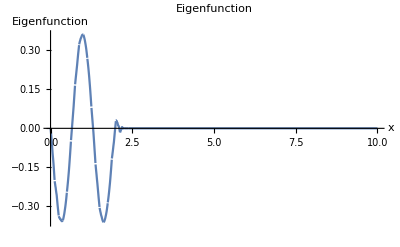

```mathematica
k=3; (*Resolution index*)
nMax=15; (*Number of scaling functions*)
coefficients={-0.1571493035978416,-0.3095650434778861,-0.3573900192444407,-0.27490354192632266,-0.09223139868618009,0.12397244898255123,0.2955033007713023,0.3604885497182732,0.2955033007712991,0.12397244898254592,-0.09223139868618567,-0.27490354192632693,-0.35739001924444297,-0.3095650434778872,-0.15714930359784215};

(*Define the scaling functions for Daubechies wavelet*)
scalingFunctions=Table[WaveletPhi[DaubechiesWavelet[3],2^k x-n],{n,0,nMax-1}];

(*Multiply each scaling function by its corresponding coefficient*)
eigenfunction=Sum[coefficients[[n+1]]*scalingFunctions[[n+1]],{n,0,nMax-1}];

(*Plot the eigenfunction with appropriate x range*)
Plot[eigenfunction,{x,0,10},PlotLabel->"Eigenfunction",AxesLabel->{"x","Eigenfunction"},PlotRange->All, PlotPoints->100]
```